## A few (probably) 2-D examples

### Code

```mathematica
SetDirectory[NotebookDirectory[]];
Needs["SSSiCv100`"];
```

### Examples

50372395 |  :  | {AB→AA,A→B,B→AA}
5867253020 |  :  | {AA→AB,AB→BA,B→AA}
5867590520 |  :  | {AA→AB,BB→AA,B→AA}
5898749475 |  :  | {AA→B,AB→AAA,B→AAA}
5898765100 |  :  | {AA→B,AB→BA,B→AAA}
5906311975 |  :  | {AA→BA,AB→AA,B→AAA}
5906315520 |  :  | {AA→BA,AB→BA,B→AA}
6142172479 |  :  | {AAB→AA,AA→ABA,B→A}
6142486975 |  :  | {AAB→AAA,A→B,B→AAA}
6144513020 |  :  | {AAB→BAA,A→B,B→AA}
6296549375 |  :  | {AB→AA,A→B,B→AAAAA}
6296550100 |  :  | {AB→AA,A→B,BB→AAA}
6296811975 |  :  | {AB→AA,AA→BA,B→AAA}
6296813020 |  :  | {AB→AA,AA→BB,B→AA}
6298424475 |  :  | {AB→AAA,AA→B,B→AAA}
6308138000 |  :  | {AB→BA,A→B,B→AAAA}
6308141145 |  :  | {AB→BA,A→BB,B→AA}
6308188020 |  :  | {AB→BA,AA→AB,B→AA}
6308190100 |  :  | {AB→BA,AA→B,B→AAA}
6308190520 |  :  | {AB→BA,AA→BA,B→AA}
6355378229 |  :  | {ABB→AA,A→BB,B→A}
6355450520 |  :  | {ABB→AAA,A→B,B→AA}
642296934875 |  :  | {A→BC,CB→A,B→AAAA}
702927424475 |  :  | {AA→,AB→BA,A→BB,B→AAA}
702927425104 |  :  | {AA→,AB→BA,A→BBB,B→A}
702929596979 |  :  | {AA→,AB→BAAA,A→BB,B→A}
726522984895 |  :  | {AA→A,AB→BA,A→BB,B→AA}
726523346979 |  :  | {AA→A,AB→BAA,A→BB,B→A}
733406619250 |  :  | {AA→AB,AB→BA,A→,B→AAAA}
733406622395 |  :  | {AA→AB,AB→BA,A→B,B→AA}
733406627471 |  :  | {AA→AB,AB→BA,B→AA,A→B}
733406627500 |  :  | {AA→AB,AB→BA,B→AAAAA}
733406628225 |  :  | {AA→AB,AB→BA,BB→AAA}
733408518645 |  :  | {AA→AB,ABB→ABA,B→AA}
733448810021 |  :  | {AA→AB,BB→AA,A→BB,B→}
733448814971 |  :  | {AA→AB,BB→AA,B→AA,A→B}
733448815501 |  :  | {AA→AB,BB→AA,BA→AAB}
733448903225 |  :  | {AA→AB,BB→BA,AB→AAA}

### 50372395

### 5867253020

### 5867590520

### 5898749475

### 5898765100

### 5906311975

### 5906315520

### 6142172479

### 6142486975

### 6144513020

### 6296549375

### 6296550100

### 6296811975

```mathematica
rs13=FromReducedRankIndex[6296811975]
```

<|Index→6296811975,QCode→34232324324233,RuleSet→{AB→AA,AA→BA,B→AAA}|>




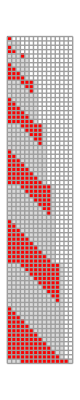
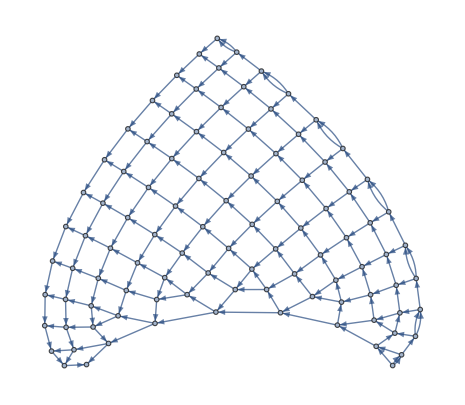
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules: | -Graphics--Graphics-

```mathematica
sss13=SSS[rs13[["RuleSet"]], "B",400, (* choose an appropriate initial state string, and # steps *)
(* options *) SSSMax->75,NetMax->99,NetSize->{600,Automatic},SSSSize->{Automatic,380},HighlightMethod->None,RulePlacement->Left,VertexLabels->Placed[Automatic,Tooltip],DirectedEdges->True,ImageSize->{Automatic,338.},NetSize->{Automatic,338},SSSSize->{Automatic,338},IconSize->{Automatic,31.8},VertexSize->Automatic]; (* options can be changed or omitted, but these are reasonable choices *)
```

```mathematica
NestList[Differences,{1,2,4,6,10,14,20,26,34,42,52,62},2]//Grid
```

1 | 2 | 4 | 6 | 10 | 14 | 20 | 26 | 34 | 42 | 52 | 62
1 | 2 | 2 | 4 | 4 | 6 | 6 | 8 | 8 | 10 | 10 | 
1 | 0 | 2 | 0 | 2 | 0 | 2 | 0 | 2 | 0 |  |

```mathematica
FindSequenceFunction[{3,9,19,33,51,73},n]
```

1+2 n^2

```mathematica
Table[1+2 n^2,{n,0,7}]
```

{1,3,9,19,33,51,73,99}

```mathematica
nds13=ToNetDifferenceSets[sss13[["Net"]]]
```

{{1,1,2},{1,2},{2,6},{1,2,2},{2,3},{1,4},{1,4},{1,4},{4,10},{1,4,4},{1,4},{1,4},{4,5},{1,6},{1,6},{1,6},{1,6},{1,6},{6,14},{1,6,6},{1,6},{1,6},{1,6},{1,6},{6,7},{1,8},{1,8},{1,8},{1,8},{1,8},{1,8},{1,8},{8,18},{1,8,8},{1,8},{1,8},{1,8},{1,8},{1,8},{1,8},{8,9},{1,10},{1,10},{1,10},{1,10},{1,10},{1,10},{1,10},{1,10},{1,10},{10,22},{1,10,10},{1,10},{1,10},{1,10},{1,10},{1,10},{1,10},{1,10},{1,10},{10,11},{1,12},{1,12},{1,12},{1,12},{1,12},{1,12},{1,12},{1,12},{1,12},{1,12},{1,12},{12,26},{1,12,12},{1,12},{1,12},{1,12},{1,12},{1,12},{1,12},{1,12},{1,12},{1,12},{1,12},{12,13},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{14,30},{1,14,14},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{14,15},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{16,34},{1,16,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{16,17},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{18,38},{1,18,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{18,19},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{20,42},{1,20,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{20,21},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{22,46},{1,22,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{22,23},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{24,50},{1,24,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{24,25},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{26,54},{1,26,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{26,27},{1,28},{1,28},{1,28},{1,28},{1,28},{1,28},{1,28},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{},{1},{1},{1},{1},{1},{1}}

```mathematica
Position[nds13,27]
```

{{365,2}}

```mathematica
ReduceSetList[nds13[[4;;365]]]
```

{€_(n$2⊨1)^5[{1,-2+4 n$2,-2+4 n$2},€_(n$1⊨1)^2[€^(-7+3 n$1+4 n$2)[{1,-4+2 n$1+4 n$2}],{-4+2 n$1+4 n$2,-4+3 n$1+4 n$1 n$2}],{1,4 n$2,4 n$2},€_(n$1⊨1)^2[€^(-5+3 n$1+4 n$2)[{1,-2+2 n$1+4 n$2}],{-2+2 n$1+4 n$2,-4+5 n$1+4 n$1 n$2}]],{1,22,22},€_(n$1⊨1)^2[€^(20+3 (-1+n$1))[{1,22+2 (-1+n$1)}],{22+2 (-1+n$1),23+27 (-1+n$1)}],{1,24,24},€_(n$1⊨1)^2[€^(22+3 (-1+n$1))[{1,24+2 (-1+n$1)}],{24+2 (-1+n$1),25+29 (-1+n$1)}],{1,26,26},€^24[{1,26}],{26,27}}

```mathematica
%32[[1;;1]] /. {n$1->j, n$2->k}
```

{€_(k⊨1)^5[{1,4 k-2,4 k-2},€_(j⊨1)^2[€^(3 j+4 k-7)[{1,2 j+4 k-4}],{2 j+4 k-4,4 k j+3 j-4}],{1,4 k,4 k},€_(j⊨1)^2[€^(3 j+4 k-5)[{1,2 j+4 k-2}],{2 j+4 k-2,4 k j+5 j-4}]]}

Check whether the k-concatenation might start earlier:

```mathematica
{{1,4 k-2,4 k-2},{1,2 j+4 k-4},{2 j+4 k-4,4 k j+3 j-4},{1,4 k,4 k},{1,2 j+4 k-2},{2 j+4 k-2,4 k j+5 j-4}}/.{k->0,j->1}
```

{{1,-2,-2},{1,-2},{-2,-1},{1,0,0},{1,0},{0,1}}

No, all of these terms would be forbidden in sessie network difference lists, which may contain empty sets, but only positive integers.

```mathematica
InputForm[%34]
```

```mathematica
{IndexedConcatenate[{1, -2 + 4*k, -2 + 4*k}, IndexedConcatenate[IndexedConcatenate[{1, -4 + 2*j + 4*k}, 
    -7 + 3*j + 4*k], {-4 + 2*j + 4*k, -4 + 3*j + 4*j*k}, {j, 1, 2}], {1, 4*k, 4*k}, 
  IndexedConcatenate[IndexedConcatenate[{1, -2 + 2*j + 4*k}, -5 + 3*j + 4*k], {-2 + 2*j + 4*k, -4 + 5*j + 4*j*k}, 
   {j, 1, 2}], {k, 1, 4}]}//Expand
```

{{1,2,2},€^0[{1,2}],{2,3},€^3[{1,4}],{4,10},{1,4,4},€^2[{1,4}],{4,5},€^5[{1,6}],{6,14},{1,6,6},€^4[{1,6}],{6,7},€^7[{1,8}],{8,18},{1,8,8},€^6[{1,8}],{8,9},€^9[{1,10}],{10,22},{1,10,10},€^8[{1,10}],{10,11},€^11[{1,12}],{12,26},{1,12,12},€^10[{1,12}],{12,13},€^13[{1,14}],{14,30},{1,14,14},€^12[{1,14}],{14,15},€^15[{1,16}],{16,34},{1,16,16},€^14[{1,16}],{16,17},€^17[{1,18}],{18,38}}

Terms like €^0[{1,2}] are no problem, “0 copies of ...”.  But 0 or negative numbers inside a set aren’t allowed.

```mathematica
GraphPlot@FromNetDifferenceSets@ExpandAll@
{IndexedConcatenate[{1, -2 + 4*k, -2 + 4*k}, IndexedConcatenate[IndexedConcatenate[{1, -4 + 2*j + 4*k}, 
    -7 + 3*j + 4*k], {-4 + 2*j + 4*k, -4 + 3*j + 4*j*k}, {j, 1, 2}], {1, 4*k, 4*k}, 
  IndexedConcatenate[IndexedConcatenate[{1, -2 + 2*j + 4*k}, -5 + 3*j + 4*k], {-2 + 2*j + 4*k, -4 + 5*j + 4*j*k}, 
   {j, 1, 2}], {k, 1, 7}]}
```

-Graphics-

### 6296813020 (Here’s a PROBLEM! Hurrah!)

```mathematica
rs14=FromReducedRankIndex[6296813020]
```

<|Index→6296813020,QCode→34232324342423,RuleSet→{AB→AA,AA→BB,B→AA}|>

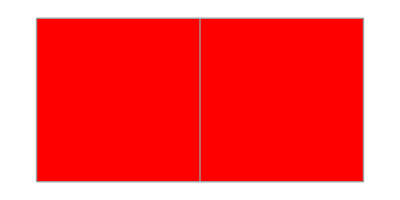
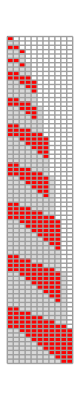
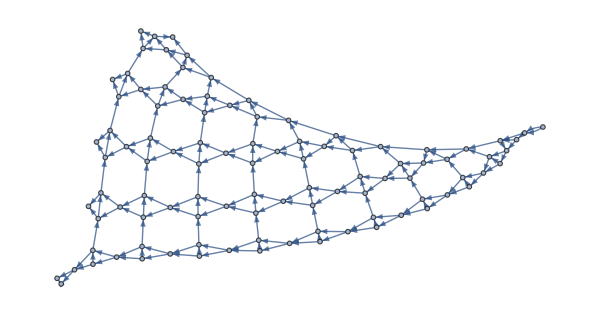
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules: | -Graphics--Graphics-

```mathematica
sss14=SSS[rs14[["RuleSet"]], "B",400, (* choose an appropriate initial state string, and # steps *)
(* options *) SSSMax->75,NetMax->99,NetSize->{600,Automatic},SSSSize->{Automatic,380},HighlightMethod->None,RulePlacement->Left,VertexLabels->Placed[Automatic,Tooltip],DirectedEdges->True,ImageSize->{Automatic,338.},NetSize->{Automatic,338},SSSSize->{Automatic,338},IconSize->{Automatic,31.8},VertexSize->Automatic]; (* options can be changed or omitted, but these are reasonable choices *)
```

```mathematica
NestList[Differences,{5,6,8,10,14,16,20,23,29,32,38,42,50,54},2]//Grid
```

5 | 6 | 8 | 10 | 14 | 16 | 20 | 23 | 29 | 32 | 38 | 42 | 50 | 54
1 | 2 | 2 | 4 | 2 | 4 | 3 | 6 | 3 | 6 | 4 | 8 | 4 | 
1 | 0 | 2 | -2 | 2 | -1 | 3 | -3 | 3 | -2 | 4 | -4 |  |

```mathematica
FindSequenceFunction[{4,9,13,22,28,41,49,66,76,97},n]
```

[n]

```mathematica
nds14=ToNetDifferenceSets[sss14[["Net"]]]
```

{{1,1},{1,2},{1,2},{1,5},{1,2},{1,2},{1,2},{2,3},{3,4},{1,4},{1,3},{1,3},{2,9},{2,3},{3,4},{1,4},{1,3},{1,3},{2,3},{3,4},{4,5},{5,6},{1,6},{1,5},{1,5},{1,4},{1,4},{3,13},{3,4},{4,5},{5,6},{1,6},{1,5},{1,5},{1,4},{1,4},{3,4},{4,5},{5,6},{6,7},{7,8},{1,8},{1,7},{1,7},{1,6},{1,6},{1,5},{1,5},{4,17},{4,5},{5,6},{6,7},{7,8},{1,8},{1,7},{1,7},{1,6},{1,6},{1,5},{1,5},{4,5},{5,6},{6,7},{7,8},{8,9},{9,10},{1,10},{1,9},{1,9},{1,8},{1,8},{1,7},{1,7},{1,6},{1,6},{5,21},{5,6},{6,7},{7,8},{8,9},{9,10},{1,10},{1,9},{1,9},{1,8},{1,8},{1,7},{1,7},{1,6},{1,6},{5,6},{6,7},{7,8},{8,9},{9,10},{10,11},{11,12},{1,12},{1,11},{1,11},{1,10},{1,10},{1,9},{1,9},{1,8},{1,8},{1,7},{1,7},{6,25},{6,7},{7,8},{8,9},{9,10},{10,11},{11,12},{1,12},{1,11},{1,11},{1,10},{1,10},{1,9},{1,9},{1,8},{1,8},{1,7},{1,7},{6,7},{7,8},{8,9},{9,10},{10,11},{11,12},{12,13},{13,14},{1,14},{1,13},{1,13},{1,12},{1,12},{1,11},{1,11},{1,10},{1,10},{1,9},{1,9},{1,8},{1,8},{7,29},{7,8},{8,9},{9,10},{10,11},{11,12},{12,13},{13,14},{1,14},{1,13},{1,13},{1,12},{1,12},{1,11},{1,11},{1,10},{1,10},{1,9},{1,9},{1,8},{1,8},{7,8},{8,9},{9,10},{10,11},{11,12},{12,13},{13,14},{14,15},{15,16},{1,16},{1,15},{1,15},{1,14},{1,14},{1,13},{1,13},{1,12},{1,12},{1,11},{1,11},{1,10},{1,10},{1,9},{1,9},{8,33},{8,9},{9,10},{10,11},{11,12},{12,13},{13,14},{14,15},{15,16},{1,16},{1,15},{1,15},{1,14},{1,14},{1,13},{1,13},{1,12},{1,12},{1,11},{1,11},{1,10},{1,10},{1,9},{1,9},{8,9},{9,10},{10,11},{11,12},{12,13},{13,14},{14,15},{15,16},{16,17},{17,18},{1,18},{1,17},{1,17},{1,16},{1,16},{1,15},{1,15},{1,14},{1,14},{1,13},{1,13},{1,12},{1,12},{1,11},{1,11},{1,10},{1,10},{9,37},{9,10},{10,11},{11,12},{12,13},{13,14},{14,15},{15,16},{16,17},{17,18},{1,18},{1,17},{1,17},{1,16},{1,16},{1,15},{1,15},{1,14},{1,14},{1,13},{1,13},{1,12},{1,12},{1,11},{1,11},{1,10},{1,10},{9,10},{10,11},{11,12},{12,13},{13,14},{14,15},{15,16},{16,17},{17,18},{18,19},{19,20},{1,20},{1,19},{1,19},{1,18},{1,18},{1,17},{1,17},{1,16},{1,16},{1,15},{1,15},{1,14},{1,14},{1,13},{1,13},{1,12},{1,12},{1,11},{1,11},{10,41},{10,11},{11,12},{12,13},{13,14},{14,15},{15,16},{16,17},{17,18},{18,19},{19,20},{1,20},{1,19},{1,19},{1,18},{1,18},{1,17},{1,17},{1,16},{1,16},{1,15},{1,15},{1,14},{1,14},{1,13},{1,13},{1,12},{1,12},{1,11},{1,11},{10,11},{11,12},{12,13},{13,14},{14,15},{15,16},{16,17},{17,18},{18,19},{19,20},{20,21},{21,22},{1,22},{1,21},{1,21},{1,20},{1,20},{1,19},{1,19},{1,18},{1,18},{1,17},{1,17},{1,16},{1,16},{1,15},{1,15},{1,14},{1,14},{1,13},{1,13},{1,12},{1,12},{11},{11,12},{12,13},{13,14},{14,15},{15,16},{16,17},{17,18},{18,19},{19,20},{20,21},{21,22},{1,22},{1,21},{1,21},{1,20},{1,20},{1,19},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1}}

```mathematica
Position[nds14,22]
```

{{342,2},{343,2},{375,2},{376,2}}

```mathematica
ReduceSetList[nds14[[1;;342]]]
```

DifferenceRoot::undef: DifferenceRoot[Function[{y,n},{0+0 y[«1»]+y[Plus[«2»]]==0,y[1]==0,y[0]==0}]] does not define a suitable difference root object.

{{1,1},€^2[{1,2}],{1,5},€^3[{1,2}],€_(n$1⊨1)^2[{1+n$1,2+n$1}],{1,4},€^2[{1,3}],{2,9},{2,3},{3,4},{1,4},€^2[{1,3}],€_(n$1⊨1)^4[{1+n$1,2+n$1}],{1,6},€_(n$1⊨1)^2[€^2[{1,6-n$1}]],{3,13},{3,4},{4,5},{5,6},{1,6},€_(n$1⊨1)^2[€^2[{1,6-n$1}]],€_(n$1⊨1)^5[{2+n$1,3+n$1}],{1,8},€_(n$1⊨1)^3[€^2[{1,8-n$1}]],{4,17},{4,5},{5,6},{6,7},{7,8},{1,8},€_(n$1⊨1)^3[€^2[{1,8-n$1}]],€_(n$1⊨1)^6[{3+n$1,4+n$1}],{1,10},€_(n$1⊨1)^4[€^2[{1,10-n$1}]],€_(n$1⊨1)^6[{[n$1],[n$1]}],{1,10},€_(n$1⊨1)^4[€^2[{1,10-n$1}]],€_(n$1⊨1)^7[{4+n$1,5+n$1}],{1,12},€_(n$1⊨1)^5[€^2[{1,12-n$1}]],{6,25},{6,7},{7,8},{8,9},{9,10},{10,11},{11,12},{1,12},€_(n$1⊨1)^5[€^2[{1,12-n$1}]],€_(n$1⊨1)^8[{5+n$1,6+n$1}],{1,14},€_(n$1⊨1)^6[€^2[{1,14-n$1}]],{7,29},{7,8},{8,9},{9,10},{10,11},{11,12},{12,13},{13,14},{1,14},€_(n$1⊨1)^6[€^2[{1,14-n$1}]],€_(n$1⊨1)^9[{6+n$1,7+n$1}],{1,16},€_(n$1⊨1)^7[€^2[{1,16-n$1}]],{8,33},{8,9},{9,10},{10,11},{11,12},{12,13},{13,14},{14,15},{15,16},{1,16},€_(n$1⊨1)^7[€^2[{1,16-n$1}]],€_(n$1⊨1)^10[{7+n$1,8+n$1}],{1,18},€_(n$1⊨1)^8[€^2[{1,18-n$1}]],{9,37},{9,10},{10,11},{11,12},{12,13},{13,14},{14,15},{15,16},{16,17},{17,18},{1,18},€_(n$1⊨1)^8[€^2[{1,18-n$1}]],€_(n$1⊨1)^11[{8+n$1,9+n$1}],{1,20},€_(n$1⊨1)^9[€^2[{1,20-n$1}]],{10,41},{10,11},{11,12},{12,13},{13,14},{14,15},{15,16},{16,17},{17,18},{18,19},{19,20},{1,20},€_(n$1⊨1)^9[€^2[{1,20-n$1}]],€_(n$1⊨1)^12[{9+n$1,10+n$1}]}

This reduction is not complete, some formulas are missing.  Try again, with 1000 extra steps!

```mathematica
?SSSEvolve
```

```mathematica
SSSEvolve[sss14,1000]
```

```mathematica
ToNetDifferenceSets@sss14[["Net"]]
```

{{1,1},{1,2},{1,2},{1,5},{1,2},{1,2},{1,2},{2,3},{3,4},{1,4},{1,3},{1,3},{2,9},{2,3},{3,4},{1,4},{1,3},{1,3},{2,3},{3,4},{4,5},{5,6},{1,6},{1,5},{1,5},{1,4},{1,4},{3,13},{3,4},{4,5},{5,6},{1,6},{1,5},{1,5},{1,4},{1,4},{3,4},{4,5},{5,6},{6,7},{7,8},{1,8},{1,7},{1,7},{1,6},{1,6},{1,5},{1,5},{4,17},{4,5},{5,6},{6,7},{7,8},{1,8},{1,7},{1,7},{1,6},{1,6},{1,5},{1,5},{4,5},{5,6},{6,7},{7,8},{8,9},{9,10},{1,10},{1,9},{1,9},{1,8},{1,8},{1,7},{1,7},{1,6},{1,6},{5,21},{5,6},{6,7},{7,8},{8,9},{9,10},{1,10},{1,9},{1,9},{1,8},{1,8},{1,7},{1,7},{1,6},{1,6},{5,6},{6,7},{7,8},{8,9},{9,10},{10,11},{11,12},{1,12},{1,11},{1,11},{1,10},{1,10},{1,9},{1,9},{1,8},{1,8},{1,7},{1,7},{6,25},{6,7},{7,8},{8,9},{9,10},{10,11},{11,12},{1,12},{1,11},{1,11},{1,10},{1,10},{1,9},{1,9},{1,8},{1,8},{1,7},{1,7},{6,7},{7,8},{8,9},{9,10},{10,11},{11,12},{12,13},{13,14},{1,14},{1,13},{1,13},{1,12},{1,12},{1,11},{1,11},{1,10},{1,10},{1,9},{1,9},{1,8},{1,8},{7,29},{7,8},{8,9},{9,10},{10,11},{11,12},{12,13},{13,14},{1,14},{1,13},{1,13},{1,12},{1,12},{1,11},{1,11},{1,10},{1,10},{1,9},{1,9},{1,8},{1,8},{7,8},{8,9},{9,10},{10,11},{11,12},{12,13},{13,14},{14,15},{15,16},{1,16},{1,15},{1,15},{1,14},{1,14},{1,13},{1,13},{1,12},{1,12},{1,11},{1,11},{1,10},{1,10},{1,9},{1,9},{8,33},{8,9},{9,10},{10,11},{11,12},{12,13},{13,14},{14,15},{15,16},{1,16},{1,15},{1,15},{1,14},{1,14},{1,13},{1,13},{1,12},{1,12},{1,11},{1,11},{1,10},{1,10},{1,9},{1,9},{8,9},{9,10},{10,11},{11,12},{12,13},{13,14},{14,15},{15,16},{16,17},{17,18},{1,18},{1,17},{1,17},{1,16},{1,16},{1,15},{1,15},{1,14},{1,14},{1,13},{1,13},{1,12},{1,12},{1,11},{1,11},{1,10},{1,10},{9,37},{9,10},{10,11},{11,12},{12,13},{13,14},{14,15},{15,16},{16,17},{17,18},{1,18},{1,17},{1,17},{1,16},{1,16},{1,15},{1,15},{1,14},{1,14},{1,13},{1,13},{1,12},{1,12},{1,11},{1,11},{1,10},{1,10},{9,10},{10,11},{11,12},{12,13},{13,14},{14,15},{15,16},{16,17},{17,18},{18,19},{19,20},{1,20},{1,19},{1,19},{1,18},{1,18},{1,17},{1,17},{1,16},{1,16},{1,15},{1,15},{1,14},{1,14},{1,13},{1,13},{1,12},{1,12},{1,11},{1,11},{10,41},{10,11},{11,12},{12,13},{13,14},{14,15},{15,16},{16,17},{17,18},{18,19},{19,20},{1,20},{1,19},{1,19},{1,18},{1,18},{1,17},{1,17},{1,16},{1,16},{1,15},{1,15},{1,14},{1,14},{1,13},{1,13},{1,12},{1,12},{1,11},{1,11},{10,11},{11,12},{12,13},{13,14},{14,15},{15,16},{16,17},{17,18},{18,19},{19,20},{20,21},{21,22},{1,22},{1,21},{1,21},{1,20},{1,20},{1,19},{1,19},{1,18},{1,18},{1,17},{1,17},{1,16},{1,16},{1,15},{1,15},{1,14},{1,14},{1,13},{1,13},{1,12},{1,12},{11},{11,12},{12,13},{13,14},{14,15},{15,16},{16,17},{17,18},{18,19},{19,20},{20,21},{21,22},{1,22},{1,21},{1,21},{1,20},{1,20},{1,19},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1}}

```mathematica
Position[nds14,{_}]
```

{{364},{382},{383},{384},{385},{386},{387},{388},{389},{390},{391},{392},{393},{394},{395},{396}}

```mathematica
ReduceSetList[nds14[[1;;363]]]
```

DifferenceRoot::undef: DifferenceRoot[Function[{y,n},{0+0 y[«1»]+y[Plus[«2»]]==0,y[1]==0,y[0]==0}]] does not define a suitable difference root object.

{{1,1},€^2[{1,2}],{1,5},€^3[{1,2}],€_(n$1⊨1)^2[{1+n$1,2+n$1}],{1,4},€^2[{1,3}],{2,9},{2,3},{3,4},{1,4},€^2[{1,3}],€_(n$1⊨1)^4[{1+n$1,2+n$1}],{1,6},€_(n$1⊨1)^2[€^2[{1,6-n$1}]],{3,13},{3,4},{4,5},{5,6},{1,6},€_(n$1⊨1)^2[€^2[{1,6-n$1}]],€_(n$1⊨1)^5[{2+n$1,3+n$1}],{1,8},€_(n$1⊨1)^3[€^2[{1,8-n$1}]],{4,17},{4,5},{5,6},{6,7},{7,8},{1,8},€_(n$1⊨1)^3[€^2[{1,8-n$1}]],€_(n$1⊨1)^6[{3+n$1,4+n$1}],{1,10},€_(n$1⊨1)^4[€^2[{1,10-n$1}]],€_(n$1⊨1)^6[{[n$1],[n$1]}],{1,10},€_(n$1⊨1)^4[€^2[{1,10-n$1}]],€_(n$1⊨1)^7[{4+n$1,5+n$1}],{1,12},€_(n$1⊨1)^5[€^2[{1,12-n$1}]],{6,25},{6,7},{7,8},{8,9},{9,10},{10,11},{11,12},{1,12},€_(n$1⊨1)^5[€^2[{1,12-n$1}]],€_(n$1⊨1)^8[{5+n$1,6+n$1}],{1,14},€_(n$1⊨1)^6[€^2[{1,14-n$1}]],{7,29},{7,8},{8,9},{9,10},{10,11},{11,12},{12,13},{13,14},{1,14},€_(n$1⊨1)^6[€^2[{1,14-n$1}]],€_(n$1⊨1)^9[{6+n$1,7+n$1}],{1,16},€_(n$1⊨1)^7[€^2[{1,16-n$1}]],{8,33},{8,9},{9,10},{10,11},{11,12},{12,13},{13,14},{14,15},{15,16},{1,16},€_(n$1⊨1)^7[€^2[{1,16-n$1}]],€_(n$1⊨1)^10[{7+n$1,8+n$1}],{1,18},€_(n$1⊨1)^8[€^2[{1,18-n$1}]],{9,37},{9,10},{10,11},{11,12},{12,13},{13,14},{14,15},{15,16},{16,17},{17,18},{1,18},€_(n$1⊨1)^8[€^2[{1,18-n$1}]],€_(n$1⊨1)^11[{8+n$1,9+n$1}],{1,20},€_(n$1⊨1)^9[€^2[{1,20-n$1}]],{10,41},{10,11},{11,12},{12,13},{13,14},{14,15},{15,16},{16,17},{17,18},{18,19},{19,20},{1,20},€_(n$1⊨1)^9[€^2[{1,20-n$1}]],€_(n$1⊨1)^12[{9+n$1,10+n$1}],{1,22},€_(n$1⊨1)^10[€^2[{1,22-n$1}]]}

```mathematica
$debug=True;
ReduceSetList[nds14[[1;;363]]]
$debug=False;
```

Entering ReduceSetList with: {{1,1},{1,2},{1,2},{1,5},{1,2},{1,2},{1,2},{2,3},{3,4},{1,4},{1,3},{1,3},{2,9},{2,3},{3,4},{1,4},{1,3},{1,3},{2,3},{3,4},{4,5},{5,6},{1,6},{1,5},{1,5},{1,4},{1,4},{3,13},{3,4},{4,5},{5,6},{1,6},{1,5},{1,5},{1,4},{1,4},{3,4},{4,5},{5,6},{6,7},{7,8},{1,8},{1,7},{1,7},{1,6},{1,6},{1,5},{1,5},{4,17},{4,5},{5,6},{6,7},{7,8},{1,8},{1,7},{1,7},{1,6},{1,6},{1,5},{1,5},{4,5},{5,6},{6,7},{7,8},{8,9},{9,10},{1,10},{1,9},{1,9},{1,8},{1,8},{1,7},{1,7},{1,6},{1,6},{5,21},{5,6},{6,7},{7,8},{8,9},{9,10},{1,10},{1,9},{1,9},{1,8},{1,8},{1,7},{1,7},{1,6},{1,6},{5,6},{6,7},{7,8},{8,9},{9,10},{10,11},{11,12},{1,12},{1,11},{1,11},{1,10},{1,10},{1,9},{1,9},{1,8},{1,8},{1,7},{1,7},{6,25},{6,7},{7,8},{8,9},{9,10},{10,11},{11,12},{1,12},{1,11},{1,11},{1,10},{1,10},{1,9},{1,9},{1,8},{1,8},{1,7},{1,7},{6,7},{7,8},{8,9},{9,10},{10,11},{11,12},{12,13},{13,14},{1,14},{1,13},{1,13},{1,12},{1,12},{1,11},{1,11},{1,10},{1,10},{1,9},{1,9},{1,8},{1,8},{7,29},{7,8},{8,9},{9,10},{10,11},{11,12},{12,13},{13,14},{1,14},{1,13},{1,13},{1,12},{1,12},{1,11},{1,11},{1,10},{1,10},{1,9},{1,9},{1,8},{1,8},{7,8},{8,9},{9,10},{10,11},{11,12},{12,13},{13,14},{14,15},{15,16},{1,16},{1,15},{1,15},{1,14},{1,14},{1,13},{1,13},{1,12},{1,12},{1,11},{1,11},{1,10},{1,10},{1,9},{1,9},{8,33},{8,9},{9,10},{10,11},{11,12},{12,13},{13,14},{14,15},{15,16},{1,16},{1,15},{1,15},{1,14},{1,14},{1,13},{1,13},{1,12},{1,12},{1,11},{1,11},{1,10},{1,10},{1,9},{1,9},{8,9},{9,10},{10,11},{11,12},{12,13},{13,14},{14,15},{15,16},{16,17},{17,18},{1,18},{1,17},{1,17},{1,16},{1,16},{1,15},{1,15},{1,14},{1,14},{1,13},{1,13},{1,12},{1,12},{1,11},{1,11},{1,10},{1,10},{9,37},{9,10},{10,11},{11,12},{12,13},{13,14},{14,15},{15,16},{16,17},{17,18},{1,18},{1,17},{1,17},{1,16},{1,16},{1,15},{1,15},{1,14},{1,14},{1,13},{1,13},{1,12},{1,12},{1,11},{1,11},{1,10},{1,10},{9,10},{10,11},{11,12},{12,13},{13,14},{14,15},{15,16},{16,17},{17,18},{18,19},{19,20},{1,20},{1,19},{1,19},{1,18},{1,18},{1,17},{1,17},{1,16},{1,16},{1,15},{1,15},{1,14},{1,14},{1,13},{1,13},{1,12},{1,12},{1,11},{1,11},{10,41},{10,11},{11,12},{12,13},{13,14},{14,15},{15,16},{16,17},{17,18},{18,19},{19,20},{1,20},{1,19},{1,19},{1,18},{1,18},{1,17},{1,17},{1,16},{1,16},{1,15},{1,15},{1,14},{1,14},{1,13},{1,13},{1,12},{1,12},{1,11},{1,11},{10,11},{11,12},{12,13},{13,14},{14,15},{15,16},{16,17},{17,18},{18,19},{19,20},{20,21},{21,22},{1,22},{1,21},{1,21},{1,20},{1,20},{1,19},{1,19},{1,18},{1,18},{1,17},{1,17},{1,16},{1,16},{1,15},{1,15},{1,14},{1,14},{1,13},{1,13},{1,12},{1,12}}

exact repLen = 1: {{1,1},€^2[{1,2}],{1,5},€^3[{1,2}],{2,3},{3,4},{1,4},€^2[{1,3}],{2,9},{2,3},{3,4},{1,4},€^2[{1,3}],{2,3},{3,4},{4,5},{5,6},{1,6},€^2[{1,5}],€^2[{1,4}],{3,13},{3,4},{4,5},{5,6},{1,6},€^2[{1,5}],€^2[{1,4}],{3,4},{4,5},{5,6},{6,7},{7,8},{1,8},€^2[{1,7}],€^2[{1,6}],€^2[{1,5}],{4,17},{4,5},{5,6},{6,7},{7,8},{1,8},€^2[{1,7}],€^2[{1,6}],€^2[{1,5}],{4,5},{5,6},{6,7},{7,8},{8,9},{9,10},{1,10},€^2[{1,9}],€^2[{1,8}],€^2[{1,7}],€^2[{1,6}],{5,21},{5,6},{6,7},{7,8},{8,9},{9,10},{1,10},€^2[{1,9}],€^2[{1,8}],€^2[{1,7}],€^2[{1,6}],{5,6},{6,7},{7,8},{8,9},{9,10},{10,11},{11,12},{1,12},€^2[{1,11}],€^2[{1,10}],€^2[{1,9}],€^2[{1,8}],€^2[{1,7}],{6,25},{6,7},{7,8},{8,9},{9,10},{10,11},{11,12},{1,12},€^2[{1,11}],€^2[{1,10}],€^2[{1,9}],€^2[{1,8}],€^2[{1,7}],{6,7},{7,8},{8,9},{9,10},{10,11},{11,12},{12,13},{13,14},{1,14},€^2[{1,13}],€^2[{1,12}],€^2[{1,11}],€^2[{1,10}],€^2[{1,9}],€^2[{1,8}],{7,29},{7,8},{8,9},{9,10},{10,11},{11,12},{12,13},{13,14},{1,14},€^2[{1,13}],€^2[{1,12}],€^2[{1,11}],€^2[{1,10}],€^2[{1,9}],€^2[{1,8}],{7,8},{8,9},{9,10},{10,11},{11,12},{12,13},{13,14},{14,15},{15,16},{1,16},€^2[{1,15}],€^2[{1,14}],€^2[{1,13}],€^2[{1,12}],€^2[{1,11}],€^2[{1,10}],€^2[{1,9}],{8,33},{8,9},{9,10},{10,11},{11,12},{12,13},{13,14},{14,15},{15,16},{1,16},€^2[{1,15}],€^2[{1,14}],€^2[{1,13}],€^2[{1,12}],€^2[{1,11}],€^2[{1,10}],€^2[{1,9}],{8,9},{9,10},{10,11},{11,12},{12,13},{13,14},{14,15},{15,16},{16,17},{17,18},{1,18},€^2[{1,17}],€^2[{1,16}],€^2[{1,15}],€^2[{1,14}],€^2[{1,13}],€^2[{1,12}],€^2[{1,11}],€^2[{1,10}],{9,37},{9,10},{10,11},{11,12},{12,13},{13,14},{14,15},{15,16},{16,17},{17,18},{1,18},€^2[{1,17}],€^2[{1,16}],€^2[{1,15}],€^2[{1,14}],€^2[{1,13}],€^2[{1,12}],€^2[{1,11}],€^2[{1,10}],{9,10},{10,11},{11,12},{12,13},{13,14},{14,15},{15,16},{16,17},{17,18},{18,19},{19,20},{1,20},€^2[{1,19}],€^2[{1,18}],€^2[{1,17}],€^2[{1,16}],€^2[{1,15}],€^2[{1,14}],€^2[{1,13}],€^2[{1,12}],€^2[{1,11}],{10,41},{10,11},{11,12},{12,13},{13,14},{14,15},{15,16},{16,17},{17,18},{18,19},{19,20},{1,20},€^2[{1,19}],€^2[{1,18}],€^2[{1,17}],€^2[{1,16}],€^2[{1,15}],€^2[{1,14}],€^2[{1,13}],€^2[{1,12}],€^2[{1,11}],{10,11},{11,12},{12,13},{13,14},{14,15},{15,16},{16,17},{17,18},{18,19},{19,20},{20,21},{21,22},{1,22},€^2[{1,21}],€^2[{1,20}],€^2[{1,19}],€^2[{1,18}],€^2[{1,17}],€^2[{1,16}],€^2[{1,15}],€^2[{1,14}],€^2[{1,13}],€^2[{1,12}]}

Entering improveReduction with: {{1,1},€^2[{1,2}],{1,5},€^3[{1,2}],{2,3},{3,4},{1,4},€^2[{1,3}],{2,9},{2,3},{3,4},{1,4},€^2[{1,3}],{2,3},{3,4},{4,5},{5,6},{1,6},€^2[{1,5}],€^2[{1,4}],{3,13},{3,4},{4,5},{5,6},{1,6},€^2[{1,5}],€^2[{1,4}],{3,4},{4,5},{5,6},{6,7},{7,8},{1,8},€^2[{1,7}],€^2[{1,6}],€^2[{1,5}],{4,17},{4,5},{5,6},{6,7},{7,8},{1,8},€^2[{1,7}],€^2[{1,6}],€^2[{1,5}],{4,5},{5,6},{6,7},{7,8},{8,9},{9,10},{1,10},€^2[{1,9}],€^2[{1,8}],€^2[{1,7}],€^2[{1,6}],{5,21},{5,6},{6,7},{7,8},{8,9},{9,10},{1,10},€^2[{1,9}],€^2[{1,8}],€^2[{1,7}],€^2[{1,6}],{5,6},{6,7},{7,8},{8,9},{9,10},{10,11},{11,12},{1,12},€^2[{1,11}],€^2[{1,10}],€^2[{1,9}],€^2[{1,8}],€^2[{1,7}],{6,25},{6,7},{7,8},{8,9},{9,10},{10,11},{11,12},{1,12},€^2[{1,11}],€^2[{1,10}],€^2[{1,9}],€^2[{1,8}],€^2[{1,7}],{6,7},{7,8},{8,9},{9,10},{10,11},{11,12},{12,13},{13,14},{1,14},€^2[{1,13}],€^2[{1,12}],€^2[{1,11}],€^2[{1,10}],€^2[{1,9}],€^2[{1,8}],{7,29},{7,8},{8,9},{9,10},{10,11},{11,12},{12,13},{13,14},{1,14},€^2[{1,13}],€^2[{1,12}],€^2[{1,11}],€^2[{1,10}],€^2[{1,9}],€^2[{1,8}],{7,8},{8,9},{9,10},{10,11},{11,12},{12,13},{13,14},{14,15},{15,16},{1,16},€^2[{1,15}],€^2[{1,14}],€^2[{1,13}],€^2[{1,12}],€^2[{1,11}],€^2[{1,10}],€^2[{1,9}],{8,33},{8,9},{9,10},{10,11},{11,12},{12,13},{13,14},{14,15},{15,16},{1,16},€^2[{1,15}],€^2[{1,14}],€^2[{1,13}],€^2[{1,12}],€^2[{1,11}],€^2[{1,10}],€^2[{1,9}],{8,9},{9,10},{10,11},{11,12},{12,13},{13,14},{14,15},{15,16},{16,17},{17,18},{1,18},€^2[{1,17}],€^2[{1,16}],€^2[{1,15}],€^2[{1,14}],€^2[{1,13}],€^2[{1,12}],€^2[{1,11}],€^2[{1,10}],{9,37},{9,10},{10,11},{11,12},{12,13},{13,14},{14,15},{15,16},{16,17},{17,18},{1,18},€^2[{1,17}],€^2[{1,16}],€^2[{1,15}],€^2[{1,14}],€^2[{1,13}],€^2[{1,12}],€^2[{1,11}],€^2[{1,10}],{9,10},{10,11},{11,12},{12,13},{13,14},{14,15},{15,16},{16,17},{17,18},{18,19},{19,20},{1,20},€^2[{1,19}],€^2[{1,18}],€^2[{1,17}],€^2[{1,16}],€^2[{1,15}],€^2[{1,14}],€^2[{1,13}],€^2[{1,12}],€^2[{1,11}],{10,41},{10,11},{11,12},{12,13},{13,14},{14,15},{15,16},{16,17},{17,18},{18,19},{19,20},{1,20},€^2[{1,19}],€^2[{1,18}],€^2[{1,17}],€^2[{1,16}],€^2[{1,15}],€^2[{1,14}],€^2[{1,13}],€^2[{1,12}],€^2[{1,11}],{10,11},{11,12},{12,13},{13,14},{14,15},{15,16},{16,17},{17,18},{18,19},{19,20},{20,21},{21,22},{1,22},€^2[{1,21}],€^2[{1,20}],€^2[{1,19}],€^2[{1,18}],€^2[{1,17}],€^2[{1,16}],€^2[{1,15}],€^2[{1,14}],€^2[{1,13}],€^2[{1,12}]}

improved? : {{1,1},€^2[{1,2}],{1,5},€^3[{1,2}],{2,3},{3,4},{1,4},€^2[{1,3}],{2,9},{2,3},{3,4},{1,4},€^2[{1,3}],{2,3},{3,4},{4,5},{5,6},{1,6},€^2[{1,5}],€^2[{1,4}],{3,13},{3,4},{4,5},{5,6},{1,6},€^2[{1,5}],€^2[{1,4}],{3,4},{4,5},{5,6},{6,7},{7,8},{1,8},€^2[{1,7}],€^2[{1,6}],€^2[{1,5}],{4,17},{4,5},{5,6},{6,7},{7,8},{1,8},€^2[{1,7}],€^2[{1,6}],€^2[{1,5}],{4,5},{5,6},{6,7},{7,8},{8,9},{9,10},{1,10},€^2[{1,9}],€^2[{1,8}],€^2[{1,7}],€^2[{1,6}],{5,21},{5,6},{6,7},{7,8},{8,9},{9,10},{1,10},€^2[{1,9}],€^2[{1,8}],€^2[{1,7}],€^2[{1,6}],{5,6},{6,7},{7,8},{8,9},{9,10},{10,11},{11,12},{1,12},€^2[{1,11}],€^2[{1,10}],€^2[{1,9}],€^2[{1,8}],€^2[{1,7}],{6,25},{6,7},{7,8},{8,9},{9,10},{10,11},{11,12},{1,12},€^2[{1,11}],€^2[{1,10}],€^2[{1,9}],€^2[{1,8}],€^2[{1,7}],{6,7},{7,8},{8,9},{9,10},{10,11},{11,12},{12,13},{13,14},{1,14},€^2[{1,13}],€^2[{1,12}],€^2[{1,11}],€^2[{1,10}],€^2[{1,9}],€^2[{1,8}],{7,29},{7,8},{8,9},{9,10},{10,11},{11,12},{12,13},{13,14},{1,14},€^2[{1,13}],€^2[{1,12}],€^2[{1,11}],€^2[{1,10}],€^2[{1,9}],€^2[{1,8}],{7,8},{8,9},{9,10},{10,11},{11,12},{12,13},{13,14},{14,15},{15,16},{1,16},€^2[{1,15}],€^2[{1,14}],€^2[{1,13}],€^2[{1,12}],€^2[{1,11}],€^2[{1,10}],€^2[{1,9}],{8,33},{8,9},{9,10},{10,11},{11,12},{12,13},{13,14},{14,15},{15,16},{1,16},€^2[{1,15}],€^2[{1,14}],€^2[{1,13}],€^2[{1,12}],€^2[{1,11}],€^2[{1,10}],€^2[{1,9}],{8,9},{9,10},{10,11},{11,12},{12,13},{13,14},{14,15},{15,16},{16,17},{17,18},{1,18},€^2[{1,17}],€^2[{1,16}],€^2[{1,15}],€^2[{1,14}],€^2[{1,13}],€^2[{1,12}],€^2[{1,11}],€^2[{1,10}],{9,37},{9,10},{10,11},{11,12},{12,13},{13,14},{14,15},{15,16},{16,17},{17,18},{1,18},€^2[{1,17}],€^2[{1,16}],€^2[{1,15}],€^2[{1,14}],€^2[{1,13}],€^2[{1,12}],€^2[{1,11}],€^2[{1,10}],{9,10},{10,11},{11,12},{12,13},{13,14},{14,15},{15,16},{16,17},{17,18},{18,19},{19,20},{1,20},€^2[{1,19}],€^2[{1,18}],€^2[{1,17}],€^2[{1,16}],€^2[{1,15}],€^2[{1,14}],€^2[{1,13}],€^2[{1,12}],€^2[{1,11}],{10,41},{10,11},{11,12},{12,13},{13,14},{14,15},{15,16},{16,17},{17,18},{18,19},{19,20},{1,20},€^2[{1,19}],€^2[{1,18}],€^2[{1,17}],€^2[{1,16}],€^2[{1,15}],€^2[{1,14}],€^2[{1,13}],€^2[{1,12}],€^2[{1,11}],{10,11},{11,12},{12,13},{13,14},{14,15},{15,16},{16,17},{17,18},{18,19},{19,20},{20,21},{21,22},{1,22},€^2[{1,21}],€^2[{1,20}],€^2[{1,19}],€^2[{1,18}],€^2[{1,17}],€^2[{1,16}],€^2[{1,15}],€^2[{1,14}],€^2[{1,13}],€^2[{1,12}]}

Entering ReduceSetList with: {{1,1},€^2[{1,2}],{1,5},€^3[{1,2}],{2,3},{3,4},{1,4},€^2[{1,3}],{2,9},{2,3},{3,4},{1,4},€^2[{1,3}],{2,3},{3,4},{4,5},{5,6},{1,6},€^2[{1,5}],€^2[{1,4}],{3,13},{3,4},{4,5},{5,6},{1,6},€^2[{1,5}],€^2[{1,4}],{3,4},{4,5},{5,6},{6,7},{7,8},{1,8},€^2[{1,7}],€^2[{1,6}],€^2[{1,5}],{4,17},{4,5},{5,6},{6,7},{7,8},{1,8},€^2[{1,7}],€^2[{1,6}],€^2[{1,5}],{4,5},{5,6},{6,7},{7,8},{8,9},{9,10},{1,10},€^2[{1,9}],€^2[{1,8}],€^2[{1,7}],€^2[{1,6}],{5,21},{5,6},{6,7},{7,8},{8,9},{9,10},{1,10},€^2[{1,9}],€^2[{1,8}],€^2[{1,7}],€^2[{1,6}],{5,6},{6,7},{7,8},{8,9},{9,10},{10,11},{11,12},{1,12},€^2[{1,11}],€^2[{1,10}],€^2[{1,9}],€^2[{1,8}],€^2[{1,7}],{6,25},{6,7},{7,8},{8,9},{9,10},{10,11},{11,12},{1,12},€^2[{1,11}],€^2[{1,10}],€^2[{1,9}],€^2[{1,8}],€^2[{1,7}],{6,7},{7,8},{8,9},{9,10},{10,11},{11,12},{12,13},{13,14},{1,14},€^2[{1,13}],€^2[{1,12}],€^2[{1,11}],€^2[{1,10}],€^2[{1,9}],€^2[{1,8}],{7,29},{7,8},{8,9},{9,10},{10,11},{11,12},{12,13},{13,14},{1,14},€^2[{1,13}],€^2[{1,12}],€^2[{1,11}],€^2[{1,10}],€^2[{1,9}],€^2[{1,8}],{7,8},{8,9},{9,10},{10,11},{11,12},{12,13},{13,14},{14,15},{15,16},{1,16},€^2[{1,15}],€^2[{1,14}],€^2[{1,13}],€^2[{1,12}],€^2[{1,11}],€^2[{1,10}],€^2[{1,9}],{8,33},{8,9},{9,10},{10,11},{11,12},{12,13},{13,14},{14,15},{15,16},{1,16},€^2[{1,15}],€^2[{1,14}],€^2[{1,13}],€^2[{1,12}],€^2[{1,11}],€^2[{1,10}],€^2[{1,9}],{8,9},{9,10},{10,11},{11,12},{12,13},{13,14},{14,15},{15,16},{16,17},{17,18},{1,18},€^2[{1,17}],€^2[{1,16}],€^2[{1,15}],€^2[{1,14}],€^2[{1,13}],€^2[{1,12}],€^2[{1,11}],€^2[{1,10}],{9,37},{9,10},{10,11},{11,12},{12,13},{13,14},{14,15},{15,16},{16,17},{17,18},{1,18},€^2[{1,17}],€^2[{1,16}],€^2[{1,15}],€^2[{1,14}],€^2[{1,13}],€^2[{1,12}],€^2[{1,11}],€^2[{1,10}],{9,10},{10,11},{11,12},{12,13},{13,14},{14,15},{15,16},{16,17},{17,18},{18,19},{19,20},{1,20},€^2[{1,19}],€^2[{1,18}],€^2[{1,17}],€^2[{1,16}],€^2[{1,15}],€^2[{1,14}],€^2[{1,13}],€^2[{1,12}],€^2[{1,11}],{10,41},{10,11},{11,12},{12,13},{13,14},{14,15},{15,16},{16,17},{17,18},{18,19},{19,20},{1,20},€^2[{1,19}],€^2[{1,18}],€^2[{1,17}],€^2[{1,16}],€^2[{1,15}],€^2[{1,14}],€^2[{1,13}],€^2[{1,12}],€^2[{1,11}],{10,11},{11,12},{12,13},{13,14},{14,15},{15,16},{16,17},{17,18},{18,19},{19,20},{20,21},{21,22},{1,22},€^2[{1,21}],€^2[{1,20}],€^2[{1,19}],€^2[{1,18}],€^2[{1,17}],€^2[{1,16}],€^2[{1,15}],€^2[{1,14}],€^2[{1,13}],€^2[{1,12}]}

exact repLen: 1

exact repLen: 2

exact repLen: 3

exact repLen: 4

exact repLen: 5

exact repLen: 6

exact repLen: 7

exact repLen: 8

exact repLen: 9

exact repLen: 10

exact repLen: 11

exact repLen: 12

exact repLen: 13

exact repLen: 14

exact repLen: 15

exact repLen: 16

exact repLen: 17

exact repLen: 18

exact repLen: 19

exact repLen: 20

exact repLen: 21

exact repLen: 22

exact repLen: 23

exact repLen: 24

exact repLen: 25

exact repLen: 26

exact repLen: 27

exact repLen: 28

exact repLen: 29

exact repLen: 30

exact repLen: 31

exact repLen: 32

exact repLen: 33

exact repLen: 34

exact repLen: 35

exact repLen: 36

exact repLen: 37

exact repLen: 38

exact repLen: 39

exact repLen: 40

exact repLen: 41

exact repLen: 42

exact repLen: 43

exact repLen: 44

exact repLen: 45

exact repLen: 46

exact repLen: 47

exact repLen: 48

exact repLen: 49

exact repLen: 50

exact repLen: 51

exact repLen: 52

exact repLen: 53

exact repLen: 54

exact repLen: 55

exact repLen: 56

exact repLen: 57

exact repLen: 58

exact repLen: 59

exact repLen: 60

exact repLen: 61

exact repLen: 62

exact repLen: 63

exact repLen: 64

exact repLen: 65

exact repLen: 66

exact repLen: 67

exact repLen: 68

exact repLen: 69

exact repLen: 70

exact repLen: 71

exact repLen: 72

exact repLen: 73

exact repLen: 74

exact repLen: 75

exact repLen: 76

exact repLen: 77

exact repLen: 78

exact repLen: 79

exact repLen: 80

exact repLen: 81

exact repLen: 82

exact repLen: 83

exact repLen: 84

exact repLen: 85

exact repLen: 86

exact repLen: 87

exact repLen: 88

exact repLen: 89

exact repLen: 90

exact repLen: 91

exact repLen: 92

exact repLen: 93

exact repLen: 94

exact repLen: 95

exact repLen: 96

exact repLen: 97

exact repLen: 98

exact repLen: 99

exact repLen: 100

exact repLen: 101

exact repLen: 102

exact repLen: 103

exact repLen: 104

exact repLen: 105

exact repLen: 106

exact repLen: 107

exact repLen: 108

exact repLen: 109

exact repLen: 110

exact repLen: 111

exact repLen: 112

exact repLen: 113

exact repLen: 114

exact repLen: 115

exact repLen: 116

exact repLen: 117

exact repLen: 118

exact repLen: 119

exact repLen: 120

exact repLen: 121

exact repLen: 122

exact repLen: 123

exact repLen: 124

exact repLen: 125

exact repLen: 126

exact repLen: 127

exact repLen: 128

exact repLen: 129

exact repLen: 130

Exiting While[...replen...]

Treating Generic patterns

orig: {{1,1},€^2[{1,2}],{1,5},€^3[{1,2}],{2,3},{3,4},{1,4},€^2[{1,3}],{2,9},{2,3},{3,4},{1,4},€^2[{1,3}],{2,3},{3,4},{4,5},{5,6},{1,6},€^2[{1,5}],€^2[{1,4}],{3,13},{3,4},{4,5},{5,6},{1,6},€^2[{1,5}],€^2[{1,4}],{3,4},{4,5},{5,6},{6,7},{7,8},{1,8},€^2[{1,7}],€^2[{1,6}],€^2[{1,5}],{4,17},{4,5},{5,6},{6,7},{7,8},{1,8},€^2[{1,7}],€^2[{1,6}],€^2[{1,5}],{4,5},{5,6},{6,7},{7,8},{8,9},{9,10},{1,10},€^2[{1,9}],€^2[{1,8}],€^2[{1,7}],€^2[{1,6}],{5,21},{5,6},{6,7},{7,8},{8,9},{9,10},{1,10},€^2[{1,9}],€^2[{1,8}],€^2[{1,7}],€^2[{1,6}],{5,6},{6,7},{7,8},{8,9},{9,10},{10,11},{11,12},{1,12},€^2[{1,11}],€^2[{1,10}],€^2[{1,9}],€^2[{1,8}],€^2[{1,7}],{6,25},{6,7},{7,8},{8,9},{9,10},{10,11},{11,12},{1,12},€^2[{1,11}],€^2[{1,10}],€^2[{1,9}],€^2[{1,8}],€^2[{1,7}],{6,7},{7,8},{8,9},{9,10},{10,11},{11,12},{12,13},{13,14},{1,14},€^2[{1,13}],€^2[{1,12}],€^2[{1,11}],€^2[{1,10}],€^2[{1,9}],€^2[{1,8}],{7,29},{7,8},{8,9},{9,10},{10,11},{11,12},{12,13},{13,14},{1,14},€^2[{1,13}],€^2[{1,12}],€^2[{1,11}],€^2[{1,10}],€^2[{1,9}],€^2[{1,8}],{7,8},{8,9},{9,10},{10,11},{11,12},{12,13},{13,14},{14,15},{15,16},{1,16},€^2[{1,15}],€^2[{1,14}],€^2[{1,13}],€^2[{1,12}],€^2[{1,11}],€^2[{1,10}],€^2[{1,9}],{8,33},{8,9},{9,10},{10,11},{11,12},{12,13},{13,14},{14,15},{15,16},{1,16},€^2[{1,15}],€^2[{1,14}],€^2[{1,13}],€^2[{1,12}],€^2[{1,11}],€^2[{1,10}],€^2[{1,9}],{8,9},{9,10},{10,11},{11,12},{12,13},{13,14},{14,15},{15,16},{16,17},{17,18},{1,18},€^2[{1,17}],€^2[{1,16}],€^2[{1,15}],€^2[{1,14}],€^2[{1,13}],€^2[{1,12}],€^2[{1,11}],€^2[{1,10}],{9,37},{9,10},{10,11},{11,12},{12,13},{13,14},{14,15},{15,16},{16,17},{17,18},{1,18},€^2[{1,17}],€^2[{1,16}],€^2[{1,15}],€^2[{1,14}],€^2[{1,13}],€^2[{1,12}],€^2[{1,11}],€^2[{1,10}],{9,10},{10,11},{11,12},{12,13},{13,14},{14,15},{15,16},{16,17},{17,18},{18,19},{19,20},{1,20},€^2[{1,19}],€^2[{1,18}],€^2[{1,17}],€^2[{1,16}],€^2[{1,15}],€^2[{1,14}],€^2[{1,13}],€^2[{1,12}],€^2[{1,11}],{10,41},{10,11},{11,12},{12,13},{13,14},{14,15},{15,16},{16,17},{17,18},{18,19},{19,20},{1,20},€^2[{1,19}],€^2[{1,18}],€^2[{1,17}],€^2[{1,16}],€^2[{1,15}],€^2[{1,14}],€^2[{1,13}],€^2[{1,12}],€^2[{1,11}],{10,11},{11,12},{12,13},{13,14},{14,15},{15,16},{16,17},{17,18},{18,19},{19,20},{20,21},{21,22},{1,22},€^2[{1,21}],€^2[{1,20}],€^2[{1,19}],€^2[{1,18}],€^2[{1,17}],€^2[{1,16}],€^2[{1,15}],€^2[{1,14}],€^2[{1,13}],€^2[{1,12}]}

generic: {{1,1},€^0[{1,0}],{1,0},€^0[{1,0}],{0,0},{0,0},{1,0},€^0[{1,0}],{0,0},{0,0},{0,0},{1,0},€^0[{1,0}],{0,0},{0,0},{0,0},{0,0},{1,0},€^0[{1,0}],€^0[{1,0}],{0,0},{0,0},{0,0},{0,0},{1,0},€^0[{1,0}],€^0[{1,0}],{0,0},{0,0},{0,0},{0,0},{0,0},{1,0},€^0[{1,0}],€^0[{1,0}],€^0[{1,0}],{0,0},{0,0},{0,0},{0,0},{0,0},{1,0},€^0[{1,0}],€^0[{1,0}],€^0[{1,0}],{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{1,0},€^0[{1,0}],€^0[{1,0}],€^0[{1,0}],€^0[{1,0}],{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{1,0},€^0[{1,0}],€^0[{1,0}],€^0[{1,0}],€^0[{1,0}],{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{1,0},€^0[{1,0}],€^0[{1,0}],€^0[{1,0}],€^0[{1,0}],€^0[{1,0}],{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{1,0},€^0[{1,0}],€^0[{1,0}],€^0[{1,0}],€^0[{1,0}],€^0[{1,0}],{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{1,0},€^0[{1,0}],€^0[{1,0}],€^0[{1,0}],€^0[{1,0}],€^0[{1,0}],€^0[{1,0}],{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{1,0},€^0[{1,0}],€^0[{1,0}],€^0[{1,0}],€^0[{1,0}],€^0[{1,0}],€^0[{1,0}],{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{1,0},€^0[{1,0}],€^0[{1,0}],€^0[{1,0}],€^0[{1,0}],€^0[{1,0}],€^0[{1,0}],€^0[{1,0}],{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{1,0},€^0[{1,0}],€^0[{1,0}],€^0[{1,0}],€^0[{1,0}],€^0[{1,0}],€^0[{1,0}],€^0[{1,0}],{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{1,0},€^0[{1,0}],€^0[{1,0}],€^0[{1,0}],€^0[{1,0}],€^0[{1,0}],€^0[{1,0}],€^0[{1,0}],€^0[{1,0}],{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{1,0},€^0[{1,0}],€^0[{1,0}],€^0[{1,0}],€^0[{1,0}],€^0[{1,0}],€^0[{1,0}],€^0[{1,0}],€^0[{1,0}],{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{1,0},€^0[{1,0}],€^0[{1,0}],€^0[{1,0}],€^0[{1,0}],€^0[{1,0}],€^0[{1,0}],€^0[{1,0}],€^0[{1,0}],€^0[{1,0}],{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{1,0},€^0[{1,0}],€^0[{1,0}],€^0[{1,0}],€^0[{1,0}],€^0[{1,0}],€^0[{1,0}],€^0[{1,0}],€^0[{1,0}],€^0[{1,0}],{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{1,0},€^0[{1,0}],€^0[{1,0}],€^0[{1,0}],€^0[{1,0}],€^0[{1,0}],€^0[{1,0}],€^0[{1,0}],€^0[{1,0}],€^0[{1,0}],€^0[{1,0}]}

generic repLen: 1, pos: {{5,6},{9,11},{14,17},{19,20},{21,24},{26,27},{28,32},{34,36},{37,41},{43,45},{46,51},{53,56},{57,62},{64,67},{68,74},{76,80},{81,87},{89,93},{94,101},{103,108},{109,116},{118,123},{124,132},{134,140},{141,149},{151,157},{158,167},{169,176},{177,186},{188,195},{196,206},{208,216},{217,227},{229,237},{238,249},{251,260}}

new varName: n$1

Entering FindSeqFns with:
 parted: {{{2,3}},{{3,4}}}
 firstRep: {{2,3}}

Numerical Table to fit:
2 | 3
3 | 4

Function list: {1+n$1,2+n$1}

{{{2,3}},{{3,4}}} : {{2,3}}

{{1,1},{1,2}}

{{1+n$1,2+n$1}}

ans: {€_(n$1⊨1)^2[{1+n$1,2+n$1}]}

ExpandAll[ans]: {{2,3},{3,4}}

ExpandAll[subseqList]: {{2,3},{3,4}}

(same)

Entering FindSeqFns with:
 parted: {{{2,9}},{{2,3}},{{3,4}}}
 firstRep: {{2,9}}

Numerical Table to fit:
2 | 9
2 | 3
3 | 4

Function list: {FindSequenceFunction[{2,2,3},n$1],FindSequenceFunction[{9,3,4},n$1]}

{{{2,9}},{{2,3}},{{3,4}}} : {{2,9}}

{{1,1},{1,2}}

{{FindSequenceFunction[{2,2,3},n$1],FindSequenceFunction[{9,3,4},n$1]}}

ans: {€_(n$1⊨1)^3[{FindSequenceFunction[{2,2,3},n$1],FindSequenceFunction[{9,3,4},n$1]}]}

ExpandAll[ans]: {{FindSequenceFunction[{2,2,3},1],FindSequenceFunction[{9,3,4},1]},{FindSequenceFunction[{2,2,3},2],FindSequenceFunction[{9,3,4},2]},{FindSequenceFunction[{2,2,3},3],FindSequenceFunction[{9,3,4},3]}}

ExpandAll[subseqList]: {{2,9},{2,3},{3,4}}

(different)

Entering FindSeqFns with:
 parted: {{{2,3}},{{3,4}},{{4,5}},{{5,6}}}
 firstRep: {{2,3}}

Numerical Table to fit:
2 | 3
3 | 4
4 | 5
5 | 6

Function list: {1+n$1,2+n$1}

{{{2,3}},{{3,4}},{{4,5}},{{5,6}}} : {{2,3}}

{{1,1},{1,2}}

{{1+n$1,2+n$1}}

ans: {€_(n$1⊨1)^4[{1+n$1,2+n$1}]}

ExpandAll[ans]: {{2,3},{3,4},{4,5},{5,6}}

ExpandAll[subseqList]: {{2,3},{3,4},{4,5},{5,6}}

(same)

Entering FindSeqFns with:
 parted: {{€^2[{1,5}]},{€^2[{1,4}]}}
 firstRep: {€^2[{1,5}]}

Numerical Table to fit:
1 | 5 | 2
1 | 4 | 2

Function list: {1,6-n$1,2}

{{€^2[{1,5}]},{€^2[{1,4}]}} : {€^2[{1,5}]}

{{1,1,1},{1,1,2},{1,2}}

{€^2[{1,6-n$1}]}

ans: {€_(n$1⊨1)^2[€^2[{1,6-n$1}]]}

ExpandAll[ans]: {{1,5},{1,5},{1,4},{1,4}}

ExpandAll[subseqList]: {{1,5},{1,5},{1,4},{1,4}}

(same)

Entering FindSeqFns with:
 parted: {{{3,13}},{{3,4}},{{4,5}},{{5,6}}}
 firstRep: {{3,13}}

Numerical Table to fit:
3 | 13
3 | 4
4 | 5
5 | 6

Function list: {FindSequenceFunction[{3,3,4,5},n$1],FindSequenceFunction[{13,4,5,6},n$1]}

{{{3,13}},{{3,4}},{{4,5}},{{5,6}}} : {{3,13}}

{{1,1},{1,2}}

{{FindSequenceFunction[{3,3,4,5},n$1],FindSequenceFunction[{13,4,5,6},n$1]}}

ans: {€_(n$1⊨1)^4[{FindSequenceFunction[{3,3,4,5},n$1],FindSequenceFunction[{13,4,5,6},n$1]}]}

ExpandAll[ans]: {{FindSequenceFunction[{3,3,4,5},1],FindSequenceFunction[{13,4,5,6},1]},{FindSequenceFunction[{3,3,4,5},2],FindSequenceFunction[{13,4,5,6},2]},{FindSequenceFunction[{3,3,4,5},3],FindSequenceFunction[{13,4,5,6},3]},{FindSequenceFunction[{3,3,4,5},4],FindSequenceFunction[{13,4,5,6},4]}}

ExpandAll[subseqList]: {{3,13},{3,4},{4,5},{5,6}}

(different)

Entering FindSeqFns with:
 parted: {{€^2[{1,5}]},{€^2[{1,4}]}}
 firstRep: {€^2[{1,5}]}

Numerical Table to fit:
1 | 5 | 2
1 | 4 | 2

Function list: {1,6-n$1,2}

{{€^2[{1,5}]},{€^2[{1,4}]}} : {€^2[{1,5}]}

{{1,1,1},{1,1,2},{1,2}}

{€^2[{1,6-n$1}]}

ans: {€_(n$1⊨1)^2[€^2[{1,6-n$1}]]}

ExpandAll[ans]: {{1,5},{1,5},{1,4},{1,4}}

ExpandAll[subseqList]: {{1,5},{1,5},{1,4},{1,4}}

(same)

Entering FindSeqFns with:
 parted: {{{3,4}},{{4,5}},{{5,6}},{{6,7}},{{7,8}}}
 firstRep: {{3,4}}

Numerical Table to fit:
3 | 4
4 | 5
5 | 6
6 | 7
7 | 8

Function list: {2+n$1,3+n$1}

{{{3,4}},{{4,5}},{{5,6}},{{6,7}},{{7,8}}} : {{3,4}}

{{1,1},{1,2}}

{{2+n$1,3+n$1}}

ans: {€_(n$1⊨1)^5[{2+n$1,3+n$1}]}

ExpandAll[ans]: {{3,4},{4,5},{5,6},{6,7},{7,8}}

ExpandAll[subseqList]: {{3,4},{4,5},{5,6},{6,7},{7,8}}

(same)

Entering FindSeqFns with:
 parted: {{€^2[{1,7}]},{€^2[{1,6}]},{€^2[{1,5}]}}
 firstRep: {€^2[{1,7}]}

Numerical Table to fit:
1 | 7 | 2
1 | 6 | 2
1 | 5 | 2

Function list: {1,8-n$1,2}

{{€^2[{1,7}]},{€^2[{1,6}]},{€^2[{1,5}]}} : {€^2[{1,7}]}

{{1,1,1},{1,1,2},{1,2}}

{€^2[{1,8-n$1}]}

ans: {€_(n$1⊨1)^3[€^2[{1,8-n$1}]]}

ExpandAll[ans]: {{1,7},{1,7},{1,6},{1,6},{1,5},{1,5}}

ExpandAll[subseqList]: {{1,7},{1,7},{1,6},{1,6},{1,5},{1,5}}

(same)

Entering FindSeqFns with:
 parted: {{{4,17}},{{4,5}},{{5,6}},{{6,7}},{{7,8}}}
 firstRep: {{4,17}}

Numerical Table to fit:
4 | 17
4 | 5
5 | 6
6 | 7
7 | 8

Function list: {FindSequenceFunction[{4,4,5,6,7},n$1],FindSequenceFunction[{17,5,6,7,8},n$1]}

{{{4,17}},{{4,5}},{{5,6}},{{6,7}},{{7,8}}} : {{4,17}}

{{1,1},{1,2}}

{{FindSequenceFunction[{4,4,5,6,7},n$1],FindSequenceFunction[{17,5,6,7,8},n$1]}}

ans: {€_(n$1⊨1)^5[{FindSequenceFunction[{4,4,5,6,7},n$1],FindSequenceFunction[{17,5,6,7,8},n$1]}]}

ExpandAll[ans]: {{FindSequenceFunction[{4,4,5,6,7},1],FindSequenceFunction[{17,5,6,7,8},1]},{FindSequenceFunction[{4,4,5,6,7},2],FindSequenceFunction[{17,5,6,7,8},2]},{FindSequenceFunction[{4,4,5,6,7},3],FindSequenceFunction[{17,5,6,7,8},3]},{FindSequenceFunction[{4,4,5,6,7},4],FindSequenceFunction[{17,5,6,7,8},4]},{FindSequenceFunction[{4,4,5,6,7},5],FindSequenceFunction[{17,5,6,7,8},5]}}

ExpandAll[subseqList]: {{4,17},{4,5},{5,6},{6,7},{7,8}}

(different)

Entering FindSeqFns with:
 parted: {{€^2[{1,7}]},{€^2[{1,6}]},{€^2[{1,5}]}}
 firstRep: {€^2[{1,7}]}

Numerical Table to fit:
1 | 7 | 2
1 | 6 | 2
1 | 5 | 2

Function list: {1,8-n$1,2}

{{€^2[{1,7}]},{€^2[{1,6}]},{€^2[{1,5}]}} : {€^2[{1,7}]}

{{1,1,1},{1,1,2},{1,2}}

{€^2[{1,8-n$1}]}

ans: {€_(n$1⊨1)^3[€^2[{1,8-n$1}]]}

ExpandAll[ans]: {{1,7},{1,7},{1,6},{1,6},{1,5},{1,5}}

ExpandAll[subseqList]: {{1,7},{1,7},{1,6},{1,6},{1,5},{1,5}}

(same)

Entering FindSeqFns with:
 parted: {{{4,5}},{{5,6}},{{6,7}},{{7,8}},{{8,9}},{{9,10}}}
 firstRep: {{4,5}}

Numerical Table to fit:
4 | 5
5 | 6
6 | 7
7 | 8
8 | 9
9 | 10

Function list: {3+n$1,4+n$1}

{{{4,5}},{{5,6}},{{6,7}},{{7,8}},{{8,9}},{{9,10}}} : {{4,5}}

{{1,1},{1,2}}

{{3+n$1,4+n$1}}

ans: {€_(n$1⊨1)^6[{3+n$1,4+n$1}]}

ExpandAll[ans]: {{4,5},{5,6},{6,7},{7,8},{8,9},{9,10}}

ExpandAll[subseqList]: {{4,5},{5,6},{6,7},{7,8},{8,9},{9,10}}

(same)

Entering FindSeqFns with:
 parted: {{€^2[{1,9}]},{€^2[{1,8}]},{€^2[{1,7}]},{€^2[{1,6}]}}
 firstRep: {€^2[{1,9}]}

Numerical Table to fit:
1 | 9 | 2
1 | 8 | 2
1 | 7 | 2
1 | 6 | 2

Function list: {1,10-n$1,2}

{{€^2[{1,9}]},{€^2[{1,8}]},{€^2[{1,7}]},{€^2[{1,6}]}} : {€^2[{1,9}]}

{{1,1,1},{1,1,2},{1,2}}

{€^2[{1,10-n$1}]}

ans: {€_(n$1⊨1)^4[€^2[{1,10-n$1}]]}

ExpandAll[ans]: {{1,9},{1,9},{1,8},{1,8},{1,7},{1,7},{1,6},{1,6}}

ExpandAll[subseqList]: {{1,9},{1,9},{1,8},{1,8},{1,7},{1,7},{1,6},{1,6}}

(same)

Entering FindSeqFns with:
 parted: {{{5,21}},{{5,6}},{{6,7}},{{7,8}},{{8,9}},{{9,10}}}
 firstRep: {{5,21}}

Numerical Table to fit:
5 | 21
5 | 6
6 | 7
7 | 8
8 | 9
9 | 10

Function list: {[n$1],[n$1]}

{{{5,21}},{{5,6}},{{6,7}},{{7,8}},{{8,9}},{{9,10}}} : {{5,21}}

{{1,1},{1,2}}

{{[n$1],[n$1]}}

ans: {€_(n$1⊨1)^6[{[n$1],[n$1]}]}

ExpandAll[ans]: {{5,21},{5,6},{6,7},{7,8},{8,9},{9,10}}

ExpandAll[subseqList]: {{5,21},{5,6},{6,7},{7,8},{8,9},{9,10}}

(same)

Entering FindSeqFns with:
 parted: {{€^2[{1,9}]},{€^2[{1,8}]},{€^2[{1,7}]},{€^2[{1,6}]}}
 firstRep: {€^2[{1,9}]}

Numerical Table to fit:
1 | 9 | 2
1 | 8 | 2
1 | 7 | 2
1 | 6 | 2

Function list: {1,10-n$1,2}

{{€^2[{1,9}]},{€^2[{1,8}]},{€^2[{1,7}]},{€^2[{1,6}]}} : {€^2[{1,9}]}

{{1,1,1},{1,1,2},{1,2}}

{€^2[{1,10-n$1}]}

ans: {€_(n$1⊨1)^4[€^2[{1,10-n$1}]]}

ExpandAll[ans]: {{1,9},{1,9},{1,8},{1,8},{1,7},{1,7},{1,6},{1,6}}

ExpandAll[subseqList]: {{1,9},{1,9},{1,8},{1,8},{1,7},{1,7},{1,6},{1,6}}

(same)

Entering FindSeqFns with:
 parted: {{{5,6}},{{6,7}},{{7,8}},{{8,9}},{{9,10}},{{10,11}},{{11,12}}}
 firstRep: {{5,6}}

Numerical Table to fit:
5 | 6
6 | 7
7 | 8
8 | 9
9 | 10
10 | 11
11 | 12

Function list: {4+n$1,5+n$1}

{{{5,6}},{{6,7}},{{7,8}},{{8,9}},{{9,10}},{{10,11}},{{11,12}}} : {{5,6}}

{{1,1},{1,2}}

{{4+n$1,5+n$1}}

ans: {€_(n$1⊨1)^7[{4+n$1,5+n$1}]}

ExpandAll[ans]: {{5,6},{6,7},{7,8},{8,9},{9,10},{10,11},{11,12}}

ExpandAll[subseqList]: {{5,6},{6,7},{7,8},{8,9},{9,10},{10,11},{11,12}}

(same)

Entering FindSeqFns with:
 parted: {{€^2[{1,11}]},{€^2[{1,10}]},{€^2[{1,9}]},{€^2[{1,8}]},{€^2[{1,7}]}}
 firstRep: {€^2[{1,11}]}

Numerical Table to fit:
1 | 11 | 2
1 | 10 | 2
1 | 9 | 2
1 | 8 | 2
1 | 7 | 2

Function list: {1,12-n$1,2}

{{€^2[{1,11}]},{€^2[{1,10}]},{€^2[{1,9}]},{€^2[{1,8}]},{€^2[{1,7}]}} : {€^2[{1,11}]}

{{1,1,1},{1,1,2},{1,2}}

{€^2[{1,12-n$1}]}

ans: {€_(n$1⊨1)^5[€^2[{1,12-n$1}]]}

ExpandAll[ans]: {{1,11},{1,11},{1,10},{1,10},{1,9},{1,9},{1,8},{1,8},{1,7},{1,7}}

ExpandAll[subseqList]: {{1,11},{1,11},{1,10},{1,10},{1,9},{1,9},{1,8},{1,8},{1,7},{1,7}}

(same)

Entering FindSeqFns with:
 parted: {{{6,25}},{{6,7}},{{7,8}},{{8,9}},{{9,10}},{{10,11}},{{11,12}}}
 firstRep: {{6,25}}

Numerical Table to fit:
6 | 25
6 | 7
7 | 8
8 | 9
9 | 10
10 | 11
11 | 12

Function list: {FindSequenceFunction[{6,6,7,8,9,10,11},n$1],FindSequenceFunction[{25,7,8,9,10,11,12},n$1]}

{{{6,25}},{{6,7}},{{7,8}},{{8,9}},{{9,10}},{{10,11}},{{11,12}}} : {{6,25}}

{{1,1},{1,2}}

{{FindSequenceFunction[{6,6,7,8,9,10,11},n$1],FindSequenceFunction[{25,7,8,9,10,11,12},n$1]}}

ans: {€_(n$1⊨1)^7[{FindSequenceFunction[{6,6,7,8,9,10,11},n$1],FindSequenceFunction[{25,7,8,9,10,11,12},n$1]}]}

ExpandAll[ans]: {{FindSequenceFunction[{6,6,7,8,9,10,11},1],FindSequenceFunction[{25,7,8,9,10,11,12},1]},{FindSequenceFunction[{6,6,7,8,9,10,11},2],FindSequenceFunction[{25,7,8,9,10,11,12},2]},{FindSequenceFunction[{6,6,7,8,9,10,11},3],FindSequenceFunction[{25,7,8,9,10,11,12},3]},{FindSequenceFunction[{6,6,7,8,9,10,11},4],FindSequenceFunction[{25,7,8,9,10,11,12},4]},{FindSequenceFunction[{6,6,7,8,9,10,11},5],FindSequenceFunction[{25,7,8,9,10,11,12},5]},{FindSequenceFunction[{6,6,7,8,9,10,11},6],FindSequenceFunction[{25,7,8,9,10,11,12},6]},{FindSequenceFunction[{6,6,7,8,9,10,11},7],FindSequenceFunction[{25,7,8,9,10,11,12},7]}}

ExpandAll[subseqList]: {{6,25},{6,7},{7,8},{8,9},{9,10},{10,11},{11,12}}

(different)

Entering FindSeqFns with:
 parted: {{€^2[{1,11}]},{€^2[{1,10}]},{€^2[{1,9}]},{€^2[{1,8}]},{€^2[{1,7}]}}
 firstRep: {€^2[{1,11}]}

Numerical Table to fit:
1 | 11 | 2
1 | 10 | 2
1 | 9 | 2
1 | 8 | 2
1 | 7 | 2

Function list: {1,12-n$1,2}

{{€^2[{1,11}]},{€^2[{1,10}]},{€^2[{1,9}]},{€^2[{1,8}]},{€^2[{1,7}]}} : {€^2[{1,11}]}

{{1,1,1},{1,1,2},{1,2}}

{€^2[{1,12-n$1}]}

ans: {€_(n$1⊨1)^5[€^2[{1,12-n$1}]]}

ExpandAll[ans]: {{1,11},{1,11},{1,10},{1,10},{1,9},{1,9},{1,8},{1,8},{1,7},{1,7}}

ExpandAll[subseqList]: {{1,11},{1,11},{1,10},{1,10},{1,9},{1,9},{1,8},{1,8},{1,7},{1,7}}

(same)

Entering FindSeqFns with:
 parted: {{{6,7}},{{7,8}},{{8,9}},{{9,10}},{{10,11}},{{11,12}},{{12,13}},{{13,14}}}
 firstRep: {{6,7}}

Numerical Table to fit:
6 | 7
7 | 8
8 | 9
9 | 10
10 | 11
11 | 12
12 | 13
13 | 14

Function list: {5+n$1,6+n$1}

{{{6,7}},{{7,8}},{{8,9}},{{9,10}},{{10,11}},{{11,12}},{{12,13}},{{13,14}}} : {{6,7}}

{{1,1},{1,2}}

{{5+n$1,6+n$1}}

ans: {€_(n$1⊨1)^8[{5+n$1,6+n$1}]}

ExpandAll[ans]: {{6,7},{7,8},{8,9},{9,10},{10,11},{11,12},{12,13},{13,14}}

ExpandAll[subseqList]: {{6,7},{7,8},{8,9},{9,10},{10,11},{11,12},{12,13},{13,14}}

(same)

Entering FindSeqFns with:
 parted: {{€^2[{1,13}]},{€^2[{1,12}]},{€^2[{1,11}]},{€^2[{1,10}]},{€^2[{1,9}]},{€^2[{1,8}]}}
 firstRep: {€^2[{1,13}]}

Numerical Table to fit:
1 | 13 | 2
1 | 12 | 2
1 | 11 | 2
1 | 10 | 2
1 | 9 | 2
1 | 8 | 2

Function list: {1,14-n$1,2}

{{€^2[{1,13}]},{€^2[{1,12}]},{€^2[{1,11}]},{€^2[{1,10}]},{€^2[{1,9}]},{€^2[{1,8}]}} : {€^2[{1,13}]}

{{1,1,1},{1,1,2},{1,2}}

{€^2[{1,14-n$1}]}

ans: {€_(n$1⊨1)^6[€^2[{1,14-n$1}]]}

ExpandAll[ans]: {{1,13},{1,13},{1,12},{1,12},{1,11},{1,11},{1,10},{1,10},{1,9},{1,9},{1,8},{1,8}}

ExpandAll[subseqList]: {{1,13},{1,13},{1,12},{1,12},{1,11},{1,11},{1,10},{1,10},{1,9},{1,9},{1,8},{1,8}}

(same)

Entering FindSeqFns with:
 parted: {{{7,29}},{{7,8}},{{8,9}},{{9,10}},{{10,11}},{{11,12}},{{12,13}},{{13,14}}}
 firstRep: {{7,29}}

Numerical Table to fit:
7 | 29
7 | 8
8 | 9
9 | 10
10 | 11
11 | 12
12 | 13
13 | 14

Function list: {FindSequenceFunction[{7,7,8,9,10,11,12,13},n$1],FindSequenceFunction[{29,8,9,10,11,12,13,14},n$1]}

{{{7,29}},{{7,8}},{{8,9}},{{9,10}},{{10,11}},{{11,12}},{{12,13}},{{13,14}}} : {{7,29}}

{{1,1},{1,2}}

{{FindSequenceFunction[{7,7,8,9,10,11,12,13},n$1],FindSequenceFunction[{29,8,9,10,11,12,13,14},n$1]}}

ans: {€_(n$1⊨1)^8[{FindSequenceFunction[{7,7,8,9,10,11,12,13},n$1],FindSequenceFunction[{29,8,9,10,11,12,13,14},n$1]}]}

ExpandAll[ans]: {{FindSequenceFunction[{7,7,8,9,10,11,12,13},1],FindSequenceFunction[{29,8,9,10,11,12,13,14},1]},{FindSequenceFunction[{7,7,8,9,10,11,12,13},2],FindSequenceFunction[{29,8,9,10,11,12,13,14},2]},{FindSequenceFunction[{7,7,8,9,10,11,12,13},3],FindSequenceFunction[{29,8,9,10,11,12,13,14},3]},{FindSequenceFunction[{7,7,8,9,10,11,12,13},4],FindSequenceFunction[{29,8,9,10,11,12,13,14},4]},{FindSequenceFunction[{7,7,8,9,10,11,12,13},5],FindSequenceFunction[{29,8,9,10,11,12,13,14},5]},{FindSequenceFunction[{7,7,8,9,10,11,12,13},6],FindSequenceFunction[{29,8,9,10,11,12,13,14},6]},{FindSequenceFunction[{7,7,8,9,10,11,12,13},7],FindSequenceFunction[{29,8,9,10,11,12,13,14},7]},{FindSequenceFunction[{7,7,8,9,10,11,12,13},8],FindSequenceFunction[{29,8,9,10,11,12,13,14},8]}}

ExpandAll[subseqList]: {{7,29},{7,8},{8,9},{9,10},{10,11},{11,12},{12,13},{13,14}}

(different)

Entering FindSeqFns with:
 parted: {{€^2[{1,13}]},{€^2[{1,12}]},{€^2[{1,11}]},{€^2[{1,10}]},{€^2[{1,9}]},{€^2[{1,8}]}}
 firstRep: {€^2[{1,13}]}

Numerical Table to fit:
1 | 13 | 2
1 | 12 | 2
1 | 11 | 2
1 | 10 | 2
1 | 9 | 2
1 | 8 | 2

Function list: {1,14-n$1,2}

{{€^2[{1,13}]},{€^2[{1,12}]},{€^2[{1,11}]},{€^2[{1,10}]},{€^2[{1,9}]},{€^2[{1,8}]}} : {€^2[{1,13}]}

{{1,1,1},{1,1,2},{1,2}}

{€^2[{1,14-n$1}]}

ans: {€_(n$1⊨1)^6[€^2[{1,14-n$1}]]}

ExpandAll[ans]: {{1,13},{1,13},{1,12},{1,12},{1,11},{1,11},{1,10},{1,10},{1,9},{1,9},{1,8},{1,8}}

ExpandAll[subseqList]: {{1,13},{1,13},{1,12},{1,12},{1,11},{1,11},{1,10},{1,10},{1,9},{1,9},{1,8},{1,8}}

(same)

Entering FindSeqFns with:
 parted: {{{7,8}},{{8,9}},{{9,10}},{{10,11}},{{11,12}},{{12,13}},{{13,14}},{{14,15}},{{15,16}}}
 firstRep: {{7,8}}

Numerical Table to fit:
7 | 8
8 | 9
9 | 10
10 | 11
11 | 12
12 | 13
13 | 14
14 | 15
15 | 16

Function list: {6+n$1,7+n$1}

{{{7,8}},{{8,9}},{{9,10}},{{10,11}},{{11,12}},{{12,13}},{{13,14}},{{14,15}},{{15,16}}} : {{7,8}}

{{1,1},{1,2}}

{{6+n$1,7+n$1}}

ans: {€_(n$1⊨1)^9[{6+n$1,7+n$1}]}

ExpandAll[ans]: {{7,8},{8,9},{9,10},{10,11},{11,12},{12,13},{13,14},{14,15},{15,16}}

ExpandAll[subseqList]: {{7,8},{8,9},{9,10},{10,11},{11,12},{12,13},{13,14},{14,15},{15,16}}

(same)

Entering FindSeqFns with:
 parted: {{€^2[{1,15}]},{€^2[{1,14}]},{€^2[{1,13}]},{€^2[{1,12}]},{€^2[{1,11}]},{€^2[{1,10}]},{€^2[{1,9}]}}
 firstRep: {€^2[{1,15}]}

Numerical Table to fit:
1 | 15 | 2
1 | 14 | 2
1 | 13 | 2
1 | 12 | 2
1 | 11 | 2
1 | 10 | 2
1 | 9 | 2

Function list: {1,16-n$1,2}

{{€^2[{1,15}]},{€^2[{1,14}]},{€^2[{1,13}]},{€^2[{1,12}]},{€^2[{1,11}]},{€^2[{1,10}]},{€^2[{1,9}]}} : {€^2[{1,15}]}

{{1,1,1},{1,1,2},{1,2}}

{€^2[{1,16-n$1}]}

ans: {€_(n$1⊨1)^7[€^2[{1,16-n$1}]]}

ExpandAll[ans]: {{1,15},{1,15},{1,14},{1,14},{1,13},{1,13},{1,12},{1,12},{1,11},{1,11},{1,10},{1,10},{1,9},{1,9}}

ExpandAll[subseqList]: {{1,15},{1,15},{1,14},{1,14},{1,13},{1,13},{1,12},{1,12},{1,11},{1,11},{1,10},{1,10},{1,9},{1,9}}

(same)

Entering FindSeqFns with:
 parted: {{{8,33}},{{8,9}},{{9,10}},{{10,11}},{{11,12}},{{12,13}},{{13,14}},{{14,15}},{{15,16}}}
 firstRep: {{8,33}}

Numerical Table to fit:
8 | 33
8 | 9
9 | 10
10 | 11
11 | 12
12 | 13
13 | 14
14 | 15
15 | 16

Function list: {FindSequenceFunction[{8,8,9,10,11,12,13,14,15},n$1],FindSequenceFunction[{33,9,10,11,12,13,14,15,16},n$1]}

{{{8,33}},{{8,9}},{{9,10}},{{10,11}},{{11,12}},{{12,13}},{{13,14}},{{14,15}},{{15,16}}} : {{8,33}}

{{1,1},{1,2}}

{{FindSequenceFunction[{8,8,9,10,11,12,13,14,15},n$1],FindSequenceFunction[{33,9,10,11,12,13,14,15,16},n$1]}}

ans: {€_(n$1⊨1)^9[{FindSequenceFunction[{8,8,9,10,11,12,13,14,15},n$1],FindSequenceFunction[{33,9,10,11,12,13,14,15,16},n$1]}]}

ExpandAll[ans]: {{FindSequenceFunction[{8,8,9,10,11,12,13,14,15},1],FindSequenceFunction[{33,9,10,11,12,13,14,15,16},1]},{FindSequenceFunction[{8,8,9,10,11,12,13,14,15},2],FindSequenceFunction[{33,9,10,11,12,13,14,15,16},2]},{FindSequenceFunction[{8,8,9,10,11,12,13,14,15},3],FindSequenceFunction[{33,9,10,11,12,13,14,15,16},3]},{FindSequenceFunction[{8,8,9,10,11,12,13,14,15},4],FindSequenceFunction[{33,9,10,11,12,13,14,15,16},4]},{FindSequenceFunction[{8,8,9,10,11,12,13,14,15},5],FindSequenceFunction[{33,9,10,11,12,13,14,15,16},5]},{FindSequenceFunction[{8,8,9,10,11,12,13,14,15},6],FindSequenceFunction[{33,9,10,11,12,13,14,15,16},6]},{FindSequenceFunction[{8,8,9,10,11,12,13,14,15},7],FindSequenceFunction[{33,9,10,11,12,13,14,15,16},7]},{FindSequenceFunction[{8,8,9,10,11,12,13,14,15},8],FindSequenceFunction[{33,9,10,11,12,13,14,15,16},8]},{FindSequenceFunction[{8,8,9,10,11,12,13,14,15},9],FindSequenceFunction[{33,9,10,11,12,13,14,15,16},9]}}

ExpandAll[subseqList]: {{8,33},{8,9},{9,10},{10,11},{11,12},{12,13},{13,14},{14,15},{15,16}}

(different)

Entering FindSeqFns with:
 parted: {{€^2[{1,15}]},{€^2[{1,14}]},{€^2[{1,13}]},{€^2[{1,12}]},{€^2[{1,11}]},{€^2[{1,10}]},{€^2[{1,9}]}}
 firstRep: {€^2[{1,15}]}

Numerical Table to fit:
1 | 15 | 2
1 | 14 | 2
1 | 13 | 2
1 | 12 | 2
1 | 11 | 2
1 | 10 | 2
1 | 9 | 2

Function list: {1,16-n$1,2}

{{€^2[{1,15}]},{€^2[{1,14}]},{€^2[{1,13}]},{€^2[{1,12}]},{€^2[{1,11}]},{€^2[{1,10}]},{€^2[{1,9}]}} : {€^2[{1,15}]}

{{1,1,1},{1,1,2},{1,2}}

{€^2[{1,16-n$1}]}

ans: {€_(n$1⊨1)^7[€^2[{1,16-n$1}]]}

ExpandAll[ans]: {{1,15},{1,15},{1,14},{1,14},{1,13},{1,13},{1,12},{1,12},{1,11},{1,11},{1,10},{1,10},{1,9},{1,9}}

ExpandAll[subseqList]: {{1,15},{1,15},{1,14},{1,14},{1,13},{1,13},{1,12},{1,12},{1,11},{1,11},{1,10},{1,10},{1,9},{1,9}}

(same)

Entering FindSeqFns with:
 parted: {{{8,9}},{{9,10}},{{10,11}},{{11,12}},{{12,13}},{{13,14}},{{14,15}},{{15,16}},{{16,17}},{{17,18}}}
 firstRep: {{8,9}}

Numerical Table to fit:
8 | 9
9 | 10
10 | 11
11 | 12
12 | 13
13 | 14
14 | 15
15 | 16
16 | 17
17 | 18

Function list: {7+n$1,8+n$1}

{{{8,9}},{{9,10}},{{10,11}},{{11,12}},{{12,13}},{{13,14}},{{14,15}},{{15,16}},{{16,17}},{{17,18}}} : {{8,9}}

{{1,1},{1,2}}

{{7+n$1,8+n$1}}

ans: {€_(n$1⊨1)^10[{7+n$1,8+n$1}]}

ExpandAll[ans]: {{8,9},{9,10},{10,11},{11,12},{12,13},{13,14},{14,15},{15,16},{16,17},{17,18}}

ExpandAll[subseqList]: {{8,9},{9,10},{10,11},{11,12},{12,13},{13,14},{14,15},{15,16},{16,17},{17,18}}

(same)

Entering FindSeqFns with:
 parted: {{€^2[{1,17}]},{€^2[{1,16}]},{€^2[{1,15}]},{€^2[{1,14}]},{€^2[{1,13}]},{€^2[{1,12}]},{€^2[{1,11}]},{€^2[{1,10}]}}
 firstRep: {€^2[{1,17}]}

Numerical Table to fit:
1 | 17 | 2
1 | 16 | 2
1 | 15 | 2
1 | 14 | 2
1 | 13 | 2
1 | 12 | 2
1 | 11 | 2
1 | 10 | 2

Function list: {1,18-n$1,2}

{{€^2[{1,17}]},{€^2[{1,16}]},{€^2[{1,15}]},{€^2[{1,14}]},{€^2[{1,13}]},{€^2[{1,12}]},{€^2[{1,11}]},{€^2[{1,10}]}} : {€^2[{1,17}]}

{{1,1,1},{1,1,2},{1,2}}

{€^2[{1,18-n$1}]}

ans: {€_(n$1⊨1)^8[€^2[{1,18-n$1}]]}

ExpandAll[ans]: {{1,17},{1,17},{1,16},{1,16},{1,15},{1,15},{1,14},{1,14},{1,13},{1,13},{1,12},{1,12},{1,11},{1,11},{1,10},{1,10}}

ExpandAll[subseqList]: {{1,17},{1,17},{1,16},{1,16},{1,15},{1,15},{1,14},{1,14},{1,13},{1,13},{1,12},{1,12},{1,11},{1,11},{1,10},{1,10}}

(same)

Entering FindSeqFns with:
 parted: {{{9,37}},{{9,10}},{{10,11}},{{11,12}},{{12,13}},{{13,14}},{{14,15}},{{15,16}},{{16,17}},{{17,18}}}
 firstRep: {{9,37}}

Numerical Table to fit:
9 | 37
9 | 10
10 | 11
11 | 12
12 | 13
13 | 14
14 | 15
15 | 16
16 | 17
17 | 18

Function list: {FindSequenceFunction[{9,9,10,11,12,13,14,15,16,17},n$1],FindSequenceFunction[{37,10,11,12,13,14,15,16,17,18},n$1]}

{{{9,37}},{{9,10}},{{10,11}},{{11,12}},{{12,13}},{{13,14}},{{14,15}},{{15,16}},{{16,17}},{{17,18}}} : {{9,37}}

{{1,1},{1,2}}

{{FindSequenceFunction[{9,9,10,11,12,13,14,15,16,17},n$1],FindSequenceFunction[{37,10,11,12,13,14,15,16,17,18},n$1]}}

ans: {€_(n$1⊨1)^10[{FindSequenceFunction[{9,9,10,11,12,13,14,15,16,17},n$1],FindSequenceFunction[{37,10,11,12,13,14,15,16,17,18},n$1]}]}

ExpandAll[ans]: {{FindSequenceFunction[{9,9,10,11,12,13,14,15,16,17},1],FindSequenceFunction[{37,10,11,12,13,14,15,16,17,18},1]},{FindSequenceFunction[{9,9,10,11,12,13,14,15,16,17},2],FindSequenceFunction[{37,10,11,12,13,14,15,16,17,18},2]},{FindSequenceFunction[{9,9,10,11,12,13,14,15,16,17},3],FindSequenceFunction[{37,10,11,12,13,14,15,16,17,18},3]},{FindSequenceFunction[{9,9,10,11,12,13,14,15,16,17},4],FindSequenceFunction[{37,10,11,12,13,14,15,16,17,18},4]},{FindSequenceFunction[{9,9,10,11,12,13,14,15,16,17},5],FindSequenceFunction[{37,10,11,12,13,14,15,16,17,18},5]},{FindSequenceFunction[{9,9,10,11,12,13,14,15,16,17},6],FindSequenceFunction[{37,10,11,12,13,14,15,16,17,18},6]},{FindSequenceFunction[{9,9,10,11,12,13,14,15,16,17},7],FindSequenceFunction[{37,10,11,12,13,14,15,16,17,18},7]},{FindSequenceFunction[{9,9,10,11,12,13,14,15,16,17},8],FindSequenceFunction[{37,10,11,12,13,14,15,16,17,18},8]},{FindSequenceFunction[{9,9,10,11,12,13,14,15,16,17},9],FindSequenceFunction[{37,10,11,12,13,14,15,16,17,18},9]},{FindSequenceFunction[{9,9,10,11,12,13,14,15,16,17},10],FindSequenceFunction[{37,10,11,12,13,14,15,16,17,18},10]}}

ExpandAll[subseqList]: {{9,37},{9,10},{10,11},{11,12},{12,13},{13,14},{14,15},{15,16},{16,17},{17,18}}

(different)

$Aborted

```mathematica
GraphPlot@FromNetDifferenceSets@ExpandAll@
```

### 6298424475

### 6308138000

### 6308141145

### 6308188020

### 6308190100

### 6308190520

### 6355378229

### 6355450520

### 642296934875

### 702927424475

### 702927425104

### 702929596979

```mathematica
rs26=FromReducedRankIndex[702929596979]
```

<|Index→702929596979,QCode→31342433322434242,RuleSet→{AA→,AB→BAAA,A→BB,B→A}|>

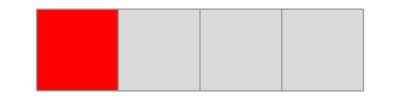
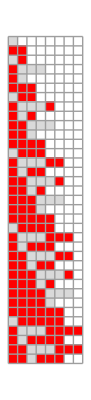
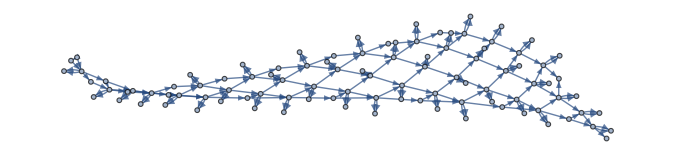
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules: | -Graphics--Graphics-

```mathematica
sss26=SSS[rs26[["RuleSet"]], "A",400, (* choose an appropriate initial state string, and # steps *)
(* options *) SSSMax->35,NetMax->99,NetSize->{600,Automatic},SSSSize->{Automatic,380},HighlightMethod->None,RulePlacement->Left,VertexLabels->Placed[Automatic,Tooltip],DirectedEdges->True,ImageSize->{100,Automatic},NetSize->{Automatic,338},SSSSize->{Automatic,338},IconSize->{Automatic,31.8},VertexSize->Automatic]; (* options can be changed or omitted, but these are reasonable choices *)
```

```mathematica
nds26=ToNetDifferenceSets[sss26[["Net"]]]
```

{{1,2},{1},{1,1,2,3},{},{2,4},{1},{1,1,2,5},{},{1,1,2,4},{},{4,6},{1},{1,1,2,7},{},{1,1,2,6},{},{1,1,2,6},{},{6,8},{1},{1,1,2,9},{},{1,1,2,8},{},{1,1,2,8},{},{1,1,2,8},{},{8,10},{1},{1,1,2,11},{},{1,1,2,10},{},{1,1,2,10},{},{1,1,2,10},{},{1,1,2,10},{},{10,12},{1},{1,1,2,13},{},{1,1,2,12},{},{1,1,2,12},{},{1,1,2,12},{},{1,1,2,12},{},{1,1,2,12},{},{12,14},{1},{1,1,2,15},{},{1,1,2,14},{},{1,1,2,14},{},{1,1,2,14},{},{1,1,2,14},{},{1,1,2,14},{},{1,1,2,14},{},{14,16},{1},{1,1,2,17},{},{1,1,2,16},{},{1,1,2,16},{},{1,1,2,16},{},{1,1,2,16},{},{1,1,2,16},{},{1,1,2,16},{},{1,1,2,16},{},{16,18},{1},{1,1,2,19},{},{1,1,2,18},{},{1,1,2,18},{},{1,1,2,18},{},{1,1,2,18},{},{1,1,2,18},{},{1,1,2,18},{},{1,1,2,18},{},{1,1,2,18},{},{18,20},{1},{1,1,2,21},{},{1,1,2,20},{},{1,1,2,20},{},{1,1,2,20},{},{1,1,2,20},{},{1,1,2,20},{},{1,1,2,20},{},{1,1,2,20},{},{1,1,2,20},{},{1,1,2,20},{},{20,22},{1},{1,1,2,23},{},{1,1,2,22},{},{1,1,2,22},{},{1,1,2,22},{},{1,1,2,22},{},{1,1,2,22},{},{1,1,2,22},{},{1,1,2,22},{},{1,1,2,22},{},{1,1,2,22},{},{1,1,2,22},{},{22,24},{1},{1,1,2,25},{},{1,1,2,24},{},{1,1,2,24},{},{1,1,2,24},{},{1,1,2,24},{},{1,1,2,24},{},{1,1,2,24},{},{1,1,2,24},{},{1,1,2,24},{},{1,1,2,24},{},{1,1,2,24},{},{1,1,2,24},{},{24,26},{1},{1,1,2,27},{},{1,1,2,26},{},{1,1,2,26},{},{1,1,2,26},{},{1,1,2,26},{},{1,1,2,26},{},{1,1,2,26},{},{1,1,2,26},{},{1,1,2,26},{},{1,1,2,26},{},{1,1,2,26},{},{1,1,2,26},{},{1,1,2,26},{},{26,28},{1},{1,1,2,29},{},{1,1,2,28},{},{1,1,2,28},{},{1,1,2,28},{},{1,1,2,28},{},{1,1,2,28},{},{1,1,2,28},{},{1,1,2,28},{},{1,1,2,28},{},{1,1,2,28},{},{1,1,2,28},{},{1,1,2,28},{},{1,1,2,28},{},{1,1,2,28},{},{28,30},{1},{1,1,2,31},{},{1,1,2,30},{},{1,1,2,30},{},{1,1,2,30},{},{1,1,2,30},{},{1,1,2,30},{},{1,1,2,30},{},{1,1,2,30},{},{1,1,2,30},{},{1,1,2,30},{},{1,1,2,30},{},{1,1,2,30},{},{1,1,2,30},{},{1,1,2,30},{},{1,1,2,30},{},{30,32},{1},{1,1,2,33},{},{1,1,2,32},{},{1,1,2,32},{},{1,1,2,32},{},{1,1,2,32},{},{1,1,2,32},{},{1,1,2,32},{},{1,1,2,32},{},{1,1,2,32},{},{1,1,2,32},{},{1,1,2,32},{},{1,1,2,32},{},{1,1,2,32},{},{1,1,2,32},{},{1,1,2,32},{},{1,1,2,32},{},{32,34},{1},{1,1,2,35},{},{1,1,2,34},{},{1,1,2,34},{},{1,1,2,34},{},{1,1,2,34},{},{1,1,2,34},{},{1,1,2,34},{},{1,1,2,34},{},{1,1,2,34},{},{1,1,2,34},{},{1,1,2,34},{},{1,1,2,34},{},{1,1,2,34},{},{1,1,2,34},{},{1,1,2,34},{},{1,1,2,34},{},{1,1,2,34},{},{34,36},{1},{1,1,2,37},{},{1,1,2,36},{},{1,1,2,36},{},{1,1,2,36},{},{1,1,2,36},{},{1,1,2,36},{},{1,1,2,36},{},{1,1,2,36},{},{1,1,2,36},{},{1,1,2,36},{},{1,1,2,36},{},{1,1,2},{},{1,1,2},{},{1,1,2},{},{1,1,2},{},{1,1,2},{},{1,1,2},{},{1,1,2},{},{},{1},{1,1,2},{},{1,1,2},{},{1,1,2},{},{1,1,2},{},{1,1,2},{},{1,1,2},{},{1,1,2},{},{1,1,2},{},{1,1,2},{},{1,1}}

```mathematica
Position[nds26,36]
```

{{341,2},{345,4},{347,4},{349,4},{351,4},{353,4},{355,4},{357,4},{359,4},{361,4},{363,4}}

```mathematica
ReduceSetList[nds26[[10;;341]]]
```

{€_(n$1⊨1)^15[{},{2 (1+n$1),2 (2+n$1)},{1},{1,1,2,5+2 n$1},€^(1+n$1)[{},{1,1,2,2 (2+n$1)}]],{},{34,36}}

```mathematica
%73[[1;;1]] /. {n$1->j, n$2->k}
```

{€_(j⊨1)^15[{},{2 (1+j),2 (2+j)},{1},{1,1,2,5+2 j},€^(1+j)[{},{1,1,2,2 (2+j)}]]}

Check whether the k-concatenation might start earlier:

```mathematica
{{},{2 (1+j),2 (2+j)},{1},{1,1,2,5+2 j},€^(1+j)[{},{1,1,2,2 (2+j)}]}/.j->-1
```

{{},{0,2},{1},{1,1,2,3},€^0[{},{1,1,2,2}]}

Yes! Not the {0,2}, but everything after that...

```mathematica
InputForm[%79]
```

{IndexedConcatenate[{}, {2*(1 + j), 2*(2 + j)}, {1}, {1, 1, 2, 5 + 2*j}, 
  IndexedConcatenate[{}, {1, 1, 2, 2*(2 + j)}, 1 + j], {j, 1, 15}]}

```mathematica
{IndexedConcatenate[ {1}, {1, 1, 2, 1+ 2j}, 
  IndexedConcatenate[{}, {1, 1, 2, 2j}, -1 + j],{}, {2 j, 2 j}, {j, 1, 15}]}
```

{€_(j⊨1)^15[{1},{1,1,2,2 j+1},€^(j-1)[{},{1,1,2,2 j}],{},{2 j,2 j}]}

```mathematica
Expand[%85]
```

{{1},{1,1,2,3},€^0[{},{1,1,2,2}],{},{2,2},{1},{1,1,2,5},€^1[{},{1,1,2,4}],{},{4,4},{1},{1,1,2,7},€^2[{},{1,1,2,6}],{},{6,6},{1},{1,1,2,9},€^3[{},{1,1,2,8}],{},{8,8},{1},{1,1,2,11},€^4[{},{1,1,2,10}],{},{10,10},{1},{1,1,2,13},€^5[{},{1,1,2,12}],{},{12,12},{1},{1,1,2,15},€^6[{},{1,1,2,14}],{},{14,14},{1},{1,1,2,17},€^7[{},{1,1,2,16}],{},{16,16},{1},{1,1,2,19},€^8[{},{1,1,2,18}],{},{18,18},{1},{1,1,2,21},€^9[{},{1,1,2,20}],{},{20,20},{1},{1,1,2,23},€^10[{},{1,1,2,22}],{},{22,22},{1},{1,1,2,25},€^11[{},{1,1,2,24}],{},{24,24},{1},{1,1,2,27},€^12[{},{1,1,2,26}],{},{26,26},{1},{1,1,2,29},€^13[{},{1,1,2,28}],{},{28,28},{1},{1,1,2,31},€^14[{},{1,1,2,30}],{},{30,30}}

```mathematica
GraphPlot@FromNetDifferenceSets@ExpandAll@
{IndexedConcatenate[ {1}, {1, 1, 2, 1+ 2j}, 
  IndexedConcatenate[{}, {1, 1, 2, 2j}, -1 + j],{}, {2 j, 2 j}, {j, 1, 20}]}
```

-Graphics-

### 726522984895

### 726523346979

```mathematica
rs28=FromReducedRankIndex[726523346979]
```

<|Index→726523346979,QCode→32234243322434242,RuleSet→{AA→A,AB→BAA,A→BB,B→A}|>

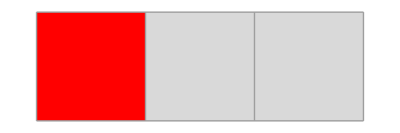
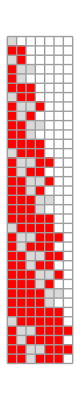
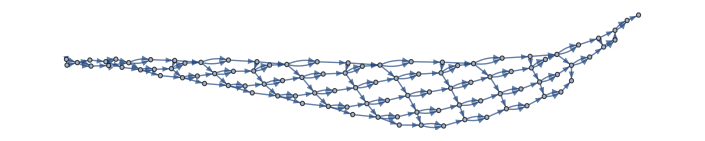
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules: | -Graphics--Graphics-

```mathematica
sss28=SSS[rs28[["RuleSet"]], "A",400, (* choose an appropriate initial state string, and # steps *)
(* options *) SSSMax->35,NetMax->99,NetSize->{600,Automatic},SSSSize->{Automatic,380},HighlightMethod->None,RulePlacement->Left,VertexLabels->Placed[Automatic,Tooltip],DirectedEdges->True,ImageSize->{100,Automatic},NetSize->{Automatic,338},SSSSize->{Automatic,338},IconSize->{Automatic,31.8},VertexSize->Automatic]; (* options can be changed or omitted, but these are reasonable choices *)
```

```mathematica
nds28=ToNetDifferenceSets[sss28[["Net"]]]
```

{{1,2},{1},{1,1,3},{1},{2,4},{1},{1,1,5},{1},{1,1,4},{1},{4,6},{1},{1,1,7},{1},{1,1,6},{1},{1,1,6},{1},{6,8},{1},{1,1,9},{1},{1,1,8},{1},{1,1,8},{1},{1,1,8},{1},{8,10},{1},{1,1,11},{1},{1,1,10},{1},{1,1,10},{1},{1,1,10},{1},{1,1,10},{1},{10,12},{1},{1,1,13},{1},{1,1,12},{1},{1,1,12},{1},{1,1,12},{1},{1,1,12},{1},{1,1,12},{1},{12,14},{1},{1,1,15},{1},{1,1,14},{1},{1,1,14},{1},{1,1,14},{1},{1,1,14},{1},{1,1,14},{1},{1,1,14},{1},{14,16},{1},{1,1,17},{1},{1,1,16},{1},{1,1,16},{1},{1,1,16},{1},{1,1,16},{1},{1,1,16},{1},{1,1,16},{1},{1,1,16},{1},{16,18},{1},{1,1,19},{1},{1,1,18},{1},{1,1,18},{1},{1,1,18},{1},{1,1,18},{1},{1,1,18},{1},{1,1,18},{1},{1,1,18},{1},{1,1,18},{1},{18,20},{1},{1,1,21},{1},{1,1,20},{1},{1,1,20},{1},{1,1,20},{1},{1,1,20},{1},{1,1,20},{1},{1,1,20},{1},{1,1,20},{1},{1,1,20},{1},{1,1,20},{1},{20,22},{1},{1,1,23},{1},{1,1,22},{1},{1,1,22},{1},{1,1,22},{1},{1,1,22},{1},{1,1,22},{1},{1,1,22},{1},{1,1,22},{1},{1,1,22},{1},{1,1,22},{1},{1,1,22},{1},{22,24},{1},{1,1,25},{1},{1,1,24},{1},{1,1,24},{1},{1,1,24},{1},{1,1,24},{1},{1,1,24},{1},{1,1,24},{1},{1,1,24},{1},{1,1,24},{1},{1,1,24},{1},{1,1,24},{1},{1,1,24},{1},{24,26},{1},{1,1,27},{1},{1,1,26},{1},{1,1,26},{1},{1,1,26},{1},{1,1,26},{1},{1,1,26},{1},{1,1,26},{1},{1,1,26},{1},{1,1,26},{1},{1,1,26},{1},{1,1,26},{1},{1,1,26},{1},{1,1,26},{1},{26,28},{1},{1,1,29},{1},{1,1,28},{1},{1,1,28},{1},{1,1,28},{1},{1,1,28},{1},{1,1,28},{1},{1,1,28},{1},{1,1,28},{1},{1,1,28},{1},{1,1,28},{1},{1,1,28},{1},{1,1,28},{1},{1,1,28},{1},{1,1,28},{1},{28,30},{1},{1,1,31},{1},{1,1,30},{1},{1,1,30},{1},{1,1,30},{1},{1,1,30},{1},{1,1,30},{1},{1,1,30},{1},{1,1,30},{1},{1,1,30},{1},{1,1,30},{1},{1,1,30},{1},{1,1,30},{1},{1,1,30},{1},{1,1,30},{1},{1,1,30},{1},{30,32},{1},{1,1,33},{1},{1,1,32},{1},{1,1,32},{1},{1,1,32},{1},{1,1,32},{1},{1,1,32},{1},{1,1,32},{1},{1,1,32},{1},{1,1,32},{1},{1,1,32},{1},{1,1,32},{1},{1,1,32},{1},{1,1,32},{1},{1,1,32},{1},{1,1,32},{1},{1,1,32},{1},{32,34},{1},{1,1,35},{1},{1,1,34},{1},{1,1,34},{1},{1,1,34},{1},{1,1,34},{1},{1,1,34},{1},{1,1,34},{1},{1,1,34},{1},{1,1,34},{1},{1,1,34},{1},{1,1,34},{1},{1,1,34},{1},{1,1,34},{1},{1,1,34},{1},{1,1,34},{1},{1,1,34},{1},{1,1,34},{1},{34,36},{1},{1,1,37},{1},{1,1,36},{1},{1,1,36},{1},{1,1,36},{1},{1,1,36},{1},{1,1,36},{1},{1,1,36},{1},{1,1,36},{1},{1,1,36},{1},{1,1,36},{1},{1,1,36},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1}}

```mathematica
Position[nds28,36]
```

{{341,2},{345,3},{347,3},{349,3},{351,3},{353,3},{355,3},{357,3},{359,3},{361,3},{363,3}}

```mathematica
ReduceSetList[nds28[[10;;339]]]/.n$1->k
```

{€_(k⊨1)^15[{1},{2 (1+k),2 (2+k)},{1},{1,1,5+2 k},€^(1+k)[{1},{1,1,2 (2+k)}]]}

Check whether the k-concatenation might start earlier:

```mathematica
{{1},{2 (1+k),2 (2+k)},{1},{1,1,5+2 k},€^(1+k)[{1},{1,1,2 (2+k)}]} /. k->0//Simplify
```

{{1},{2,4},{1},{1,1,5},€^1[{1},{1,1,4}]}

Those all work.

```mathematica
{{1},{2 (1+k),2 (2+k)},{1},{1,1,5+2 k},€^(1+k)[{1},{1,1,2 (2+k)}]} /. k->-1//Simplify
```

{{1},{0,2},{1},{1,1,3},€^0[{1},{1,1,2}]}

Those work, starting with the {1}.

```mathematica
{{1},{2 (1+k),2 (2+k)},{1},{1,1,5+2 k},€^(1+k)[{1},{1,1,2 (2+k)}]}/.k->k-2//Simplify
```

{{1},{2 (-1+k),2 k},{1},{1,1,1+2 k},€^(-1+k)[{1},{1,1,2 k}]}

```mathematica
{{1},{1,1,1+2 k},€^(-1+k)[{1},{1,1,2 k}],{1},{2k,2 (k+1)}}/.k->1
```

{{1},{1,1,3},€^0[{1},{1,1,2}],{1},{2,4}}

```mathematica
{{1},{1,1,1+2 k},€^(-1+k)[{1},{1,1,2 k}],{1},{2k,2 (k+1)}}
```

```mathematica
{IndexedConcatenate[{1},{1,1,1+2 k},IndexedConcatenate[{1},{1,1,2 k},k-1],{1},{2k,2 (k+1)},{k,1,4}]}
```

{€_(k⊨1)^4[{1},{1,1,2 k+1},€^(k-1)[{1},{1,1,2 k}],{1},{2 k,2 (k+1)}]}

```mathematica
%//ExpandAll
```

{{1},{1,1,3},{1},{2,4},{1},{1,1,5},{1},{1,1,4},{1},{4,6},{1},{1,1,7},{1},{1,1,6},{1},{1,1,6},{1},{6,8},{1},{1,1,9},{1},{1,1,8},{1},{1,1,8},{1},{1,1,8},{1},{8,10}}

```mathematica
GraphPlot@FromNetDifferenceSets@ExpandAll@
{IndexedConcatenate[{1},{1,1,1+2 k},IndexedConcatenate[{1},{1,1,2 k},k-1],{1},{2k,2 (k+1)},{k,1,12}]}
```

-Graphics-

### 733406619250

### 733406622395

### 733406627471

### 733406627500

### 733406628225

### 733408518645

### 733448810021

### 733448814971

### 733448815501

### 733448903225

## Maybe not 2-D?

{“AB”->”AAA”, “A”->””, “B”->””}

{“AB”->”BBA”, “B”->”AA”}

{“AA”->””, “AB”->”BBA”, “B”->”AAA”}

{“AA”->”AB”, “BB”->”AAAA”, “B”->””}

```mathematica
rs30= FromReducedRankRuleSet[{"AB"->"BBA","B"->"AA"}]
```

<|Index→50471770,QCode→34243432423,RuleSet→{AB→BBA,B→AA}|>

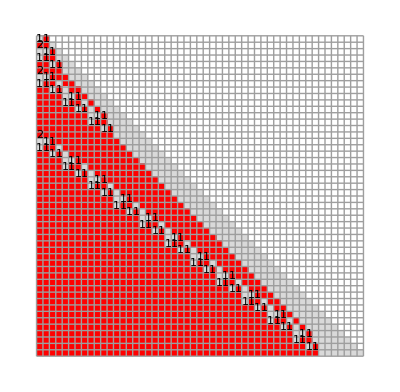
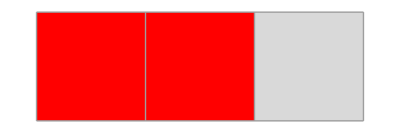
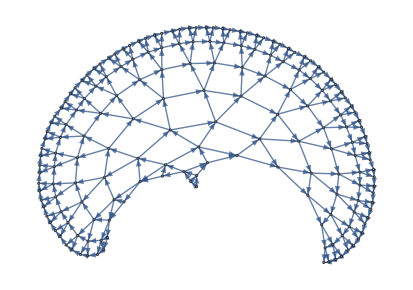
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
sss30=SSS[rs30,"AB",3000,SSSMax->50,NetMax->179,VertexLabels->Placed[Automatic,Tooltip]];
```

```mathematica
nds30=ToNetDifferenceSets[sss30["Net"]]
```

```mathematica
Position[nds30,{_}]//Short
```

{{762},{763},{765},{766},{768},{769},{771},{772},«1474»,{2987},{2989},{2990},{2992},{2993},{2995},{2996},{2998}}

```mathematica
ReduceSetList[nds30[[1;;750]]]
```

DifferenceRoot::ieqn: The supplied equation in Function[{y,n},{0+(0+Times[«2»]+Times[«2»]) y[n]+(0+Times[«2»]+Times[«2»]) y[Plus[«2»]]+(0+Times[«2»]) y[Plus[«2»]]==0,y[1]==0,y[0]==29/2394}] is not a linear difference equation with polynomial coefficients.

DifferenceRoot::ieqn: The supplied equation in Function[{y,n},{0+(0+Times[«2»]+Times[«2»]) y[n]+(0+Times[«2»]+Times[«2»]) y[Plus[«2»]]+(0+Times[«2»]) y[Plus[«2»]]==0,y[1]==0,y[0]==971/263670}] is not a linear difference equation with polynomial coefficients.

DifferenceRoot::ieqn: The supplied equation in Function[{y,n},{0+(0+Times[«2»]+Times[«2»]) y[n]+(0+Times[«2»]+Times[«2»]) y[Plus[«2»]]+(0+Times[«2»]) y[Plus[«2»]]==0,y[1]==0,y[0]==4043/4200438}] is not a linear difference equation with polynomial coefficients.

General::stop: Further output of DifferenceRoot::ieqn will be suppressed during this calculation.

{€^3[{1,2}],{1,2,3},{5,8},{1,2},€_(n$2⊨1)^2[€_(n$1⊨1)^2[{1,2+(-1+n$1) (6+7 (-1+n$2)),3+(-1+n$1) (6+9 (-1+n$2))}],{2,11+9 (-1+n$2),14+9 (-1+n$2)}],{1,2},{1,24,27},{29,32},{1,2},€_(n$1⊨1)^2[{1,2+30 (-1+n$1),3+30 (-1+n$1)}],{2,35,38},€_(n$1⊨1)^2[{1,2+37 (-1+n$1),3+39 (-1+n$1)}],{2,44,47},€_(n$1⊨1)^2[{1,2+46 (-1+n$1),3+48 (-1+n$1)}],{2,53,56},€_(n$1⊨1)^2[{1,2+55 (-1+n$1),3+57 (-1+n$1)}],{2,62,65},€_(n$1⊨1)^2[{1,2+64 (-1+n$1),3+66 (-1+n$1)}],{2,71,74},€_(n$1⊨1)^2[{1,2+73 (-1+n$1),3+75 (-1+n$1)}],{2,80,83},€_(n$1⊨1)^2[{1,2+82 (-1+n$1),3+84 (-1+n$1)}],{2,89,92},€_(n$1⊨1)^2[{1,2+91 (-1+n$1),3+93 (-1+n$1)}],{2,98,101},€_(n$1⊨1)^2[{1,2+100 (-1+n$1),3+102 (-1+n$1)}],{2,107,110},€_(n$1⊨1)^2[{1,2+109 (-1+n$1),3+111 (-1+n$1)}],{2,116,119},{1,2},{1,120,123},{125,128},{1,2},€_(n$2⊨1)^42[€_(n$1⊨1)^2[{1,2+126 (-1+n$1) ∏_(K[1]=1)^(-1+n$2) (19/18+[K[1]]),3+9 (-1+n$1) (13+n$2)}],{2,122+9 n$2,125+9 n$2}],{1,2},{1,504,507},{509,512},{1,2},€_(n$2⊨1)^170[€_(n$1⊨1)^2[{1,2+510 (-1+n$1) ∏_(K[1]=1)^(-1+n$2) (517/510+[K[1]]),3+3 (-1+n$1) (167+3 n$2)}],{2,506+9 n$2,509+9 n$2}],{1,2},{1,2040,2043},{2045,2048},{1,2},€_(n$2⊨1)^18[€_(n$1⊨1)^2[{1,2+2046 (-1+n$1) ∏_(K[1]=1)^(-1+n$2) (2053/2046+[K[1]]),3+3 (-1+n$1) (679+3 n$2)}],{2,2042+9 n$2,2045+9 n$2}],€_(n$1⊨1)^2[{1,2+2206 (-1+n$1),3+2208 (-1+n$1)}]}

```mathematica
$debug=True;
ReduceSetList[nds30[[1;;750]]]
$debug=False;
```

Entering ReduceSetList with: {{1,2},{1,2},{1,2},{1,2,3},{5,8},{1,2},{1,2,3},{1,8,9},{2,11,14},{1,2,3},{1,15,18},{2,20,23},{1,2},{1,24,27},{29,32},{1,2},{1,2,3},{1,32,33},{2,35,38},{1,2,3},{1,39,42},{2,44,47},{1,2,3},{1,48,51},{2,53,56},{1,2,3},{1,57,60},{2,62,65},{1,2,3},{1,66,69},{2,71,74},{1,2,3},{1,75,78},{2,80,83},{1,2,3},{1,84,87},{2,89,92},{1,2,3},{1,93,96},{2,98,101},{1,2,3},{1,102,105},{2,107,110},{1,2,3},{1,111,114},{2,116,119},{1,2},{1,120,123},{125,128},{1,2},{1,2,3},{1,128,129},{2,131,134},{1,2,3},{1,135,138},{2,140,143},{1,2,3},{1,144,147},{2,149,152},{1,2,3},{1,153,156},{2,158,161},{1,2,3},{1,162,165},{2,167,170},{1,2,3},{1,171,174},{2,176,179},{1,2,3},{1,180,183},{2,185,188},{1,2,3},{1,189,192},{2,194,197},{1,2,3},{1,198,201},{2,203,206},{1,2,3},{1,207,210},{2,212,215},{1,2,3},{1,216,219},{2,221,224},{1,2,3},{1,225,228},{2,230,233},{1,2,3},{1,234,237},{2,239,242},{1,2,3},{1,243,246},{2,248,251},{1,2,3},{1,252,255},{2,257,260},{1,2,3},{1,261,264},{2,266,269},{1,2,3},{1,270,273},{2,275,278},{1,2,3},{1,279,282},{2,284,287},{1,2,3},{1,288,291},{2,293,296},{1,2,3},{1,297,300},{2,302,305},{1,2,3},{1,306,309},{2,311,314},{1,2,3},{1,315,318},{2,320,323},{1,2,3},{1,324,327},{2,329,332},{1,2,3},{1,333,336},{2,338,341},{1,2,3},{1,342,345},{2,347,350},{1,2,3},{1,351,354},{2,356,359},{1,2,3},{1,360,363},{2,365,368},{1,2,3},{1,369,372},{2,374,377},{1,2,3},{1,378,381},{2,383,386},{1,2,3},{1,387,390},{2,392,395},{1,2,3},{1,396,399},{2,401,404},{1,2,3},{1,405,408},{2,410,413},{1,2,3},{1,414,417},{2,419,422},{1,2,3},{1,423,426},{2,428,431},{1,2,3},{1,432,435},{2,437,440},{1,2,3},{1,441,444},{2,446,449},{1,2,3},{1,450,453},{2,455,458},{1,2,3},{1,459,462},{2,464,467},{1,2,3},{1,468,471},{2,473,476},{1,2,3},{1,477,480},{2,482,485},{1,2,3},{1,486,489},{2,491,494},{1,2,3},{1,495,498},{2,500,503},{1,2},{1,504,507},{509,512},{1,2},{1,2,3},{1,512,513},{2,515,518},{1,2,3},{1,519,522},{2,524,527},{1,2,3},{1,528,531},{2,533,536},{1,2,3},{1,537,540},{2,542,545},{1,2,3},{1,546,549},{2,551,554},{1,2,3},{1,555,558},{2,560,563},{1,2,3},{1,564,567},{2,569,572},{1,2,3},{1,573,576},{2,578,581},{1,2,3},{1,582,585},{2,587,590},{1,2,3},{1,591,594},{2,596,599},{1,2,3},{1,600,603},{2,605,608},{1,2,3},{1,609,612},{2,614,617},{1,2,3},{1,618,621},{2,623,626},{1,2,3},{1,627,630},{2,632,635},{1,2,3},{1,636,639},{2,641,644},{1,2,3},{1,645,648},{2,650,653},{1,2,3},{1,654,657},{2,659,662},{1,2,3},{1,663,666},{2,668,671},{1,2,3},{1,672,675},{2,677,680},{1,2,3},{1,681,684},{2,686,689},{1,2,3},{1,690,693},{2,695,698},{1,2,3},{1,699,702},{2,704,707},{1,2,3},{1,708,711},{2,713,716},{1,2,3},{1,717,720},{2,722,725},{1,2,3},{1,726,729},{2,731,734},{1,2,3},{1,735,738},{2,740,743},{1,2,3},{1,744,747},{2,749,752},{1,2,3},{1,753,756},{2,758,761},{1,2,3},{1,762,765},{2,767,770},{1,2,3},{1,771,774},{2,776,779},{1,2,3},{1,780,783},{2,785,788},{1,2,3},{1,789,792},{2,794,797},{1,2,3},{1,798,801},{2,803,806},{1,2,3},{1,807,810},{2,812,815},{1,2,3},{1,816,819},{2,821,824},{1,2,3},{1,825,828},{2,830,833},{1,2,3},{1,834,837},{2,839,842},{1,2,3},{1,843,846},{2,848,851},{1,2,3},{1,852,855},{2,857,860},{1,2,3},{1,861,864},{2,866,869},{1,2,3},{1,870,873},{2,875,878},{1,2,3},{1,879,882},{2,884,887},{1,2,3},{1,888,891},{2,893,896},{1,2,3},{1,897,900},{2,902,905},{1,2,3},{1,906,909},{2,911,914},{1,2,3},{1,915,918},{2,920,923},{1,2,3},{1,924,927},{2,929,932},{1,2,3},{1,933,936},{2,938,941},{1,2,3},{1,942,945},{2,947,950},{1,2,3},{1,951,954},{2,956,959},{1,2,3},{1,960,963},{2,965,968},{1,2,3},{1,969,972},{2,974,977},{1,2,3},{1,978,981},{2,983,986},{1,2,3},{1,987,990},{2,992,995},{1,2,3},{1,996,999},{2,1001,1004},{1,2,3},{1,1005,1008},{2,1010,1013},{1,2,3},{1,1014,1017},{2,1019,1022},{1,2,3},{1,1023,1026},{2,1028,1031},{1,2,3},{1,1032,1035},{2,1037,1040},{1,2,3},{1,1041,1044},{2,1046,1049},{1,2,3},{1,1050,1053},{2,1055,1058},{1,2,3},{1,1059,1062},{2,1064,1067},{1,2,3},{1,1068,1071},{2,1073,1076},{1,2,3},{1,1077,1080},{2,1082,1085},{1,2,3},{1,1086,1089},{2,1091,1094},{1,2,3},{1,1095,1098},{2,1100,1103},{1,2,3},{1,1104,1107},{2,1109,1112},{1,2,3},{1,1113,1116},{2,1118,1121},{1,2,3},{1,1122,1125},{2,1127,1130},{1,2,3},{1,1131,1134},{2,1136,1139},{1,2,3},{1,1140,1143},{2,1145,1148},{1,2,3},{1,1149,1152},{2,1154,1157},{1,2,3},{1,1158,1161},{2,1163,1166},{1,2,3},{1,1167,1170},{2,1172,1175},{1,2,3},{1,1176,1179},{2,1181,1184},{1,2,3},{1,1185,1188},{2,1190,1193},{1,2,3},{1,1194,1197},{2,1199,1202},{1,2,3},{1,1203,1206},{2,1208,1211},{1,2,3},{1,1212,1215},{2,1217,1220},{1,2,3},{1,1221,1224},{2,1226,1229},{1,2,3},{1,1230,1233},{2,1235,1238},{1,2,3},{1,1239,1242},{2,1244,1247},{1,2,3},{1,1248,1251},{2,1253,1256},{1,2,3},{1,1257,1260},{2,1262,1265},{1,2,3},{1,1266,1269},{2,1271,1274},{1,2,3},{1,1275,1278},{2,1280,1283},{1,2,3},{1,1284,1287},{2,1289,1292},{1,2,3},{1,1293,1296},{2,1298,1301},{1,2,3},{1,1302,1305},{2,1307,1310},{1,2,3},{1,1311,1314},{2,1316,1319},{1,2,3},{1,1320,1323},{2,1325,1328},{1,2,3},{1,1329,1332},{2,1334,1337},{1,2,3},{1,1338,1341},{2,1343,1346},{1,2,3},{1,1347,1350},{2,1352,1355},{1,2,3},{1,1356,1359},{2,1361,1364},{1,2,3},{1,1365,1368},{2,1370,1373},{1,2,3},{1,1374,1377},{2,1379,1382},{1,2,3},{1,1383,1386},{2,1388,1391},{1,2,3},{1,1392,1395},{2,1397,1400},{1,2,3},{1,1401,1404},{2,1406,1409},{1,2,3},{1,1410,1413},{2,1415,1418},{1,2,3},{1,1419,1422},{2,1424,1427},{1,2,3},{1,1428,1431},{2,1433,1436},{1,2,3},{1,1437,1440},{2,1442,1445},{1,2,3},{1,1446,1449},{2,1451,1454},{1,2,3},{1,1455,1458},{2,1460,1463},{1,2,3},{1,1464,1467},{2,1469,1472},{1,2,3},{1,1473,1476},{2,1478,1481},{1,2,3},{1,1482,1485},{2,1487,1490},{1,2,3},{1,1491,1494},{2,1496,1499},{1,2,3},{1,1500,1503},{2,1505,1508},{1,2,3},{1,1509,1512},{2,1514,1517},{1,2,3},{1,1518,1521},{2,1523,1526},{1,2,3},{1,1527,1530},{2,1532,1535},{1,2,3},{1,1536,1539},{2,1541,1544},{1,2,3},{1,1545,1548},{2,1550,1553},{1,2,3},{1,1554,1557},{2,1559,1562},{1,2,3},{1,1563,1566},{2,1568,1571},{1,2,3},{1,1572,1575},{2,1577,1580},{1,2,3},{1,1581,1584},{2,1586,1589},{1,2,3},{1,1590,1593},{2,1595,1598},{1,2,3},{1,1599,1602},{2,1604,1607},{1,2,3},{1,1608,1611},{2,1613,1616},{1,2,3},{1,1617,1620},{2,1622,1625},{1,2,3},{1,1626,1629},{2,1631,1634},{1,2,3},{1,1635,1638},{2,1640,1643},{1,2,3},{1,1644,1647},{2,1649,1652},{1,2,3},{1,1653,1656},{2,1658,1661},{1,2,3},{1,1662,1665},{2,1667,1670},{1,2,3},{1,1671,1674},{2,1676,1679},{1,2,3},{1,1680,1683},{2,1685,1688},{1,2,3},{1,1689,1692},{2,1694,1697},{1,2,3},{1,1698,1701},{2,1703,1706},{1,2,3},{1,1707,1710},{2,1712,1715},{1,2,3},{1,1716,1719},{2,1721,1724},{1,2,3},{1,1725,1728},{2,1730,1733},{1,2,3},{1,1734,1737},{2,1739,1742},{1,2,3},{1,1743,1746},{2,1748,1751},{1,2,3},{1,1752,1755},{2,1757,1760},{1,2,3},{1,1761,1764},{2,1766,1769},{1,2,3},{1,1770,1773},{2,1775,1778},{1,2,3},{1,1779,1782},{2,1784,1787},{1,2,3},{1,1788,1791},{2,1793,1796},{1,2,3},{1,1797,1800},{2,1802,1805},{1,2,3},{1,1806,1809},{2,1811,1814},{1,2,3},{1,1815,1818},{2,1820,1823},{1,2,3},{1,1824,1827},{2,1829,1832},{1,2,3},{1,1833,1836},{2,1838,1841},{1,2,3},{1,1842,1845},{2,1847,1850},{1,2,3},{1,1851,1854},{2,1856,1859},{1,2,3},{1,1860,1863},{2,1865,1868},{1,2,3},{1,1869,1872},{2,1874,1877},{1,2,3},{1,1878,1881},{2,1883,1886},{1,2,3},{1,1887,1890},{2,1892,1895},{1,2,3},{1,1896,1899},{2,1901,1904},{1,2,3},{1,1905,1908},{2,1910,1913},{1,2,3},{1,1914,1917},{2,1919,1922},{1,2,3},{1,1923,1926},{2,1928,1931},{1,2,3},{1,1932,1935},{2,1937,1940},{1,2,3},{1,1941,1944},{2,1946,1949},{1,2,3},{1,1950,1953},{2,1955,1958},{1,2,3},{1,1959,1962},{2,1964,1967},{1,2,3},{1,1968,1971},{2,1973,1976},{1,2,3},{1,1977,1980},{2,1982,1985},{1,2,3},{1,1986,1989},{2,1991,1994},{1,2,3},{1,1995,1998},{2,2000,2003},{1,2,3},{1,2004,2007},{2,2009,2012},{1,2,3},{1,2013,2016},{2,2018,2021},{1,2,3},{1,2022,2025},{2,2027,2030},{1,2,3},{1,2031,2034},{2,2036,2039},{1,2},{1,2040,2043},{2045,2048},{1,2},{1,2,3},{1,2048,2049},{2,2051,2054},{1,2,3},{1,2055,2058},{2,2060,2063},{1,2,3},{1,2064,2067},{2,2069,2072},{1,2,3},{1,2073,2076},{2,2078,2081},{1,2,3},{1,2082,2085},{2,2087,2090},{1,2,3},{1,2091,2094},{2,2096,2099},{1,2,3},{1,2100,2103},{2,2105,2108},{1,2,3},{1,2109,2112},{2,2114,2117},{1,2,3},{1,2118,2121},{2,2123,2126},{1,2,3},{1,2127,2130},{2,2132,2135},{1,2,3},{1,2136,2139},{2,2141,2144},{1,2,3},{1,2145,2148},{2,2150,2153},{1,2,3},{1,2154,2157},{2,2159,2162},{1,2,3},{1,2163,2166},{2,2168,2171},{1,2,3},{1,2172,2175},{2,2177,2180},{1,2,3},{1,2181,2184},{2,2186,2189},{1,2,3},{1,2190,2193},{2,2195,2198},{1,2,3},{1,2199,2202},{2,2204,2207},{1,2,3},{1,2208,2211}}

exact repLen = 1: {€^3[{1,2}],{1,2,3},{5,8},{1,2},{1,2,3},{1,8,9},{2,11,14},{1,2,3},{1,15,18},{2,20,23},{1,2},{1,24,27},{29,32},{1,2},{1,2,3},{1,32,33},{2,35,38},{1,2,3},{1,39,42},{2,44,47},{1,2,3},{1,48,51},{2,53,56},{1,2,3},{1,57,60},{2,62,65},{1,2,3},{1,66,69},{2,71,74},{1,2,3},{1,75,78},{2,80,83},{1,2,3},{1,84,87},{2,89,92},{1,2,3},{1,93,96},{2,98,101},{1,2,3},{1,102,105},{2,107,110},{1,2,3},{1,111,114},{2,116,119},{1,2},{1,120,123},{125,128},{1,2},{1,2,3},{1,128,129},{2,131,134},{1,2,3},{1,135,138},{2,140,143},{1,2,3},{1,144,147},{2,149,152},{1,2,3},{1,153,156},{2,158,161},{1,2,3},{1,162,165},{2,167,170},{1,2,3},{1,171,174},{2,176,179},{1,2,3},{1,180,183},{2,185,188},{1,2,3},{1,189,192},{2,194,197},{1,2,3},{1,198,201},{2,203,206},{1,2,3},{1,207,210},{2,212,215},{1,2,3},{1,216,219},{2,221,224},{1,2,3},{1,225,228},{2,230,233},{1,2,3},{1,234,237},{2,239,242},{1,2,3},{1,243,246},{2,248,251},{1,2,3},{1,252,255},{2,257,260},{1,2,3},{1,261,264},{2,266,269},{1,2,3},{1,270,273},{2,275,278},{1,2,3},{1,279,282},{2,284,287},{1,2,3},{1,288,291},{2,293,296},{1,2,3},{1,297,300},{2,302,305},{1,2,3},{1,306,309},{2,311,314},{1,2,3},{1,315,318},{2,320,323},{1,2,3},{1,324,327},{2,329,332},{1,2,3},{1,333,336},{2,338,341},{1,2,3},{1,342,345},{2,347,350},{1,2,3},{1,351,354},{2,356,359},{1,2,3},{1,360,363},{2,365,368},{1,2,3},{1,369,372},{2,374,377},{1,2,3},{1,378,381},{2,383,386},{1,2,3},{1,387,390},{2,392,395},{1,2,3},{1,396,399},{2,401,404},{1,2,3},{1,405,408},{2,410,413},{1,2,3},{1,414,417},{2,419,422},{1,2,3},{1,423,426},{2,428,431},{1,2,3},{1,432,435},{2,437,440},{1,2,3},{1,441,444},{2,446,449},{1,2,3},{1,450,453},{2,455,458},{1,2,3},{1,459,462},{2,464,467},{1,2,3},{1,468,471},{2,473,476},{1,2,3},{1,477,480},{2,482,485},{1,2,3},{1,486,489},{2,491,494},{1,2,3},{1,495,498},{2,500,503},{1,2},{1,504,507},{509,512},{1,2},{1,2,3},{1,512,513},{2,515,518},{1,2,3},{1,519,522},{2,524,527},{1,2,3},{1,528,531},{2,533,536},{1,2,3},{1,537,540},{2,542,545},{1,2,3},{1,546,549},{2,551,554},{1,2,3},{1,555,558},{2,560,563},{1,2,3},{1,564,567},{2,569,572},{1,2,3},{1,573,576},{2,578,581},{1,2,3},{1,582,585},{2,587,590},{1,2,3},{1,591,594},{2,596,599},{1,2,3},{1,600,603},{2,605,608},{1,2,3},{1,609,612},{2,614,617},{1,2,3},{1,618,621},{2,623,626},{1,2,3},{1,627,630},{2,632,635},{1,2,3},{1,636,639},{2,641,644},{1,2,3},{1,645,648},{2,650,653},{1,2,3},{1,654,657},{2,659,662},{1,2,3},{1,663,666},{2,668,671},{1,2,3},{1,672,675},{2,677,680},{1,2,3},{1,681,684},{2,686,689},{1,2,3},{1,690,693},{2,695,698},{1,2,3},{1,699,702},{2,704,707},{1,2,3},{1,708,711},{2,713,716},{1,2,3},{1,717,720},{2,722,725},{1,2,3},{1,726,729},{2,731,734},{1,2,3},{1,735,738},{2,740,743},{1,2,3},{1,744,747},{2,749,752},{1,2,3},{1,753,756},{2,758,761},{1,2,3},{1,762,765},{2,767,770},{1,2,3},{1,771,774},{2,776,779},{1,2,3},{1,780,783},{2,785,788},{1,2,3},{1,789,792},{2,794,797},{1,2,3},{1,798,801},{2,803,806},{1,2,3},{1,807,810},{2,812,815},{1,2,3},{1,816,819},{2,821,824},{1,2,3},{1,825,828},{2,830,833},{1,2,3},{1,834,837},{2,839,842},{1,2,3},{1,843,846},{2,848,851},{1,2,3},{1,852,855},{2,857,860},{1,2,3},{1,861,864},{2,866,869},{1,2,3},{1,870,873},{2,875,878},{1,2,3},{1,879,882},{2,884,887},{1,2,3},{1,888,891},{2,893,896},{1,2,3},{1,897,900},{2,902,905},{1,2,3},{1,906,909},{2,911,914},{1,2,3},{1,915,918},{2,920,923},{1,2,3},{1,924,927},{2,929,932},{1,2,3},{1,933,936},{2,938,941},{1,2,3},{1,942,945},{2,947,950},{1,2,3},{1,951,954},{2,956,959},{1,2,3},{1,960,963},{2,965,968},{1,2,3},{1,969,972},{2,974,977},{1,2,3},{1,978,981},{2,983,986},{1,2,3},{1,987,990},{2,992,995},{1,2,3},{1,996,999},{2,1001,1004},{1,2,3},{1,1005,1008},{2,1010,1013},{1,2,3},{1,1014,1017},{2,1019,1022},{1,2,3},{1,1023,1026},{2,1028,1031},{1,2,3},{1,1032,1035},{2,1037,1040},{1,2,3},{1,1041,1044},{2,1046,1049},{1,2,3},{1,1050,1053},{2,1055,1058},{1,2,3},{1,1059,1062},{2,1064,1067},{1,2,3},{1,1068,1071},{2,1073,1076},{1,2,3},{1,1077,1080},{2,1082,1085},{1,2,3},{1,1086,1089},{2,1091,1094},{1,2,3},{1,1095,1098},{2,1100,1103},{1,2,3},{1,1104,1107},{2,1109,1112},{1,2,3},{1,1113,1116},{2,1118,1121},{1,2,3},{1,1122,1125},{2,1127,1130},{1,2,3},{1,1131,1134},{2,1136,1139},{1,2,3},{1,1140,1143},{2,1145,1148},{1,2,3},{1,1149,1152},{2,1154,1157},{1,2,3},{1,1158,1161},{2,1163,1166},{1,2,3},{1,1167,1170},{2,1172,1175},{1,2,3},{1,1176,1179},{2,1181,1184},{1,2,3},{1,1185,1188},{2,1190,1193},{1,2,3},{1,1194,1197},{2,1199,1202},{1,2,3},{1,1203,1206},{2,1208,1211},{1,2,3},{1,1212,1215},{2,1217,1220},{1,2,3},{1,1221,1224},{2,1226,1229},{1,2,3},{1,1230,1233},{2,1235,1238},{1,2,3},{1,1239,1242},{2,1244,1247},{1,2,3},{1,1248,1251},{2,1253,1256},{1,2,3},{1,1257,1260},{2,1262,1265},{1,2,3},{1,1266,1269},{2,1271,1274},{1,2,3},{1,1275,1278},{2,1280,1283},{1,2,3},{1,1284,1287},{2,1289,1292},{1,2,3},{1,1293,1296},{2,1298,1301},{1,2,3},{1,1302,1305},{2,1307,1310},{1,2,3},{1,1311,1314},{2,1316,1319},{1,2,3},{1,1320,1323},{2,1325,1328},{1,2,3},{1,1329,1332},{2,1334,1337},{1,2,3},{1,1338,1341},{2,1343,1346},{1,2,3},{1,1347,1350},{2,1352,1355},{1,2,3},{1,1356,1359},{2,1361,1364},{1,2,3},{1,1365,1368},{2,1370,1373},{1,2,3},{1,1374,1377},{2,1379,1382},{1,2,3},{1,1383,1386},{2,1388,1391},{1,2,3},{1,1392,1395},{2,1397,1400},{1,2,3},{1,1401,1404},{2,1406,1409},{1,2,3},{1,1410,1413},{2,1415,1418},{1,2,3},{1,1419,1422},{2,1424,1427},{1,2,3},{1,1428,1431},{2,1433,1436},{1,2,3},{1,1437,1440},{2,1442,1445},{1,2,3},{1,1446,1449},{2,1451,1454},{1,2,3},{1,1455,1458},{2,1460,1463},{1,2,3},{1,1464,1467},{2,1469,1472},{1,2,3},{1,1473,1476},{2,1478,1481},{1,2,3},{1,1482,1485},{2,1487,1490},{1,2,3},{1,1491,1494},{2,1496,1499},{1,2,3},{1,1500,1503},{2,1505,1508},{1,2,3},{1,1509,1512},{2,1514,1517},{1,2,3},{1,1518,1521},{2,1523,1526},{1,2,3},{1,1527,1530},{2,1532,1535},{1,2,3},{1,1536,1539},{2,1541,1544},{1,2,3},{1,1545,1548},{2,1550,1553},{1,2,3},{1,1554,1557},{2,1559,1562},{1,2,3},{1,1563,1566},{2,1568,1571},{1,2,3},{1,1572,1575},{2,1577,1580},{1,2,3},{1,1581,1584},{2,1586,1589},{1,2,3},{1,1590,1593},{2,1595,1598},{1,2,3},{1,1599,1602},{2,1604,1607},{1,2,3},{1,1608,1611},{2,1613,1616},{1,2,3},{1,1617,1620},{2,1622,1625},{1,2,3},{1,1626,1629},{2,1631,1634},{1,2,3},{1,1635,1638},{2,1640,1643},{1,2,3},{1,1644,1647},{2,1649,1652},{1,2,3},{1,1653,1656},{2,1658,1661},{1,2,3},{1,1662,1665},{2,1667,1670},{1,2,3},{1,1671,1674},{2,1676,1679},{1,2,3},{1,1680,1683},{2,1685,1688},{1,2,3},{1,1689,1692},{2,1694,1697},{1,2,3},{1,1698,1701},{2,1703,1706},{1,2,3},{1,1707,1710},{2,1712,1715},{1,2,3},{1,1716,1719},{2,1721,1724},{1,2,3},{1,1725,1728},{2,1730,1733},{1,2,3},{1,1734,1737},{2,1739,1742},{1,2,3},{1,1743,1746},{2,1748,1751},{1,2,3},{1,1752,1755},{2,1757,1760},{1,2,3},{1,1761,1764},{2,1766,1769},{1,2,3},{1,1770,1773},{2,1775,1778},{1,2,3},{1,1779,1782},{2,1784,1787},{1,2,3},{1,1788,1791},{2,1793,1796},{1,2,3},{1,1797,1800},{2,1802,1805},{1,2,3},{1,1806,1809},{2,1811,1814},{1,2,3},{1,1815,1818},{2,1820,1823},{1,2,3},{1,1824,1827},{2,1829,1832},{1,2,3},{1,1833,1836},{2,1838,1841},{1,2,3},{1,1842,1845},{2,1847,1850},{1,2,3},{1,1851,1854},{2,1856,1859},{1,2,3},{1,1860,1863},{2,1865,1868},{1,2,3},{1,1869,1872},{2,1874,1877},{1,2,3},{1,1878,1881},{2,1883,1886},{1,2,3},{1,1887,1890},{2,1892,1895},{1,2,3},{1,1896,1899},{2,1901,1904},{1,2,3},{1,1905,1908},{2,1910,1913},{1,2,3},{1,1914,1917},{2,1919,1922},{1,2,3},{1,1923,1926},{2,1928,1931},{1,2,3},{1,1932,1935},{2,1937,1940},{1,2,3},{1,1941,1944},{2,1946,1949},{1,2,3},{1,1950,1953},{2,1955,1958},{1,2,3},{1,1959,1962},{2,1964,1967},{1,2,3},{1,1968,1971},{2,1973,1976},{1,2,3},{1,1977,1980},{2,1982,1985},{1,2,3},{1,1986,1989},{2,1991,1994},{1,2,3},{1,1995,1998},{2,2000,2003},{1,2,3},{1,2004,2007},{2,2009,2012},{1,2,3},{1,2013,2016},{2,2018,2021},{1,2,3},{1,2022,2025},{2,2027,2030},{1,2,3},{1,2031,2034},{2,2036,2039},{1,2},{1,2040,2043},{2045,2048},{1,2},{1,2,3},{1,2048,2049},{2,2051,2054},{1,2,3},{1,2055,2058},{2,2060,2063},{1,2,3},{1,2064,2067},{2,2069,2072},{1,2,3},{1,2073,2076},{2,2078,2081},{1,2,3},{1,2082,2085},{2,2087,2090},{1,2,3},{1,2091,2094},{2,2096,2099},{1,2,3},{1,2100,2103},{2,2105,2108},{1,2,3},{1,2109,2112},{2,2114,2117},{1,2,3},{1,2118,2121},{2,2123,2126},{1,2,3},{1,2127,2130},{2,2132,2135},{1,2,3},{1,2136,2139},{2,2141,2144},{1,2,3},{1,2145,2148},{2,2150,2153},{1,2,3},{1,2154,2157},{2,2159,2162},{1,2,3},{1,2163,2166},{2,2168,2171},{1,2,3},{1,2172,2175},{2,2177,2180},{1,2,3},{1,2181,2184},{2,2186,2189},{1,2,3},{1,2190,2193},{2,2195,2198},{1,2,3},{1,2199,2202},{2,2204,2207},{1,2,3},{1,2208,2211}}

Entering improveReduction with: {€^3[{1,2}],{1,2,3},{5,8},{1,2},{1,2,3},{1,8,9},{2,11,14},{1,2,3},{1,15,18},{2,20,23},{1,2},{1,24,27},{29,32},{1,2},{1,2,3},{1,32,33},{2,35,38},{1,2,3},{1,39,42},{2,44,47},{1,2,3},{1,48,51},{2,53,56},{1,2,3},{1,57,60},{2,62,65},{1,2,3},{1,66,69},{2,71,74},{1,2,3},{1,75,78},{2,80,83},{1,2,3},{1,84,87},{2,89,92},{1,2,3},{1,93,96},{2,98,101},{1,2,3},{1,102,105},{2,107,110},{1,2,3},{1,111,114},{2,116,119},{1,2},{1,120,123},{125,128},{1,2},{1,2,3},{1,128,129},{2,131,134},{1,2,3},{1,135,138},{2,140,143},{1,2,3},{1,144,147},{2,149,152},{1,2,3},{1,153,156},{2,158,161},{1,2,3},{1,162,165},{2,167,170},{1,2,3},{1,171,174},{2,176,179},{1,2,3},{1,180,183},{2,185,188},{1,2,3},{1,189,192},{2,194,197},{1,2,3},{1,198,201},{2,203,206},{1,2,3},{1,207,210},{2,212,215},{1,2,3},{1,216,219},{2,221,224},{1,2,3},{1,225,228},{2,230,233},{1,2,3},{1,234,237},{2,239,242},{1,2,3},{1,243,246},{2,248,251},{1,2,3},{1,252,255},{2,257,260},{1,2,3},{1,261,264},{2,266,269},{1,2,3},{1,270,273},{2,275,278},{1,2,3},{1,279,282},{2,284,287},{1,2,3},{1,288,291},{2,293,296},{1,2,3},{1,297,300},{2,302,305},{1,2,3},{1,306,309},{2,311,314},{1,2,3},{1,315,318},{2,320,323},{1,2,3},{1,324,327},{2,329,332},{1,2,3},{1,333,336},{2,338,341},{1,2,3},{1,342,345},{2,347,350},{1,2,3},{1,351,354},{2,356,359},{1,2,3},{1,360,363},{2,365,368},{1,2,3},{1,369,372},{2,374,377},{1,2,3},{1,378,381},{2,383,386},{1,2,3},{1,387,390},{2,392,395},{1,2,3},{1,396,399},{2,401,404},{1,2,3},{1,405,408},{2,410,413},{1,2,3},{1,414,417},{2,419,422},{1,2,3},{1,423,426},{2,428,431},{1,2,3},{1,432,435},{2,437,440},{1,2,3},{1,441,444},{2,446,449},{1,2,3},{1,450,453},{2,455,458},{1,2,3},{1,459,462},{2,464,467},{1,2,3},{1,468,471},{2,473,476},{1,2,3},{1,477,480},{2,482,485},{1,2,3},{1,486,489},{2,491,494},{1,2,3},{1,495,498},{2,500,503},{1,2},{1,504,507},{509,512},{1,2},{1,2,3},{1,512,513},{2,515,518},{1,2,3},{1,519,522},{2,524,527},{1,2,3},{1,528,531},{2,533,536},{1,2,3},{1,537,540},{2,542,545},{1,2,3},{1,546,549},{2,551,554},{1,2,3},{1,555,558},{2,560,563},{1,2,3},{1,564,567},{2,569,572},{1,2,3},{1,573,576},{2,578,581},{1,2,3},{1,582,585},{2,587,590},{1,2,3},{1,591,594},{2,596,599},{1,2,3},{1,600,603},{2,605,608},{1,2,3},{1,609,612},{2,614,617},{1,2,3},{1,618,621},{2,623,626},{1,2,3},{1,627,630},{2,632,635},{1,2,3},{1,636,639},{2,641,644},{1,2,3},{1,645,648},{2,650,653},{1,2,3},{1,654,657},{2,659,662},{1,2,3},{1,663,666},{2,668,671},{1,2,3},{1,672,675},{2,677,680},{1,2,3},{1,681,684},{2,686,689},{1,2,3},{1,690,693},{2,695,698},{1,2,3},{1,699,702},{2,704,707},{1,2,3},{1,708,711},{2,713,716},{1,2,3},{1,717,720},{2,722,725},{1,2,3},{1,726,729},{2,731,734},{1,2,3},{1,735,738},{2,740,743},{1,2,3},{1,744,747},{2,749,752},{1,2,3},{1,753,756},{2,758,761},{1,2,3},{1,762,765},{2,767,770},{1,2,3},{1,771,774},{2,776,779},{1,2,3},{1,780,783},{2,785,788},{1,2,3},{1,789,792},{2,794,797},{1,2,3},{1,798,801},{2,803,806},{1,2,3},{1,807,810},{2,812,815},{1,2,3},{1,816,819},{2,821,824},{1,2,3},{1,825,828},{2,830,833},{1,2,3},{1,834,837},{2,839,842},{1,2,3},{1,843,846},{2,848,851},{1,2,3},{1,852,855},{2,857,860},{1,2,3},{1,861,864},{2,866,869},{1,2,3},{1,870,873},{2,875,878},{1,2,3},{1,879,882},{2,884,887},{1,2,3},{1,888,891},{2,893,896},{1,2,3},{1,897,900},{2,902,905},{1,2,3},{1,906,909},{2,911,914},{1,2,3},{1,915,918},{2,920,923},{1,2,3},{1,924,927},{2,929,932},{1,2,3},{1,933,936},{2,938,941},{1,2,3},{1,942,945},{2,947,950},{1,2,3},{1,951,954},{2,956,959},{1,2,3},{1,960,963},{2,965,968},{1,2,3},{1,969,972},{2,974,977},{1,2,3},{1,978,981},{2,983,986},{1,2,3},{1,987,990},{2,992,995},{1,2,3},{1,996,999},{2,1001,1004},{1,2,3},{1,1005,1008},{2,1010,1013},{1,2,3},{1,1014,1017},{2,1019,1022},{1,2,3},{1,1023,1026},{2,1028,1031},{1,2,3},{1,1032,1035},{2,1037,1040},{1,2,3},{1,1041,1044},{2,1046,1049},{1,2,3},{1,1050,1053},{2,1055,1058},{1,2,3},{1,1059,1062},{2,1064,1067},{1,2,3},{1,1068,1071},{2,1073,1076},{1,2,3},{1,1077,1080},{2,1082,1085},{1,2,3},{1,1086,1089},{2,1091,1094},{1,2,3},{1,1095,1098},{2,1100,1103},{1,2,3},{1,1104,1107},{2,1109,1112},{1,2,3},{1,1113,1116},{2,1118,1121},{1,2,3},{1,1122,1125},{2,1127,1130},{1,2,3},{1,1131,1134},{2,1136,1139},{1,2,3},{1,1140,1143},{2,1145,1148},{1,2,3},{1,1149,1152},{2,1154,1157},{1,2,3},{1,1158,1161},{2,1163,1166},{1,2,3},{1,1167,1170},{2,1172,1175},{1,2,3},{1,1176,1179},{2,1181,1184},{1,2,3},{1,1185,1188},{2,1190,1193},{1,2,3},{1,1194,1197},{2,1199,1202},{1,2,3},{1,1203,1206},{2,1208,1211},{1,2,3},{1,1212,1215},{2,1217,1220},{1,2,3},{1,1221,1224},{2,1226,1229},{1,2,3},{1,1230,1233},{2,1235,1238},{1,2,3},{1,1239,1242},{2,1244,1247},{1,2,3},{1,1248,1251},{2,1253,1256},{1,2,3},{1,1257,1260},{2,1262,1265},{1,2,3},{1,1266,1269},{2,1271,1274},{1,2,3},{1,1275,1278},{2,1280,1283},{1,2,3},{1,1284,1287},{2,1289,1292},{1,2,3},{1,1293,1296},{2,1298,1301},{1,2,3},{1,1302,1305},{2,1307,1310},{1,2,3},{1,1311,1314},{2,1316,1319},{1,2,3},{1,1320,1323},{2,1325,1328},{1,2,3},{1,1329,1332},{2,1334,1337},{1,2,3},{1,1338,1341},{2,1343,1346},{1,2,3},{1,1347,1350},{2,1352,1355},{1,2,3},{1,1356,1359},{2,1361,1364},{1,2,3},{1,1365,1368},{2,1370,1373},{1,2,3},{1,1374,1377},{2,1379,1382},{1,2,3},{1,1383,1386},{2,1388,1391},{1,2,3},{1,1392,1395},{2,1397,1400},{1,2,3},{1,1401,1404},{2,1406,1409},{1,2,3},{1,1410,1413},{2,1415,1418},{1,2,3},{1,1419,1422},{2,1424,1427},{1,2,3},{1,1428,1431},{2,1433,1436},{1,2,3},{1,1437,1440},{2,1442,1445},{1,2,3},{1,1446,1449},{2,1451,1454},{1,2,3},{1,1455,1458},{2,1460,1463},{1,2,3},{1,1464,1467},{2,1469,1472},{1,2,3},{1,1473,1476},{2,1478,1481},{1,2,3},{1,1482,1485},{2,1487,1490},{1,2,3},{1,1491,1494},{2,1496,1499},{1,2,3},{1,1500,1503},{2,1505,1508},{1,2,3},{1,1509,1512},{2,1514,1517},{1,2,3},{1,1518,1521},{2,1523,1526},{1,2,3},{1,1527,1530},{2,1532,1535},{1,2,3},{1,1536,1539},{2,1541,1544},{1,2,3},{1,1545,1548},{2,1550,1553},{1,2,3},{1,1554,1557},{2,1559,1562},{1,2,3},{1,1563,1566},{2,1568,1571},{1,2,3},{1,1572,1575},{2,1577,1580},{1,2,3},{1,1581,1584},{2,1586,1589},{1,2,3},{1,1590,1593},{2,1595,1598},{1,2,3},{1,1599,1602},{2,1604,1607},{1,2,3},{1,1608,1611},{2,1613,1616},{1,2,3},{1,1617,1620},{2,1622,1625},{1,2,3},{1,1626,1629},{2,1631,1634},{1,2,3},{1,1635,1638},{2,1640,1643},{1,2,3},{1,1644,1647},{2,1649,1652},{1,2,3},{1,1653,1656},{2,1658,1661},{1,2,3},{1,1662,1665},{2,1667,1670},{1,2,3},{1,1671,1674},{2,1676,1679},{1,2,3},{1,1680,1683},{2,1685,1688},{1,2,3},{1,1689,1692},{2,1694,1697},{1,2,3},{1,1698,1701},{2,1703,1706},{1,2,3},{1,1707,1710},{2,1712,1715},{1,2,3},{1,1716,1719},{2,1721,1724},{1,2,3},{1,1725,1728},{2,1730,1733},{1,2,3},{1,1734,1737},{2,1739,1742},{1,2,3},{1,1743,1746},{2,1748,1751},{1,2,3},{1,1752,1755},{2,1757,1760},{1,2,3},{1,1761,1764},{2,1766,1769},{1,2,3},{1,1770,1773},{2,1775,1778},{1,2,3},{1,1779,1782},{2,1784,1787},{1,2,3},{1,1788,1791},{2,1793,1796},{1,2,3},{1,1797,1800},{2,1802,1805},{1,2,3},{1,1806,1809},{2,1811,1814},{1,2,3},{1,1815,1818},{2,1820,1823},{1,2,3},{1,1824,1827},{2,1829,1832},{1,2,3},{1,1833,1836},{2,1838,1841},{1,2,3},{1,1842,1845},{2,1847,1850},{1,2,3},{1,1851,1854},{2,1856,1859},{1,2,3},{1,1860,1863},{2,1865,1868},{1,2,3},{1,1869,1872},{2,1874,1877},{1,2,3},{1,1878,1881},{2,1883,1886},{1,2,3},{1,1887,1890},{2,1892,1895},{1,2,3},{1,1896,1899},{2,1901,1904},{1,2,3},{1,1905,1908},{2,1910,1913},{1,2,3},{1,1914,1917},{2,1919,1922},{1,2,3},{1,1923,1926},{2,1928,1931},{1,2,3},{1,1932,1935},{2,1937,1940},{1,2,3},{1,1941,1944},{2,1946,1949},{1,2,3},{1,1950,1953},{2,1955,1958},{1,2,3},{1,1959,1962},{2,1964,1967},{1,2,3},{1,1968,1971},{2,1973,1976},{1,2,3},{1,1977,1980},{2,1982,1985},{1,2,3},{1,1986,1989},{2,1991,1994},{1,2,3},{1,1995,1998},{2,2000,2003},{1,2,3},{1,2004,2007},{2,2009,2012},{1,2,3},{1,2013,2016},{2,2018,2021},{1,2,3},{1,2022,2025},{2,2027,2030},{1,2,3},{1,2031,2034},{2,2036,2039},{1,2},{1,2040,2043},{2045,2048},{1,2},{1,2,3},{1,2048,2049},{2,2051,2054},{1,2,3},{1,2055,2058},{2,2060,2063},{1,2,3},{1,2064,2067},{2,2069,2072},{1,2,3},{1,2073,2076},{2,2078,2081},{1,2,3},{1,2082,2085},{2,2087,2090},{1,2,3},{1,2091,2094},{2,2096,2099},{1,2,3},{1,2100,2103},{2,2105,2108},{1,2,3},{1,2109,2112},{2,2114,2117},{1,2,3},{1,2118,2121},{2,2123,2126},{1,2,3},{1,2127,2130},{2,2132,2135},{1,2,3},{1,2136,2139},{2,2141,2144},{1,2,3},{1,2145,2148},{2,2150,2153},{1,2,3},{1,2154,2157},{2,2159,2162},{1,2,3},{1,2163,2166},{2,2168,2171},{1,2,3},{1,2172,2175},{2,2177,2180},{1,2,3},{1,2181,2184},{2,2186,2189},{1,2,3},{1,2190,2193},{2,2195,2198},{1,2,3},{1,2199,2202},{2,2204,2207},{1,2,3},{1,2208,2211}}

improved? : {€^3[{1,2}],{1,2,3},{5,8},{1,2},{1,2,3},{1,8,9},{2,11,14},{1,2,3},{1,15,18},{2,20,23},{1,2},{1,24,27},{29,32},{1,2},{1,2,3},{1,32,33},{2,35,38},{1,2,3},{1,39,42},{2,44,47},{1,2,3},{1,48,51},{2,53,56},{1,2,3},{1,57,60},{2,62,65},{1,2,3},{1,66,69},{2,71,74},{1,2,3},{1,75,78},{2,80,83},{1,2,3},{1,84,87},{2,89,92},{1,2,3},{1,93,96},{2,98,101},{1,2,3},{1,102,105},{2,107,110},{1,2,3},{1,111,114},{2,116,119},{1,2},{1,120,123},{125,128},{1,2},{1,2,3},{1,128,129},{2,131,134},{1,2,3},{1,135,138},{2,140,143},{1,2,3},{1,144,147},{2,149,152},{1,2,3},{1,153,156},{2,158,161},{1,2,3},{1,162,165},{2,167,170},{1,2,3},{1,171,174},{2,176,179},{1,2,3},{1,180,183},{2,185,188},{1,2,3},{1,189,192},{2,194,197},{1,2,3},{1,198,201},{2,203,206},{1,2,3},{1,207,210},{2,212,215},{1,2,3},{1,216,219},{2,221,224},{1,2,3},{1,225,228},{2,230,233},{1,2,3},{1,234,237},{2,239,242},{1,2,3},{1,243,246},{2,248,251},{1,2,3},{1,252,255},{2,257,260},{1,2,3},{1,261,264},{2,266,269},{1,2,3},{1,270,273},{2,275,278},{1,2,3},{1,279,282},{2,284,287},{1,2,3},{1,288,291},{2,293,296},{1,2,3},{1,297,300},{2,302,305},{1,2,3},{1,306,309},{2,311,314},{1,2,3},{1,315,318},{2,320,323},{1,2,3},{1,324,327},{2,329,332},{1,2,3},{1,333,336},{2,338,341},{1,2,3},{1,342,345},{2,347,350},{1,2,3},{1,351,354},{2,356,359},{1,2,3},{1,360,363},{2,365,368},{1,2,3},{1,369,372},{2,374,377},{1,2,3},{1,378,381},{2,383,386},{1,2,3},{1,387,390},{2,392,395},{1,2,3},{1,396,399},{2,401,404},{1,2,3},{1,405,408},{2,410,413},{1,2,3},{1,414,417},{2,419,422},{1,2,3},{1,423,426},{2,428,431},{1,2,3},{1,432,435},{2,437,440},{1,2,3},{1,441,444},{2,446,449},{1,2,3},{1,450,453},{2,455,458},{1,2,3},{1,459,462},{2,464,467},{1,2,3},{1,468,471},{2,473,476},{1,2,3},{1,477,480},{2,482,485},{1,2,3},{1,486,489},{2,491,494},{1,2,3},{1,495,498},{2,500,503},{1,2},{1,504,507},{509,512},{1,2},{1,2,3},{1,512,513},{2,515,518},{1,2,3},{1,519,522},{2,524,527},{1,2,3},{1,528,531},{2,533,536},{1,2,3},{1,537,540},{2,542,545},{1,2,3},{1,546,549},{2,551,554},{1,2,3},{1,555,558},{2,560,563},{1,2,3},{1,564,567},{2,569,572},{1,2,3},{1,573,576},{2,578,581},{1,2,3},{1,582,585},{2,587,590},{1,2,3},{1,591,594},{2,596,599},{1,2,3},{1,600,603},{2,605,608},{1,2,3},{1,609,612},{2,614,617},{1,2,3},{1,618,621},{2,623,626},{1,2,3},{1,627,630},{2,632,635},{1,2,3},{1,636,639},{2,641,644},{1,2,3},{1,645,648},{2,650,653},{1,2,3},{1,654,657},{2,659,662},{1,2,3},{1,663,666},{2,668,671},{1,2,3},{1,672,675},{2,677,680},{1,2,3},{1,681,684},{2,686,689},{1,2,3},{1,690,693},{2,695,698},{1,2,3},{1,699,702},{2,704,707},{1,2,3},{1,708,711},{2,713,716},{1,2,3},{1,717,720},{2,722,725},{1,2,3},{1,726,729},{2,731,734},{1,2,3},{1,735,738},{2,740,743},{1,2,3},{1,744,747},{2,749,752},{1,2,3},{1,753,756},{2,758,761},{1,2,3},{1,762,765},{2,767,770},{1,2,3},{1,771,774},{2,776,779},{1,2,3},{1,780,783},{2,785,788},{1,2,3},{1,789,792},{2,794,797},{1,2,3},{1,798,801},{2,803,806},{1,2,3},{1,807,810},{2,812,815},{1,2,3},{1,816,819},{2,821,824},{1,2,3},{1,825,828},{2,830,833},{1,2,3},{1,834,837},{2,839,842},{1,2,3},{1,843,846},{2,848,851},{1,2,3},{1,852,855},{2,857,860},{1,2,3},{1,861,864},{2,866,869},{1,2,3},{1,870,873},{2,875,878},{1,2,3},{1,879,882},{2,884,887},{1,2,3},{1,888,891},{2,893,896},{1,2,3},{1,897,900},{2,902,905},{1,2,3},{1,906,909},{2,911,914},{1,2,3},{1,915,918},{2,920,923},{1,2,3},{1,924,927},{2,929,932},{1,2,3},{1,933,936},{2,938,941},{1,2,3},{1,942,945},{2,947,950},{1,2,3},{1,951,954},{2,956,959},{1,2,3},{1,960,963},{2,965,968},{1,2,3},{1,969,972},{2,974,977},{1,2,3},{1,978,981},{2,983,986},{1,2,3},{1,987,990},{2,992,995},{1,2,3},{1,996,999},{2,1001,1004},{1,2,3},{1,1005,1008},{2,1010,1013},{1,2,3},{1,1014,1017},{2,1019,1022},{1,2,3},{1,1023,1026},{2,1028,1031},{1,2,3},{1,1032,1035},{2,1037,1040},{1,2,3},{1,1041,1044},{2,1046,1049},{1,2,3},{1,1050,1053},{2,1055,1058},{1,2,3},{1,1059,1062},{2,1064,1067},{1,2,3},{1,1068,1071},{2,1073,1076},{1,2,3},{1,1077,1080},{2,1082,1085},{1,2,3},{1,1086,1089},{2,1091,1094},{1,2,3},{1,1095,1098},{2,1100,1103},{1,2,3},{1,1104,1107},{2,1109,1112},{1,2,3},{1,1113,1116},{2,1118,1121},{1,2,3},{1,1122,1125},{2,1127,1130},{1,2,3},{1,1131,1134},{2,1136,1139},{1,2,3},{1,1140,1143},{2,1145,1148},{1,2,3},{1,1149,1152},{2,1154,1157},{1,2,3},{1,1158,1161},{2,1163,1166},{1,2,3},{1,1167,1170},{2,1172,1175},{1,2,3},{1,1176,1179},{2,1181,1184},{1,2,3},{1,1185,1188},{2,1190,1193},{1,2,3},{1,1194,1197},{2,1199,1202},{1,2,3},{1,1203,1206},{2,1208,1211},{1,2,3},{1,1212,1215},{2,1217,1220},{1,2,3},{1,1221,1224},{2,1226,1229},{1,2,3},{1,1230,1233},{2,1235,1238},{1,2,3},{1,1239,1242},{2,1244,1247},{1,2,3},{1,1248,1251},{2,1253,1256},{1,2,3},{1,1257,1260},{2,1262,1265},{1,2,3},{1,1266,1269},{2,1271,1274},{1,2,3},{1,1275,1278},{2,1280,1283},{1,2,3},{1,1284,1287},{2,1289,1292},{1,2,3},{1,1293,1296},{2,1298,1301},{1,2,3},{1,1302,1305},{2,1307,1310},{1,2,3},{1,1311,1314},{2,1316,1319},{1,2,3},{1,1320,1323},{2,1325,1328},{1,2,3},{1,1329,1332},{2,1334,1337},{1,2,3},{1,1338,1341},{2,1343,1346},{1,2,3},{1,1347,1350},{2,1352,1355},{1,2,3},{1,1356,1359},{2,1361,1364},{1,2,3},{1,1365,1368},{2,1370,1373},{1,2,3},{1,1374,1377},{2,1379,1382},{1,2,3},{1,1383,1386},{2,1388,1391},{1,2,3},{1,1392,1395},{2,1397,1400},{1,2,3},{1,1401,1404},{2,1406,1409},{1,2,3},{1,1410,1413},{2,1415,1418},{1,2,3},{1,1419,1422},{2,1424,1427},{1,2,3},{1,1428,1431},{2,1433,1436},{1,2,3},{1,1437,1440},{2,1442,1445},{1,2,3},{1,1446,1449},{2,1451,1454},{1,2,3},{1,1455,1458},{2,1460,1463},{1,2,3},{1,1464,1467},{2,1469,1472},{1,2,3},{1,1473,1476},{2,1478,1481},{1,2,3},{1,1482,1485},{2,1487,1490},{1,2,3},{1,1491,1494},{2,1496,1499},{1,2,3},{1,1500,1503},{2,1505,1508},{1,2,3},{1,1509,1512},{2,1514,1517},{1,2,3},{1,1518,1521},{2,1523,1526},{1,2,3},{1,1527,1530},{2,1532,1535},{1,2,3},{1,1536,1539},{2,1541,1544},{1,2,3},{1,1545,1548},{2,1550,1553},{1,2,3},{1,1554,1557},{2,1559,1562},{1,2,3},{1,1563,1566},{2,1568,1571},{1,2,3},{1,1572,1575},{2,1577,1580},{1,2,3},{1,1581,1584},{2,1586,1589},{1,2,3},{1,1590,1593},{2,1595,1598},{1,2,3},{1,1599,1602},{2,1604,1607},{1,2,3},{1,1608,1611},{2,1613,1616},{1,2,3},{1,1617,1620},{2,1622,1625},{1,2,3},{1,1626,1629},{2,1631,1634},{1,2,3},{1,1635,1638},{2,1640,1643},{1,2,3},{1,1644,1647},{2,1649,1652},{1,2,3},{1,1653,1656},{2,1658,1661},{1,2,3},{1,1662,1665},{2,1667,1670},{1,2,3},{1,1671,1674},{2,1676,1679},{1,2,3},{1,1680,1683},{2,1685,1688},{1,2,3},{1,1689,1692},{2,1694,1697},{1,2,3},{1,1698,1701},{2,1703,1706},{1,2,3},{1,1707,1710},{2,1712,1715},{1,2,3},{1,1716,1719},{2,1721,1724},{1,2,3},{1,1725,1728},{2,1730,1733},{1,2,3},{1,1734,1737},{2,1739,1742},{1,2,3},{1,1743,1746},{2,1748,1751},{1,2,3},{1,1752,1755},{2,1757,1760},{1,2,3},{1,1761,1764},{2,1766,1769},{1,2,3},{1,1770,1773},{2,1775,1778},{1,2,3},{1,1779,1782},{2,1784,1787},{1,2,3},{1,1788,1791},{2,1793,1796},{1,2,3},{1,1797,1800},{2,1802,1805},{1,2,3},{1,1806,1809},{2,1811,1814},{1,2,3},{1,1815,1818},{2,1820,1823},{1,2,3},{1,1824,1827},{2,1829,1832},{1,2,3},{1,1833,1836},{2,1838,1841},{1,2,3},{1,1842,1845},{2,1847,1850},{1,2,3},{1,1851,1854},{2,1856,1859},{1,2,3},{1,1860,1863},{2,1865,1868},{1,2,3},{1,1869,1872},{2,1874,1877},{1,2,3},{1,1878,1881},{2,1883,1886},{1,2,3},{1,1887,1890},{2,1892,1895},{1,2,3},{1,1896,1899},{2,1901,1904},{1,2,3},{1,1905,1908},{2,1910,1913},{1,2,3},{1,1914,1917},{2,1919,1922},{1,2,3},{1,1923,1926},{2,1928,1931},{1,2,3},{1,1932,1935},{2,1937,1940},{1,2,3},{1,1941,1944},{2,1946,1949},{1,2,3},{1,1950,1953},{2,1955,1958},{1,2,3},{1,1959,1962},{2,1964,1967},{1,2,3},{1,1968,1971},{2,1973,1976},{1,2,3},{1,1977,1980},{2,1982,1985},{1,2,3},{1,1986,1989},{2,1991,1994},{1,2,3},{1,1995,1998},{2,2000,2003},{1,2,3},{1,2004,2007},{2,2009,2012},{1,2,3},{1,2013,2016},{2,2018,2021},{1,2,3},{1,2022,2025},{2,2027,2030},{1,2,3},{1,2031,2034},{2,2036,2039},{1,2},{1,2040,2043},{2045,2048},{1,2},{1,2,3},{1,2048,2049},{2,2051,2054},{1,2,3},{1,2055,2058},{2,2060,2063},{1,2,3},{1,2064,2067},{2,2069,2072},{1,2,3},{1,2073,2076},{2,2078,2081},{1,2,3},{1,2082,2085},{2,2087,2090},{1,2,3},{1,2091,2094},{2,2096,2099},{1,2,3},{1,2100,2103},{2,2105,2108},{1,2,3},{1,2109,2112},{2,2114,2117},{1,2,3},{1,2118,2121},{2,2123,2126},{1,2,3},{1,2127,2130},{2,2132,2135},{1,2,3},{1,2136,2139},{2,2141,2144},{1,2,3},{1,2145,2148},{2,2150,2153},{1,2,3},{1,2154,2157},{2,2159,2162},{1,2,3},{1,2163,2166},{2,2168,2171},{1,2,3},{1,2172,2175},{2,2177,2180},{1,2,3},{1,2181,2184},{2,2186,2189},{1,2,3},{1,2190,2193},{2,2195,2198},{1,2,3},{1,2199,2202},{2,2204,2207},{1,2,3},{1,2208,2211}}

Entering ReduceSetList with: {€^3[{1,2}],{1,2,3},{5,8},{1,2},{1,2,3},{1,8,9},{2,11,14},{1,2,3},{1,15,18},{2,20,23},{1,2},{1,24,27},{29,32},{1,2},{1,2,3},{1,32,33},{2,35,38},{1,2,3},{1,39,42},{2,44,47},{1,2,3},{1,48,51},{2,53,56},{1,2,3},{1,57,60},{2,62,65},{1,2,3},{1,66,69},{2,71,74},{1,2,3},{1,75,78},{2,80,83},{1,2,3},{1,84,87},{2,89,92},{1,2,3},{1,93,96},{2,98,101},{1,2,3},{1,102,105},{2,107,110},{1,2,3},{1,111,114},{2,116,119},{1,2},{1,120,123},{125,128},{1,2},{1,2,3},{1,128,129},{2,131,134},{1,2,3},{1,135,138},{2,140,143},{1,2,3},{1,144,147},{2,149,152},{1,2,3},{1,153,156},{2,158,161},{1,2,3},{1,162,165},{2,167,170},{1,2,3},{1,171,174},{2,176,179},{1,2,3},{1,180,183},{2,185,188},{1,2,3},{1,189,192},{2,194,197},{1,2,3},{1,198,201},{2,203,206},{1,2,3},{1,207,210},{2,212,215},{1,2,3},{1,216,219},{2,221,224},{1,2,3},{1,225,228},{2,230,233},{1,2,3},{1,234,237},{2,239,242},{1,2,3},{1,243,246},{2,248,251},{1,2,3},{1,252,255},{2,257,260},{1,2,3},{1,261,264},{2,266,269},{1,2,3},{1,270,273},{2,275,278},{1,2,3},{1,279,282},{2,284,287},{1,2,3},{1,288,291},{2,293,296},{1,2,3},{1,297,300},{2,302,305},{1,2,3},{1,306,309},{2,311,314},{1,2,3},{1,315,318},{2,320,323},{1,2,3},{1,324,327},{2,329,332},{1,2,3},{1,333,336},{2,338,341},{1,2,3},{1,342,345},{2,347,350},{1,2,3},{1,351,354},{2,356,359},{1,2,3},{1,360,363},{2,365,368},{1,2,3},{1,369,372},{2,374,377},{1,2,3},{1,378,381},{2,383,386},{1,2,3},{1,387,390},{2,392,395},{1,2,3},{1,396,399},{2,401,404},{1,2,3},{1,405,408},{2,410,413},{1,2,3},{1,414,417},{2,419,422},{1,2,3},{1,423,426},{2,428,431},{1,2,3},{1,432,435},{2,437,440},{1,2,3},{1,441,444},{2,446,449},{1,2,3},{1,450,453},{2,455,458},{1,2,3},{1,459,462},{2,464,467},{1,2,3},{1,468,471},{2,473,476},{1,2,3},{1,477,480},{2,482,485},{1,2,3},{1,486,489},{2,491,494},{1,2,3},{1,495,498},{2,500,503},{1,2},{1,504,507},{509,512},{1,2},{1,2,3},{1,512,513},{2,515,518},{1,2,3},{1,519,522},{2,524,527},{1,2,3},{1,528,531},{2,533,536},{1,2,3},{1,537,540},{2,542,545},{1,2,3},{1,546,549},{2,551,554},{1,2,3},{1,555,558},{2,560,563},{1,2,3},{1,564,567},{2,569,572},{1,2,3},{1,573,576},{2,578,581},{1,2,3},{1,582,585},{2,587,590},{1,2,3},{1,591,594},{2,596,599},{1,2,3},{1,600,603},{2,605,608},{1,2,3},{1,609,612},{2,614,617},{1,2,3},{1,618,621},{2,623,626},{1,2,3},{1,627,630},{2,632,635},{1,2,3},{1,636,639},{2,641,644},{1,2,3},{1,645,648},{2,650,653},{1,2,3},{1,654,657},{2,659,662},{1,2,3},{1,663,666},{2,668,671},{1,2,3},{1,672,675},{2,677,680},{1,2,3},{1,681,684},{2,686,689},{1,2,3},{1,690,693},{2,695,698},{1,2,3},{1,699,702},{2,704,707},{1,2,3},{1,708,711},{2,713,716},{1,2,3},{1,717,720},{2,722,725},{1,2,3},{1,726,729},{2,731,734},{1,2,3},{1,735,738},{2,740,743},{1,2,3},{1,744,747},{2,749,752},{1,2,3},{1,753,756},{2,758,761},{1,2,3},{1,762,765},{2,767,770},{1,2,3},{1,771,774},{2,776,779},{1,2,3},{1,780,783},{2,785,788},{1,2,3},{1,789,792},{2,794,797},{1,2,3},{1,798,801},{2,803,806},{1,2,3},{1,807,810},{2,812,815},{1,2,3},{1,816,819},{2,821,824},{1,2,3},{1,825,828},{2,830,833},{1,2,3},{1,834,837},{2,839,842},{1,2,3},{1,843,846},{2,848,851},{1,2,3},{1,852,855},{2,857,860},{1,2,3},{1,861,864},{2,866,869},{1,2,3},{1,870,873},{2,875,878},{1,2,3},{1,879,882},{2,884,887},{1,2,3},{1,888,891},{2,893,896},{1,2,3},{1,897,900},{2,902,905},{1,2,3},{1,906,909},{2,911,914},{1,2,3},{1,915,918},{2,920,923},{1,2,3},{1,924,927},{2,929,932},{1,2,3},{1,933,936},{2,938,941},{1,2,3},{1,942,945},{2,947,950},{1,2,3},{1,951,954},{2,956,959},{1,2,3},{1,960,963},{2,965,968},{1,2,3},{1,969,972},{2,974,977},{1,2,3},{1,978,981},{2,983,986},{1,2,3},{1,987,990},{2,992,995},{1,2,3},{1,996,999},{2,1001,1004},{1,2,3},{1,1005,1008},{2,1010,1013},{1,2,3},{1,1014,1017},{2,1019,1022},{1,2,3},{1,1023,1026},{2,1028,1031},{1,2,3},{1,1032,1035},{2,1037,1040},{1,2,3},{1,1041,1044},{2,1046,1049},{1,2,3},{1,1050,1053},{2,1055,1058},{1,2,3},{1,1059,1062},{2,1064,1067},{1,2,3},{1,1068,1071},{2,1073,1076},{1,2,3},{1,1077,1080},{2,1082,1085},{1,2,3},{1,1086,1089},{2,1091,1094},{1,2,3},{1,1095,1098},{2,1100,1103},{1,2,3},{1,1104,1107},{2,1109,1112},{1,2,3},{1,1113,1116},{2,1118,1121},{1,2,3},{1,1122,1125},{2,1127,1130},{1,2,3},{1,1131,1134},{2,1136,1139},{1,2,3},{1,1140,1143},{2,1145,1148},{1,2,3},{1,1149,1152},{2,1154,1157},{1,2,3},{1,1158,1161},{2,1163,1166},{1,2,3},{1,1167,1170},{2,1172,1175},{1,2,3},{1,1176,1179},{2,1181,1184},{1,2,3},{1,1185,1188},{2,1190,1193},{1,2,3},{1,1194,1197},{2,1199,1202},{1,2,3},{1,1203,1206},{2,1208,1211},{1,2,3},{1,1212,1215},{2,1217,1220},{1,2,3},{1,1221,1224},{2,1226,1229},{1,2,3},{1,1230,1233},{2,1235,1238},{1,2,3},{1,1239,1242},{2,1244,1247},{1,2,3},{1,1248,1251},{2,1253,1256},{1,2,3},{1,1257,1260},{2,1262,1265},{1,2,3},{1,1266,1269},{2,1271,1274},{1,2,3},{1,1275,1278},{2,1280,1283},{1,2,3},{1,1284,1287},{2,1289,1292},{1,2,3},{1,1293,1296},{2,1298,1301},{1,2,3},{1,1302,1305},{2,1307,1310},{1,2,3},{1,1311,1314},{2,1316,1319},{1,2,3},{1,1320,1323},{2,1325,1328},{1,2,3},{1,1329,1332},{2,1334,1337},{1,2,3},{1,1338,1341},{2,1343,1346},{1,2,3},{1,1347,1350},{2,1352,1355},{1,2,3},{1,1356,1359},{2,1361,1364},{1,2,3},{1,1365,1368},{2,1370,1373},{1,2,3},{1,1374,1377},{2,1379,1382},{1,2,3},{1,1383,1386},{2,1388,1391},{1,2,3},{1,1392,1395},{2,1397,1400},{1,2,3},{1,1401,1404},{2,1406,1409},{1,2,3},{1,1410,1413},{2,1415,1418},{1,2,3},{1,1419,1422},{2,1424,1427},{1,2,3},{1,1428,1431},{2,1433,1436},{1,2,3},{1,1437,1440},{2,1442,1445},{1,2,3},{1,1446,1449},{2,1451,1454},{1,2,3},{1,1455,1458},{2,1460,1463},{1,2,3},{1,1464,1467},{2,1469,1472},{1,2,3},{1,1473,1476},{2,1478,1481},{1,2,3},{1,1482,1485},{2,1487,1490},{1,2,3},{1,1491,1494},{2,1496,1499},{1,2,3},{1,1500,1503},{2,1505,1508},{1,2,3},{1,1509,1512},{2,1514,1517},{1,2,3},{1,1518,1521},{2,1523,1526},{1,2,3},{1,1527,1530},{2,1532,1535},{1,2,3},{1,1536,1539},{2,1541,1544},{1,2,3},{1,1545,1548},{2,1550,1553},{1,2,3},{1,1554,1557},{2,1559,1562},{1,2,3},{1,1563,1566},{2,1568,1571},{1,2,3},{1,1572,1575},{2,1577,1580},{1,2,3},{1,1581,1584},{2,1586,1589},{1,2,3},{1,1590,1593},{2,1595,1598},{1,2,3},{1,1599,1602},{2,1604,1607},{1,2,3},{1,1608,1611},{2,1613,1616},{1,2,3},{1,1617,1620},{2,1622,1625},{1,2,3},{1,1626,1629},{2,1631,1634},{1,2,3},{1,1635,1638},{2,1640,1643},{1,2,3},{1,1644,1647},{2,1649,1652},{1,2,3},{1,1653,1656},{2,1658,1661},{1,2,3},{1,1662,1665},{2,1667,1670},{1,2,3},{1,1671,1674},{2,1676,1679},{1,2,3},{1,1680,1683},{2,1685,1688},{1,2,3},{1,1689,1692},{2,1694,1697},{1,2,3},{1,1698,1701},{2,1703,1706},{1,2,3},{1,1707,1710},{2,1712,1715},{1,2,3},{1,1716,1719},{2,1721,1724},{1,2,3},{1,1725,1728},{2,1730,1733},{1,2,3},{1,1734,1737},{2,1739,1742},{1,2,3},{1,1743,1746},{2,1748,1751},{1,2,3},{1,1752,1755},{2,1757,1760},{1,2,3},{1,1761,1764},{2,1766,1769},{1,2,3},{1,1770,1773},{2,1775,1778},{1,2,3},{1,1779,1782},{2,1784,1787},{1,2,3},{1,1788,1791},{2,1793,1796},{1,2,3},{1,1797,1800},{2,1802,1805},{1,2,3},{1,1806,1809},{2,1811,1814},{1,2,3},{1,1815,1818},{2,1820,1823},{1,2,3},{1,1824,1827},{2,1829,1832},{1,2,3},{1,1833,1836},{2,1838,1841},{1,2,3},{1,1842,1845},{2,1847,1850},{1,2,3},{1,1851,1854},{2,1856,1859},{1,2,3},{1,1860,1863},{2,1865,1868},{1,2,3},{1,1869,1872},{2,1874,1877},{1,2,3},{1,1878,1881},{2,1883,1886},{1,2,3},{1,1887,1890},{2,1892,1895},{1,2,3},{1,1896,1899},{2,1901,1904},{1,2,3},{1,1905,1908},{2,1910,1913},{1,2,3},{1,1914,1917},{2,1919,1922},{1,2,3},{1,1923,1926},{2,1928,1931},{1,2,3},{1,1932,1935},{2,1937,1940},{1,2,3},{1,1941,1944},{2,1946,1949},{1,2,3},{1,1950,1953},{2,1955,1958},{1,2,3},{1,1959,1962},{2,1964,1967},{1,2,3},{1,1968,1971},{2,1973,1976},{1,2,3},{1,1977,1980},{2,1982,1985},{1,2,3},{1,1986,1989},{2,1991,1994},{1,2,3},{1,1995,1998},{2,2000,2003},{1,2,3},{1,2004,2007},{2,2009,2012},{1,2,3},{1,2013,2016},{2,2018,2021},{1,2,3},{1,2022,2025},{2,2027,2030},{1,2,3},{1,2031,2034},{2,2036,2039},{1,2},{1,2040,2043},{2045,2048},{1,2},{1,2,3},{1,2048,2049},{2,2051,2054},{1,2,3},{1,2055,2058},{2,2060,2063},{1,2,3},{1,2064,2067},{2,2069,2072},{1,2,3},{1,2073,2076},{2,2078,2081},{1,2,3},{1,2082,2085},{2,2087,2090},{1,2,3},{1,2091,2094},{2,2096,2099},{1,2,3},{1,2100,2103},{2,2105,2108},{1,2,3},{1,2109,2112},{2,2114,2117},{1,2,3},{1,2118,2121},{2,2123,2126},{1,2,3},{1,2127,2130},{2,2132,2135},{1,2,3},{1,2136,2139},{2,2141,2144},{1,2,3},{1,2145,2148},{2,2150,2153},{1,2,3},{1,2154,2157},{2,2159,2162},{1,2,3},{1,2163,2166},{2,2168,2171},{1,2,3},{1,2172,2175},{2,2177,2180},{1,2,3},{1,2181,2184},{2,2186,2189},{1,2,3},{1,2190,2193},{2,2195,2198},{1,2,3},{1,2199,2202},{2,2204,2207},{1,2,3},{1,2208,2211}}

exact repLen: 1

exact repLen: 2

exact repLen: 3

exact repLen: 4

exact repLen: 5

exact repLen: 6

exact repLen: 7

exact repLen: 8

exact repLen: 9

exact repLen: 10

exact repLen: 11

exact repLen: 12

exact repLen: 13

exact repLen: 14

exact repLen: 15

exact repLen: 16

exact repLen: 17

exact repLen: 18

exact repLen: 19

exact repLen: 20

exact repLen: 21

exact repLen: 22

exact repLen: 23

exact repLen: 24

exact repLen: 25

exact repLen: 26

exact repLen: 27

exact repLen: 28

exact repLen: 29

exact repLen: 30

exact repLen: 31

exact repLen: 32

exact repLen: 33

exact repLen: 34

exact repLen: 35

exact repLen: 36

exact repLen: 37

exact repLen: 38

exact repLen: 39

exact repLen: 40

exact repLen: 41

exact repLen: 42

exact repLen: 43

exact repLen: 44

exact repLen: 45

exact repLen: 46

exact repLen: 47

exact repLen: 48

exact repLen: 49

exact repLen: 50

exact repLen: 51

exact repLen: 52

exact repLen: 53

exact repLen: 54

exact repLen: 55

exact repLen: 56

exact repLen: 57

exact repLen: 58

exact repLen: 59

exact repLen: 60

exact repLen: 61

exact repLen: 62

exact repLen: 63

exact repLen: 64

exact repLen: 65

exact repLen: 66

exact repLen: 67

exact repLen: 68

exact repLen: 69

exact repLen: 70

exact repLen: 71

exact repLen: 72

exact repLen: 73

exact repLen: 74

exact repLen: 75

exact repLen: 76

exact repLen: 77

exact repLen: 78

exact repLen: 79

exact repLen: 80

exact repLen: 81

exact repLen: 82

exact repLen: 83

exact repLen: 84

exact repLen: 85

exact repLen: 86

exact repLen: 87

exact repLen: 88

exact repLen: 89

exact repLen: 90

exact repLen: 91

exact repLen: 92

exact repLen: 93

exact repLen: 94

exact repLen: 95

exact repLen: 96

exact repLen: 97

exact repLen: 98

exact repLen: 99

exact repLen: 100

exact repLen: 101

exact repLen: 102

exact repLen: 103

exact repLen: 104

exact repLen: 105

exact repLen: 106

exact repLen: 107

exact repLen: 108

exact repLen: 109

exact repLen: 110

exact repLen: 111

exact repLen: 112

exact repLen: 113

exact repLen: 114

exact repLen: 115

exact repLen: 116

exact repLen: 117

exact repLen: 118

exact repLen: 119

exact repLen: 120

exact repLen: 121

exact repLen: 122

exact repLen: 123

exact repLen: 124

exact repLen: 125

exact repLen: 126

exact repLen: 127

exact repLen: 128

exact repLen: 129

exact repLen: 130

exact repLen: 131

exact repLen: 132

exact repLen: 133

exact repLen: 134

exact repLen: 135

exact repLen: 136

exact repLen: 137

exact repLen: 138

exact repLen: 139

exact repLen: 140

exact repLen: 141

exact repLen: 142

exact repLen: 143

exact repLen: 144

exact repLen: 145

exact repLen: 146

exact repLen: 147

exact repLen: 148

exact repLen: 149

exact repLen: 150

exact repLen: 151

exact repLen: 152

exact repLen: 153

exact repLen: 154

exact repLen: 155

exact repLen: 156

exact repLen: 157

exact repLen: 158

exact repLen: 159

exact repLen: 160

exact repLen: 161

exact repLen: 162

exact repLen: 163

exact repLen: 164

exact repLen: 165

exact repLen: 166

exact repLen: 167

exact repLen: 168

exact repLen: 169

exact repLen: 170

exact repLen: 171

exact repLen: 172

exact repLen: 173

exact repLen: 174

exact repLen: 175

exact repLen: 176

exact repLen: 177

exact repLen: 178

exact repLen: 179

exact repLen: 180

exact repLen: 181

exact repLen: 182

exact repLen: 183

exact repLen: 184

exact repLen: 185

exact repLen: 186

exact repLen: 187

exact repLen: 188

exact repLen: 189

exact repLen: 190

exact repLen: 191

exact repLen: 192

exact repLen: 193

exact repLen: 194

exact repLen: 195

exact repLen: 196

exact repLen: 197

exact repLen: 198

exact repLen: 199

exact repLen: 200

exact repLen: 201

exact repLen: 202

exact repLen: 203

exact repLen: 204

exact repLen: 205

exact repLen: 206

exact repLen: 207

exact repLen: 208

exact repLen: 209

exact repLen: 210

exact repLen: 211

exact repLen: 212

exact repLen: 213

exact repLen: 214

exact repLen: 215

exact repLen: 216

exact repLen: 217

exact repLen: 218

exact repLen: 219

exact repLen: 220

exact repLen: 221

exact repLen: 222

exact repLen: 223

exact repLen: 224

exact repLen: 225

exact repLen: 226

exact repLen: 227

exact repLen: 228

exact repLen: 229

exact repLen: 230

exact repLen: 231

exact repLen: 232

exact repLen: 233

exact repLen: 234

exact repLen: 235

exact repLen: 236

exact repLen: 237

exact repLen: 238

exact repLen: 239

exact repLen: 240

exact repLen: 241

exact repLen: 242

exact repLen: 243

exact repLen: 244

exact repLen: 245

exact repLen: 246

exact repLen: 247

exact repLen: 248

exact repLen: 249

exact repLen: 250

exact repLen: 251

exact repLen: 252

exact repLen: 253

exact repLen: 254

exact repLen: 255

exact repLen: 256

exact repLen: 257

exact repLen: 258

exact repLen: 259

exact repLen: 260

exact repLen: 261

exact repLen: 262

exact repLen: 263

exact repLen: 264

exact repLen: 265

exact repLen: 266

exact repLen: 267

exact repLen: 268

exact repLen: 269

exact repLen: 270

exact repLen: 271

exact repLen: 272

exact repLen: 273

exact repLen: 274

exact repLen: 275

exact repLen: 276

exact repLen: 277

exact repLen: 278

exact repLen: 279

exact repLen: 280

exact repLen: 281

exact repLen: 282

exact repLen: 283

exact repLen: 284

exact repLen: 285

exact repLen: 286

exact repLen: 287

exact repLen: 288

exact repLen: 289

exact repLen: 290

exact repLen: 291

exact repLen: 292

exact repLen: 293

exact repLen: 294

exact repLen: 295

exact repLen: 296

exact repLen: 297

exact repLen: 298

exact repLen: 299

exact repLen: 300

exact repLen: 301

exact repLen: 302

exact repLen: 303

exact repLen: 304

exact repLen: 305

exact repLen: 306

exact repLen: 307

exact repLen: 308

exact repLen: 309

exact repLen: 310

exact repLen: 311

exact repLen: 312

exact repLen: 313

exact repLen: 314

exact repLen: 315

exact repLen: 316

exact repLen: 317

exact repLen: 318

exact repLen: 319

exact repLen: 320

exact repLen: 321

exact repLen: 322

exact repLen: 323

exact repLen: 324

exact repLen: 325

exact repLen: 326

exact repLen: 327

exact repLen: 328

exact repLen: 329

exact repLen: 330

exact repLen: 331

exact repLen: 332

exact repLen: 333

exact repLen: 334

exact repLen: 335

exact repLen: 336

exact repLen: 337

exact repLen: 338

exact repLen: 339

exact repLen: 340

exact repLen: 341

exact repLen: 342

exact repLen: 343

exact repLen: 344

exact repLen: 345

exact repLen: 346

exact repLen: 347

exact repLen: 348

exact repLen: 349

exact repLen: 350

exact repLen: 351

exact repLen: 352

exact repLen: 353

exact repLen: 354

exact repLen: 355

exact repLen: 356

exact repLen: 357

exact repLen: 358

exact repLen: 359

exact repLen: 360

exact repLen: 361

exact repLen: 362

exact repLen: 363

exact repLen: 364

exact repLen: 365

exact repLen: 366

exact repLen: 367

exact repLen: 368

exact repLen: 369

exact repLen: 370

exact repLen: 371

exact repLen: 372

exact repLen: 373

exact repLen: 374

Exiting While[...replen...]

Treating Generic patterns

orig: {€^3[{1,2}],{1,2,3},{5,8},{1,2},{1,2,3},{1,8,9},{2,11,14},{1,2,3},{1,15,18},{2,20,23},{1,2},{1,24,27},{29,32},{1,2},{1,2,3},{1,32,33},{2,35,38},{1,2,3},{1,39,42},{2,44,47},{1,2,3},{1,48,51},{2,53,56},{1,2,3},{1,57,60},{2,62,65},{1,2,3},{1,66,69},{2,71,74},{1,2,3},{1,75,78},{2,80,83},{1,2,3},{1,84,87},{2,89,92},{1,2,3},{1,93,96},{2,98,101},{1,2,3},{1,102,105},{2,107,110},{1,2,3},{1,111,114},{2,116,119},{1,2},{1,120,123},{125,128},{1,2},{1,2,3},{1,128,129},{2,131,134},{1,2,3},{1,135,138},{2,140,143},{1,2,3},{1,144,147},{2,149,152},{1,2,3},{1,153,156},{2,158,161},{1,2,3},{1,162,165},{2,167,170},{1,2,3},{1,171,174},{2,176,179},{1,2,3},{1,180,183},{2,185,188},{1,2,3},{1,189,192},{2,194,197},{1,2,3},{1,198,201},{2,203,206},{1,2,3},{1,207,210},{2,212,215},{1,2,3},{1,216,219},{2,221,224},{1,2,3},{1,225,228},{2,230,233},{1,2,3},{1,234,237},{2,239,242},{1,2,3},{1,243,246},{2,248,251},{1,2,3},{1,252,255},{2,257,260},{1,2,3},{1,261,264},{2,266,269},{1,2,3},{1,270,273},{2,275,278},{1,2,3},{1,279,282},{2,284,287},{1,2,3},{1,288,291},{2,293,296},{1,2,3},{1,297,300},{2,302,305},{1,2,3},{1,306,309},{2,311,314},{1,2,3},{1,315,318},{2,320,323},{1,2,3},{1,324,327},{2,329,332},{1,2,3},{1,333,336},{2,338,341},{1,2,3},{1,342,345},{2,347,350},{1,2,3},{1,351,354},{2,356,359},{1,2,3},{1,360,363},{2,365,368},{1,2,3},{1,369,372},{2,374,377},{1,2,3},{1,378,381},{2,383,386},{1,2,3},{1,387,390},{2,392,395},{1,2,3},{1,396,399},{2,401,404},{1,2,3},{1,405,408},{2,410,413},{1,2,3},{1,414,417},{2,419,422},{1,2,3},{1,423,426},{2,428,431},{1,2,3},{1,432,435},{2,437,440},{1,2,3},{1,441,444},{2,446,449},{1,2,3},{1,450,453},{2,455,458},{1,2,3},{1,459,462},{2,464,467},{1,2,3},{1,468,471},{2,473,476},{1,2,3},{1,477,480},{2,482,485},{1,2,3},{1,486,489},{2,491,494},{1,2,3},{1,495,498},{2,500,503},{1,2},{1,504,507},{509,512},{1,2},{1,2,3},{1,512,513},{2,515,518},{1,2,3},{1,519,522},{2,524,527},{1,2,3},{1,528,531},{2,533,536},{1,2,3},{1,537,540},{2,542,545},{1,2,3},{1,546,549},{2,551,554},{1,2,3},{1,555,558},{2,560,563},{1,2,3},{1,564,567},{2,569,572},{1,2,3},{1,573,576},{2,578,581},{1,2,3},{1,582,585},{2,587,590},{1,2,3},{1,591,594},{2,596,599},{1,2,3},{1,600,603},{2,605,608},{1,2,3},{1,609,612},{2,614,617},{1,2,3},{1,618,621},{2,623,626},{1,2,3},{1,627,630},{2,632,635},{1,2,3},{1,636,639},{2,641,644},{1,2,3},{1,645,648},{2,650,653},{1,2,3},{1,654,657},{2,659,662},{1,2,3},{1,663,666},{2,668,671},{1,2,3},{1,672,675},{2,677,680},{1,2,3},{1,681,684},{2,686,689},{1,2,3},{1,690,693},{2,695,698},{1,2,3},{1,699,702},{2,704,707},{1,2,3},{1,708,711},{2,713,716},{1,2,3},{1,717,720},{2,722,725},{1,2,3},{1,726,729},{2,731,734},{1,2,3},{1,735,738},{2,740,743},{1,2,3},{1,744,747},{2,749,752},{1,2,3},{1,753,756},{2,758,761},{1,2,3},{1,762,765},{2,767,770},{1,2,3},{1,771,774},{2,776,779},{1,2,3},{1,780,783},{2,785,788},{1,2,3},{1,789,792},{2,794,797},{1,2,3},{1,798,801},{2,803,806},{1,2,3},{1,807,810},{2,812,815},{1,2,3},{1,816,819},{2,821,824},{1,2,3},{1,825,828},{2,830,833},{1,2,3},{1,834,837},{2,839,842},{1,2,3},{1,843,846},{2,848,851},{1,2,3},{1,852,855},{2,857,860},{1,2,3},{1,861,864},{2,866,869},{1,2,3},{1,870,873},{2,875,878},{1,2,3},{1,879,882},{2,884,887},{1,2,3},{1,888,891},{2,893,896},{1,2,3},{1,897,900},{2,902,905},{1,2,3},{1,906,909},{2,911,914},{1,2,3},{1,915,918},{2,920,923},{1,2,3},{1,924,927},{2,929,932},{1,2,3},{1,933,936},{2,938,941},{1,2,3},{1,942,945},{2,947,950},{1,2,3},{1,951,954},{2,956,959},{1,2,3},{1,960,963},{2,965,968},{1,2,3},{1,969,972},{2,974,977},{1,2,3},{1,978,981},{2,983,986},{1,2,3},{1,987,990},{2,992,995},{1,2,3},{1,996,999},{2,1001,1004},{1,2,3},{1,1005,1008},{2,1010,1013},{1,2,3},{1,1014,1017},{2,1019,1022},{1,2,3},{1,1023,1026},{2,1028,1031},{1,2,3},{1,1032,1035},{2,1037,1040},{1,2,3},{1,1041,1044},{2,1046,1049},{1,2,3},{1,1050,1053},{2,1055,1058},{1,2,3},{1,1059,1062},{2,1064,1067},{1,2,3},{1,1068,1071},{2,1073,1076},{1,2,3},{1,1077,1080},{2,1082,1085},{1,2,3},{1,1086,1089},{2,1091,1094},{1,2,3},{1,1095,1098},{2,1100,1103},{1,2,3},{1,1104,1107},{2,1109,1112},{1,2,3},{1,1113,1116},{2,1118,1121},{1,2,3},{1,1122,1125},{2,1127,1130},{1,2,3},{1,1131,1134},{2,1136,1139},{1,2,3},{1,1140,1143},{2,1145,1148},{1,2,3},{1,1149,1152},{2,1154,1157},{1,2,3},{1,1158,1161},{2,1163,1166},{1,2,3},{1,1167,1170},{2,1172,1175},{1,2,3},{1,1176,1179},{2,1181,1184},{1,2,3},{1,1185,1188},{2,1190,1193},{1,2,3},{1,1194,1197},{2,1199,1202},{1,2,3},{1,1203,1206},{2,1208,1211},{1,2,3},{1,1212,1215},{2,1217,1220},{1,2,3},{1,1221,1224},{2,1226,1229},{1,2,3},{1,1230,1233},{2,1235,1238},{1,2,3},{1,1239,1242},{2,1244,1247},{1,2,3},{1,1248,1251},{2,1253,1256},{1,2,3},{1,1257,1260},{2,1262,1265},{1,2,3},{1,1266,1269},{2,1271,1274},{1,2,3},{1,1275,1278},{2,1280,1283},{1,2,3},{1,1284,1287},{2,1289,1292},{1,2,3},{1,1293,1296},{2,1298,1301},{1,2,3},{1,1302,1305},{2,1307,1310},{1,2,3},{1,1311,1314},{2,1316,1319},{1,2,3},{1,1320,1323},{2,1325,1328},{1,2,3},{1,1329,1332},{2,1334,1337},{1,2,3},{1,1338,1341},{2,1343,1346},{1,2,3},{1,1347,1350},{2,1352,1355},{1,2,3},{1,1356,1359},{2,1361,1364},{1,2,3},{1,1365,1368},{2,1370,1373},{1,2,3},{1,1374,1377},{2,1379,1382},{1,2,3},{1,1383,1386},{2,1388,1391},{1,2,3},{1,1392,1395},{2,1397,1400},{1,2,3},{1,1401,1404},{2,1406,1409},{1,2,3},{1,1410,1413},{2,1415,1418},{1,2,3},{1,1419,1422},{2,1424,1427},{1,2,3},{1,1428,1431},{2,1433,1436},{1,2,3},{1,1437,1440},{2,1442,1445},{1,2,3},{1,1446,1449},{2,1451,1454},{1,2,3},{1,1455,1458},{2,1460,1463},{1,2,3},{1,1464,1467},{2,1469,1472},{1,2,3},{1,1473,1476},{2,1478,1481},{1,2,3},{1,1482,1485},{2,1487,1490},{1,2,3},{1,1491,1494},{2,1496,1499},{1,2,3},{1,1500,1503},{2,1505,1508},{1,2,3},{1,1509,1512},{2,1514,1517},{1,2,3},{1,1518,1521},{2,1523,1526},{1,2,3},{1,1527,1530},{2,1532,1535},{1,2,3},{1,1536,1539},{2,1541,1544},{1,2,3},{1,1545,1548},{2,1550,1553},{1,2,3},{1,1554,1557},{2,1559,1562},{1,2,3},{1,1563,1566},{2,1568,1571},{1,2,3},{1,1572,1575},{2,1577,1580},{1,2,3},{1,1581,1584},{2,1586,1589},{1,2,3},{1,1590,1593},{2,1595,1598},{1,2,3},{1,1599,1602},{2,1604,1607},{1,2,3},{1,1608,1611},{2,1613,1616},{1,2,3},{1,1617,1620},{2,1622,1625},{1,2,3},{1,1626,1629},{2,1631,1634},{1,2,3},{1,1635,1638},{2,1640,1643},{1,2,3},{1,1644,1647},{2,1649,1652},{1,2,3},{1,1653,1656},{2,1658,1661},{1,2,3},{1,1662,1665},{2,1667,1670},{1,2,3},{1,1671,1674},{2,1676,1679},{1,2,3},{1,1680,1683},{2,1685,1688},{1,2,3},{1,1689,1692},{2,1694,1697},{1,2,3},{1,1698,1701},{2,1703,1706},{1,2,3},{1,1707,1710},{2,1712,1715},{1,2,3},{1,1716,1719},{2,1721,1724},{1,2,3},{1,1725,1728},{2,1730,1733},{1,2,3},{1,1734,1737},{2,1739,1742},{1,2,3},{1,1743,1746},{2,1748,1751},{1,2,3},{1,1752,1755},{2,1757,1760},{1,2,3},{1,1761,1764},{2,1766,1769},{1,2,3},{1,1770,1773},{2,1775,1778},{1,2,3},{1,1779,1782},{2,1784,1787},{1,2,3},{1,1788,1791},{2,1793,1796},{1,2,3},{1,1797,1800},{2,1802,1805},{1,2,3},{1,1806,1809},{2,1811,1814},{1,2,3},{1,1815,1818},{2,1820,1823},{1,2,3},{1,1824,1827},{2,1829,1832},{1,2,3},{1,1833,1836},{2,1838,1841},{1,2,3},{1,1842,1845},{2,1847,1850},{1,2,3},{1,1851,1854},{2,1856,1859},{1,2,3},{1,1860,1863},{2,1865,1868},{1,2,3},{1,1869,1872},{2,1874,1877},{1,2,3},{1,1878,1881},{2,1883,1886},{1,2,3},{1,1887,1890},{2,1892,1895},{1,2,3},{1,1896,1899},{2,1901,1904},{1,2,3},{1,1905,1908},{2,1910,1913},{1,2,3},{1,1914,1917},{2,1919,1922},{1,2,3},{1,1923,1926},{2,1928,1931},{1,2,3},{1,1932,1935},{2,1937,1940},{1,2,3},{1,1941,1944},{2,1946,1949},{1,2,3},{1,1950,1953},{2,1955,1958},{1,2,3},{1,1959,1962},{2,1964,1967},{1,2,3},{1,1968,1971},{2,1973,1976},{1,2,3},{1,1977,1980},{2,1982,1985},{1,2,3},{1,1986,1989},{2,1991,1994},{1,2,3},{1,1995,1998},{2,2000,2003},{1,2,3},{1,2004,2007},{2,2009,2012},{1,2,3},{1,2013,2016},{2,2018,2021},{1,2,3},{1,2022,2025},{2,2027,2030},{1,2,3},{1,2031,2034},{2,2036,2039},{1,2},{1,2040,2043},{2045,2048},{1,2},{1,2,3},{1,2048,2049},{2,2051,2054},{1,2,3},{1,2055,2058},{2,2060,2063},{1,2,3},{1,2064,2067},{2,2069,2072},{1,2,3},{1,2073,2076},{2,2078,2081},{1,2,3},{1,2082,2085},{2,2087,2090},{1,2,3},{1,2091,2094},{2,2096,2099},{1,2,3},{1,2100,2103},{2,2105,2108},{1,2,3},{1,2109,2112},{2,2114,2117},{1,2,3},{1,2118,2121},{2,2123,2126},{1,2,3},{1,2127,2130},{2,2132,2135},{1,2,3},{1,2136,2139},{2,2141,2144},{1,2,3},{1,2145,2148},{2,2150,2153},{1,2,3},{1,2154,2157},{2,2159,2162},{1,2,3},{1,2163,2166},{2,2168,2171},{1,2,3},{1,2172,2175},{2,2177,2180},{1,2,3},{1,2181,2184},{2,2186,2189},{1,2,3},{1,2190,2193},{2,2195,2198},{1,2,3},{1,2199,2202},{2,2204,2207},{1,2,3},{1,2208,2211}}

generic: {€^0[{1,0}],{1,0,0},{0,0},{1,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0},{1,0,0},{0,0},{1,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0},{1,0,0},{0,0},{1,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0},{1,0,0},{0,0},{1,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0},{1,0,0},{0,0},{1,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0},{0,0,0},{1,0,0},{1,0,0}}

generic repLen: 1, pos: {{5,6},{8,9},{15,16},{18,19},{21,22},{24,25},{27,28},{30,31},{33,34},{36,37},{39,40},{42,43},{49,50},{52,53},{55,56},{58,59},{61,62},{64,65},{67,68},{70,71},{73,74},{76,77},{79,80},{82,83},{85,86},{88,89},{91,92},{94,95},{97,98},{100,101},{103,104},{106,107},{109,110},{112,113},{115,116},{118,119},{121,122},{124,125},{127,128},{130,131},{133,134},{136,137},{139,140},{142,143},{145,146},{148,149},{151,152},{154,155},{157,158},{160,161},{163,164},{166,167},{169,170},{172,173},{179,180},{182,183},{185,186},{188,189},{191,192},{194,195},{197,198},{200,201},{203,204},{206,207},{209,210},{212,213},{215,216},{218,219},{221,222},{224,225},{227,228},{230,231},{233,234},{236,237},{239,240},{242,243},{245,246},{248,249},{251,252},{254,255},{257,258},{260,261},{263,264},{266,267},{269,270},{272,273},{275,276},{278,279},{281,282},{284,285},{287,288},{290,291},{293,294},{296,297},{299,300},{302,303},{305,306},{308,309},{311,312},{314,315},{317,318},{320,321},{323,324},{326,327},{329,330},{332,333},{335,336},{338,339},{341,342},{344,345},{347,348},{350,351},{353,354},{356,357},{359,360},{362,363},{365,366},{368,369},{371,372},{374,375},{377,378},{380,381},{383,384},{386,387},{389,390},{392,393},{395,396},{398,399},{401,402},{404,405},{407,408},{410,411},{413,414},{416,417},{419,420},{422,423},{425,426},{428,429},{431,432},{434,435},{437,438},{440,441},{443,444},{446,447},{449,450},{452,453},{455,456},{458,459},{461,462},{464,465},{467,468},{470,471},{473,474},{476,477},{479,480},{482,483},{485,486},{488,489},{491,492},{494,495},{497,498},{500,501},{503,504},{506,507},{509,510},{512,513},{515,516},{518,519},{521,522},{524,525},{527,528},{530,531},{533,534},{536,537},{539,540},{542,543},{545,546},{548,549},{551,552},{554,555},{557,558},{560,561},{563,564},{566,567},{569,570},{572,573},{575,576},{578,579},{581,582},{584,585},{587,588},{590,591},{593,594},{596,597},{599,600},{602,603},{605,606},{608,609},{611,612},{614,615},{617,618},{620,621},{623,624},{626,627},{629,630},{632,633},{635,636},{638,639},{641,642},{644,645},{647,648},{650,651},{653,654},{656,657},{659,660},{662,663},{665,666},{668,669},{671,672},{674,675},{677,678},{680,681},{683,684},{686,687},{693,694},{696,697},{699,700},{702,703},{705,706},{708,709},{711,712},{714,715},{717,718},{720,721},{723,724},{726,727},{729,730},{732,733},{735,736},{738,739},{741,742},{744,745},{747,748}}

new varName: n$1

Entering FindSeqFns with:
 parted: {{{1,2,3}},{{1,8,9}}}
 firstRep: {{1,2,3}}

Numerical Table to fit:
1 | 2 | 3
1 | 8 | 9

Function list: {1,2+6 (-1+n$1),3+6 (-1+n$1)}

{{{1,2,3}},{{1,8,9}}} : {{1,2,3}}

{{1,1},{1,2},{1,3}}

{{1,2+6 (-1+n$1),3+6 (-1+n$1)}}

ans: {€_(n$1⊨1)^2[{1,2+6 (-1+n$1),3+6 (-1+n$1)}]}

ExpandAll[ans]: {{1,2,3},{1,8,9}}

ExpandAll[subseqList]: {{1,2,3},{1,8,9}}

(same)

Entering FindSeqFns with:
 parted: {{{1,2,3}},{{1,15,18}}}
 firstRep: {{1,2,3}}

Numerical Table to fit:
1 | 2 | 3
1 | 15 | 18

Function list: {1,2+13 (-1+n$1),3+15 (-1+n$1)}

{{{1,2,3}},{{1,15,18}}} : {{1,2,3}}

{{1,1},{1,2},{1,3}}

{{1,2+13 (-1+n$1),3+15 (-1+n$1)}}

ans: {€_(n$1⊨1)^2[{1,2+13 (-1+n$1),3+15 (-1+n$1)}]}

ExpandAll[ans]: {{1,2,3},{1,15,18}}

ExpandAll[subseqList]: {{1,2,3},{1,15,18}}

(same)

Entering FindSeqFns with:
 parted: {{{1,2,3}},{{1,32,33}}}
 firstRep: {{1,2,3}}

Numerical Table to fit:
1 | 2 | 3
1 | 32 | 33

Function list: {1,2+30 (-1+n$1),3+30 (-1+n$1)}

{{{1,2,3}},{{1,32,33}}} : {{1,2,3}}

{{1,1},{1,2},{1,3}}

{{1,2+30 (-1+n$1),3+30 (-1+n$1)}}

ans: {€_(n$1⊨1)^2[{1,2+30 (-1+n$1),3+30 (-1+n$1)}]}

ExpandAll[ans]: {{1,2,3},{1,32,33}}

ExpandAll[subseqList]: {{1,2,3},{1,32,33}}

(same)

Entering FindSeqFns with:
 parted: {{{1,2,3}},{{1,39,42}}}
 firstRep: {{1,2,3}}

Numerical Table to fit:
1 | 2 | 3
1 | 39 | 42

Function list: {1,2+37 (-1+n$1),3+39 (-1+n$1)}

{{{1,2,3}},{{1,39,42}}} : {{1,2,3}}

{{1,1},{1,2},{1,3}}

{{1,2+37 (-1+n$1),3+39 (-1+n$1)}}

ans: {€_(n$1⊨1)^2[{1,2+37 (-1+n$1),3+39 (-1+n$1)}]}

ExpandAll[ans]: {{1,2,3},{1,39,42}}

ExpandAll[subseqList]: {{1,2,3},{1,39,42}}

(same)

Entering FindSeqFns with:
 parted: {{{1,2,3}},{{1,48,51}}}
 firstRep: {{1,2,3}}

Numerical Table to fit:
1 | 2 | 3
1 | 48 | 51

Function list: {1,2+46 (-1+n$1),3+48 (-1+n$1)}

{{{1,2,3}},{{1,48,51}}} : {{1,2,3}}

{{1,1},{1,2},{1,3}}

{{1,2+46 (-1+n$1),3+48 (-1+n$1)}}

ans: {€_(n$1⊨1)^2[{1,2+46 (-1+n$1),3+48 (-1+n$1)}]}

ExpandAll[ans]: {{1,2,3},{1,48,51}}

ExpandAll[subseqList]: {{1,2,3},{1,48,51}}

(same)

Entering FindSeqFns with:
 parted: {{{1,2,3}},{{1,57,60}}}
 firstRep: {{1,2,3}}

Numerical Table to fit:
1 | 2 | 3
1 | 57 | 60

Function list: {1,2+55 (-1+n$1),3+57 (-1+n$1)}

{{{1,2,3}},{{1,57,60}}} : {{1,2,3}}

{{1,1},{1,2},{1,3}}

{{1,2+55 (-1+n$1),3+57 (-1+n$1)}}

ans: {€_(n$1⊨1)^2[{1,2+55 (-1+n$1),3+57 (-1+n$1)}]}

ExpandAll[ans]: {{1,2,3},{1,57,60}}

ExpandAll[subseqList]: {{1,2,3},{1,57,60}}

(same)

Entering FindSeqFns with:
 parted: {{{1,2,3}},{{1,66,69}}}
 firstRep: {{1,2,3}}

Numerical Table to fit:
1 | 2 | 3
1 | 66 | 69

Function list: {1,2+64 (-1+n$1),3+66 (-1+n$1)}

{{{1,2,3}},{{1,66,69}}} : {{1,2,3}}

{{1,1},{1,2},{1,3}}

{{1,2+64 (-1+n$1),3+66 (-1+n$1)}}

ans: {€_(n$1⊨1)^2[{1,2+64 (-1+n$1),3+66 (-1+n$1)}]}

ExpandAll[ans]: {{1,2,3},{1,66,69}}

ExpandAll[subseqList]: {{1,2,3},{1,66,69}}

(same)

Entering FindSeqFns with:
 parted: {{{1,2,3}},{{1,75,78}}}
 firstRep: {{1,2,3}}

Numerical Table to fit:
1 | 2 | 3
1 | 75 | 78

Function list: {1,2+73 (-1+n$1),3+75 (-1+n$1)}

{{{1,2,3}},{{1,75,78}}} : {{1,2,3}}

{{1,1},{1,2},{1,3}}

{{1,2+73 (-1+n$1),3+75 (-1+n$1)}}

ans: {€_(n$1⊨1)^2[{1,2+73 (-1+n$1),3+75 (-1+n$1)}]}

ExpandAll[ans]: {{1,2,3},{1,75,78}}

ExpandAll[subseqList]: {{1,2,3},{1,75,78}}

(same)

Entering FindSeqFns with:
 parted: {{{1,2,3}},{{1,84,87}}}
 firstRep: {{1,2,3}}

Numerical Table to fit:
1 | 2 | 3
1 | 84 | 87

Function list: {1,2+82 (-1+n$1),3+84 (-1+n$1)}

{{{1,2,3}},{{1,84,87}}} : {{1,2,3}}

{{1,1},{1,2},{1,3}}

{{1,2+82 (-1+n$1),3+84 (-1+n$1)}}

ans: {€_(n$1⊨1)^2[{1,2+82 (-1+n$1),3+84 (-1+n$1)}]}

ExpandAll[ans]: {{1,2,3},{1,84,87}}

ExpandAll[subseqList]: {{1,2,3},{1,84,87}}

(same)

Entering FindSeqFns with:
 parted: {{{1,2,3}},{{1,93,96}}}
 firstRep: {{1,2,3}}

Numerical Table to fit:
1 | 2 | 3
1 | 93 | 96

Function list: {1,2+91 (-1+n$1),3+93 (-1+n$1)}

{{{1,2,3}},{{1,93,96}}} : {{1,2,3}}

{{1,1},{1,2},{1,3}}

{{1,2+91 (-1+n$1),3+93 (-1+n$1)}}

ans: {€_(n$1⊨1)^2[{1,2+91 (-1+n$1),3+93 (-1+n$1)}]}

ExpandAll[ans]: {{1,2,3},{1,93,96}}

ExpandAll[subseqList]: {{1,2,3},{1,93,96}}

(same)

Entering FindSeqFns with:
 parted: {{{1,2,3}},{{1,102,105}}}
 firstRep: {{1,2,3}}

Numerical Table to fit:
1 | 2 | 3
1 | 102 | 105

Function list: {1,2+100 (-1+n$1),3+102 (-1+n$1)}

{{{1,2,3}},{{1,102,105}}} : {{1,2,3}}

{{1,1},{1,2},{1,3}}

{{1,2+100 (-1+n$1),3+102 (-1+n$1)}}

ans: {€_(n$1⊨1)^2[{1,2+100 (-1+n$1),3+102 (-1+n$1)}]}

ExpandAll[ans]: {{1,2,3},{1,102,105}}

ExpandAll[subseqList]: {{1,2,3},{1,102,105}}

(same)

Entering FindSeqFns with:
 parted: {{{1,2,3}},{{1,111,114}}}
 firstRep: {{1,2,3}}

Numerical Table to fit:
1 | 2 | 3
1 | 111 | 114

Function list: {1,2+109 (-1+n$1),3+111 (-1+n$1)}

{{{1,2,3}},{{1,111,114}}} : {{1,2,3}}

{{1,1},{1,2},{1,3}}

{{1,2+109 (-1+n$1),3+111 (-1+n$1)}}

ans: {€_(n$1⊨1)^2[{1,2+109 (-1+n$1),3+111 (-1+n$1)}]}

ExpandAll[ans]: {{1,2,3},{1,111,114}}

ExpandAll[subseqList]: {{1,2,3},{1,111,114}}

(same)

Entering FindSeqFns with:
 parted: {{{1,2,3}},{{1,128,129}}}
 firstRep: {{1,2,3}}

Numerical Table to fit:
1 | 2 | 3
1 | 128 | 129

Function list: {1,2+126 (-1+n$1),3+126 (-1+n$1)}

{{{1,2,3}},{{1,128,129}}} : {{1,2,3}}

{{1,1},{1,2},{1,3}}

{{1,2+126 (-1+n$1),3+126 (-1+n$1)}}

ans: {€_(n$1⊨1)^2[{1,2+126 (-1+n$1),3+126 (-1+n$1)}]}

ExpandAll[ans]: {{1,2,3},{1,128,129}}

ExpandAll[subseqList]: {{1,2,3},{1,128,129}}

(same)

Entering FindSeqFns with:
 parted: {{{1,2,3}},{{1,135,138}}}
 firstRep: {{1,2,3}}

Numerical Table to fit:
1 | 2 | 3
1 | 135 | 138

Function list: {1,2+133 (-1+n$1),3+135 (-1+n$1)}

{{{1,2,3}},{{1,135,138}}} : {{1,2,3}}

{{1,1},{1,2},{1,3}}

{{1,2+133 (-1+n$1),3+135 (-1+n$1)}}

ans: {€_(n$1⊨1)^2[{1,2+133 (-1+n$1),3+135 (-1+n$1)}]}

ExpandAll[ans]: {{1,2,3},{1,135,138}}

ExpandAll[subseqList]: {{1,2,3},{1,135,138}}

(same)

Entering FindSeqFns with:
 parted: {{{1,2,3}},{{1,144,147}}}
 firstRep: {{1,2,3}}

Numerical Table to fit:
1 | 2 | 3
1 | 144 | 147

Function list: {1,2+142 (-1+n$1),3+144 (-1+n$1)}

{{{1,2,3}},{{1,144,147}}} : {{1,2,3}}

{{1,1},{1,2},{1,3}}

{{1,2+142 (-1+n$1),3+144 (-1+n$1)}}

ans: {€_(n$1⊨1)^2[{1,2+142 (-1+n$1),3+144 (-1+n$1)}]}

ExpandAll[ans]: {{1,2,3},{1,144,147}}

ExpandAll[subseqList]: {{1,2,3},{1,144,147}}

(same)

Entering FindSeqFns with:
 parted: {{{1,2,3}},{{1,153,156}}}
 firstRep: {{1,2,3}}

Numerical Table to fit:
1 | 2 | 3
1 | 153 | 156

Function list: {1,2+151 (-1+n$1),3+153 (-1+n$1)}

{{{1,2,3}},{{1,153,156}}} : {{1,2,3}}

{{1,1},{1,2},{1,3}}

{{1,2+151 (-1+n$1),3+153 (-1+n$1)}}

ans: {€_(n$1⊨1)^2[{1,2+151 (-1+n$1),3+153 (-1+n$1)}]}

ExpandAll[ans]: {{1,2,3},{1,153,156}}

ExpandAll[subseqList]: {{1,2,3},{1,153,156}}

(same)

Entering FindSeqFns with:
 parted: {{{1,2,3}},{{1,162,165}}}
 firstRep: {{1,2,3}}

Numerical Table to fit:
1 | 2 | 3
1 | 162 | 165

Function list: {1,2+160 (-1+n$1),3+162 (-1+n$1)}

{{{1,2,3}},{{1,162,165}}} : {{1,2,3}}

{{1,1},{1,2},{1,3}}

{{1,2+160 (-1+n$1),3+162 (-1+n$1)}}

ans: {€_(n$1⊨1)^2[{1,2+160 (-1+n$1),3+162 (-1+n$1)}]}

ExpandAll[ans]: {{1,2,3},{1,162,165}}

ExpandAll[subseqList]: {{1,2,3},{1,162,165}}

(same)

Entering FindSeqFns with:
 parted: {{{1,2,3}},{{1,171,174}}}
 firstRep: {{1,2,3}}

Numerical Table to fit:
1 | 2 | 3
1 | 171 | 174

Function list: {1,2+169 (-1+n$1),3+171 (-1+n$1)}

{{{1,2,3}},{{1,171,174}}} : {{1,2,3}}

{{1,1},{1,2},{1,3}}

{{1,2+169 (-1+n$1),3+171 (-1+n$1)}}

ans: {€_(n$1⊨1)^2[{1,2+169 (-1+n$1),3+171 (-1+n$1)}]}

ExpandAll[ans]: {{1,2,3},{1,171,174}}

ExpandAll[subseqList]: {{1,2,3},{1,171,174}}

(same)

Entering FindSeqFns with:
 parted: {{{1,2,3}},{{1,180,183}}}
 firstRep: {{1,2,3}}

Numerical Table to fit:
1 | 2 | 3
1 | 180 | 183

Function list: {1,2+178 (-1+n$1),3+180 (-1+n$1)}

{{{1,2,3}},{{1,180,183}}} : {{1,2,3}}

{{1,1},{1,2},{1,3}}

{{1,2+178 (-1+n$1),3+180 (-1+n$1)}}

ans: {€_(n$1⊨1)^2[{1,2+178 (-1+n$1),3+180 (-1+n$1)}]}

ExpandAll[ans]: {{1,2,3},{1,180,183}}

ExpandAll[subseqList]: {{1,2,3},{1,180,183}}

(same)

Entering FindSeqFns with:
 parted: {{{1,2,3}},{{1,189,192}}}
 firstRep: {{1,2,3}}

Numerical Table to fit:
1 | 2 | 3
1 | 189 | 192

Function list: {1,2+187 (-1+n$1),3+189 (-1+n$1)}

{{{1,2,3}},{{1,189,192}}} : {{1,2,3}}

{{1,1},{1,2},{1,3}}

{{1,2+187 (-1+n$1),3+189 (-1+n$1)}}

ans: {€_(n$1⊨1)^2[{1,2+187 (-1+n$1),3+189 (-1+n$1)}]}

ExpandAll[ans]: {{1,2,3},{1,189,192}}

ExpandAll[subseqList]: {{1,2,3},{1,189,192}}

(same)

Entering FindSeqFns with:
 parted: {{{1,2,3}},{{1,198,201}}}
 firstRep: {{1,2,3}}

Numerical Table to fit:
1 | 2 | 3
1 | 198 | 201

Function list: {1,2+196 (-1+n$1),3+198 (-1+n$1)}

{{{1,2,3}},{{1,198,201}}} : {{1,2,3}}

{{1,1},{1,2},{1,3}}

{{1,2+196 (-1+n$1),3+198 (-1+n$1)}}

ans: {€_(n$1⊨1)^2[{1,2+196 (-1+n$1),3+198 (-1+n$1)}]}

ExpandAll[ans]: {{1,2,3},{1,198,201}}

ExpandAll[subseqList]: {{1,2,3},{1,198,201}}

(same)

Entering FindSeqFns with:
 parted: {{{1,2,3}},{{1,207,210}}}
 firstRep: {{1,2,3}}

Numerical Table to fit:
1 | 2 | 3
1 | 207 | 210

Function list: {1,2+205 (-1+n$1),3+207 (-1+n$1)}

{{{1,2,3}},{{1,207,210}}} : {{1,2,3}}

{{1,1},{1,2},{1,3}}

{{1,2+205 (-1+n$1),3+207 (-1+n$1)}}

ans: {€_(n$1⊨1)^2[{1,2+205 (-1+n$1),3+207 (-1+n$1)}]}

ExpandAll[ans]: {{1,2,3},{1,207,210}}

ExpandAll[subseqList]: {{1,2,3},{1,207,210}}

(same)

Entering FindSeqFns with:
 parted: {{{1,2,3}},{{1,216,219}}}
 firstRep: {{1,2,3}}

Numerical Table to fit:
1 | 2 | 3
1 | 216 | 219

Function list: {1,2+214 (-1+n$1),3+216 (-1+n$1)}

{{{1,2,3}},{{1,216,219}}} : {{1,2,3}}

{{1,1},{1,2},{1,3}}

{{1,2+214 (-1+n$1),3+216 (-1+n$1)}}

ans: {€_(n$1⊨1)^2[{1,2+214 (-1+n$1),3+216 (-1+n$1)}]}

ExpandAll[ans]: {{1,2,3},{1,216,219}}

ExpandAll[subseqList]: {{1,2,3},{1,216,219}}

(same)

Entering FindSeqFns with:
 parted: {{{1,2,3}},{{1,225,228}}}
 firstRep: {{1,2,3}}

Numerical Table to fit:
1 | 2 | 3
1 | 225 | 228

Function list: {1,2+223 (-1+n$1),3+225 (-1+n$1)}

{{{1,2,3}},{{1,225,228}}} : {{1,2,3}}

{{1,1},{1,2},{1,3}}

{{1,2+223 (-1+n$1),3+225 (-1+n$1)}}

ans: {€_(n$1⊨1)^2[{1,2+223 (-1+n$1),3+225 (-1+n$1)}]}

ExpandAll[ans]: {{1,2,3},{1,225,228}}

ExpandAll[subseqList]: {{1,2,3},{1,225,228}}

(same)

Entering FindSeqFns with:
 parted: {{{1,2,3}},{{1,234,237}}}
 firstRep: {{1,2,3}}

Numerical Table to fit:
1 | 2 | 3
1 | 234 | 237

Function list: {1,2+232 (-1+n$1),3+234 (-1+n$1)}

{{{1,2,3}},{{1,234,237}}} : {{1,2,3}}

{{1,1},{1,2},{1,3}}

{{1,2+232 (-1+n$1),3+234 (-1+n$1)}}

ans: {€_(n$1⊨1)^2[{1,2+232 (-1+n$1),3+234 (-1+n$1)}]}

ExpandAll[ans]: {{1,2,3},{1,234,237}}

ExpandAll[subseqList]: {{1,2,3},{1,234,237}}

(same)

Entering FindSeqFns with:
 parted: {{{1,2,3}},{{1,243,246}}}
 firstRep: {{1,2,3}}

Numerical Table to fit:
1 | 2 | 3
1 | 243 | 246

Function list: {1,2+241 (-1+n$1),3+243 (-1+n$1)}

{{{1,2,3}},{{1,243,246}}} : {{1,2,3}}

{{1,1},{1,2},{1,3}}

{{1,2+241 (-1+n$1),3+243 (-1+n$1)}}

ans: {€_(n$1⊨1)^2[{1,2+241 (-1+n$1),3+243 (-1+n$1)}]}

ExpandAll[ans]: {{1,2,3},{1,243,246}}

ExpandAll[subseqList]: {{1,2,3},{1,243,246}}

(same)

Entering FindSeqFns with:
 parted: {{{1,2,3}},{{1,252,255}}}
 firstRep: {{1,2,3}}

Numerical Table to fit:
1 | 2 | 3
1 | 252 | 255

Function list: {1,2+250 (-1+n$1),3+252 (-1+n$1)}

{{{1,2,3}},{{1,252,255}}} : {{1,2,3}}

{{1,1},{1,2},{1,3}}

{{1,2+250 (-1+n$1),3+252 (-1+n$1)}}

ans: {€_(n$1⊨1)^2[{1,2+250 (-1+n$1),3+252 (-1+n$1)}]}

ExpandAll[ans]: {{1,2,3},{1,252,255}}

ExpandAll[subseqList]: {{1,2,3},{1,252,255}}

(same)

Entering FindSeqFns with:
 parted: {{{1,2,3}},{{1,261,264}}}
 firstRep: {{1,2,3}}

Numerical Table to fit:
1 | 2 | 3
1 | 261 | 264

Function list: {1,2+259 (-1+n$1),3+261 (-1+n$1)}

{{{1,2,3}},{{1,261,264}}} : {{1,2,3}}

{{1,1},{1,2},{1,3}}

{{1,2+259 (-1+n$1),3+261 (-1+n$1)}}

ans: {€_(n$1⊨1)^2[{1,2+259 (-1+n$1),3+261 (-1+n$1)}]}

ExpandAll[ans]: {{1,2,3},{1,261,264}}

ExpandAll[subseqList]: {{1,2,3},{1,261,264}}

(same)

Entering FindSeqFns with:
 parted: {{{1,2,3}},{{1,270,273}}}
 firstRep: {{1,2,3}}

Numerical Table to fit:
1 | 2 | 3
1 | 270 | 273

Function list: {1,2+268 (-1+n$1),3+270 (-1+n$1)}

{{{1,2,3}},{{1,270,273}}} : {{1,2,3}}

{{1,1},{1,2},{1,3}}

{{1,2+268 (-1+n$1),3+270 (-1+n$1)}}

ans: {€_(n$1⊨1)^2[{1,2+268 (-1+n$1),3+270 (-1+n$1)}]}

ExpandAll[ans]: {{1,2,3},{1,270,273}}

ExpandAll[subseqList]: {{1,2,3},{1,270,273}}

(same)

Entering FindSeqFns with:
 parted: {{{1,2,3}},{{1,279,282}}}
 firstRep: {{1,2,3}}

Numerical Table to fit:
1 | 2 | 3
1 | 279 | 282

Function list: {1,2+277 (-1+n$1),3+279 (-1+n$1)}

{{{1,2,3}},{{1,279,282}}} : {{1,2,3}}

{{1,1},{1,2},{1,3}}

{{1,2+277 (-1+n$1),3+279 (-1+n$1)}}

ans: {€_(n$1⊨1)^2[{1,2+277 (-1+n$1),3+279 (-1+n$1)}]}

ExpandAll[ans]: {{1,2,3},{1,279,282}}

ExpandAll[subseqList]: {{1,2,3},{1,279,282}}

(same)

Entering FindSeqFns with:
 parted: {{{1,2,3}},{{1,288,291}}}
 firstRep: {{1,2,3}}

Numerical Table to fit:
1 | 2 | 3
1 | 288 | 291

Function list: {1,2+286 (-1+n$1),3+288 (-1+n$1)}

{{{1,2,3}},{{1,288,291}}} : {{1,2,3}}

{{1,1},{1,2},{1,3}}

{{1,2+286 (-1+n$1),3+288 (-1+n$1)}}

ans: {€_(n$1⊨1)^2[{1,2+286 (-1+n$1),3+288 (-1+n$1)}]}

ExpandAll[ans]: {{1,2,3},{1,288,291}}

ExpandAll[subseqList]: {{1,2,3},{1,288,291}}

(same)

Entering FindSeqFns with:
 parted: {{{1,2,3}},{{1,297,300}}}
 firstRep: {{1,2,3}}

Numerical Table to fit:
1 | 2 | 3
1 | 297 | 300

Function list: {1,2+295 (-1+n$1),3+297 (-1+n$1)}

{{{1,2,3}},{{1,297,300}}} : {{1,2,3}}

{{1,1},{1,2},{1,3}}

{{1,2+295 (-1+n$1),3+297 (-1+n$1)}}

ans: {€_(n$1⊨1)^2[{1,2+295 (-1+n$1),3+297 (-1+n$1)}]}

ExpandAll[ans]: {{1,2,3},{1,297,300}}

ExpandAll[subseqList]: {{1,2,3},{1,297,300}}

(same)

Entering FindSeqFns with:
 parted: {{{1,2,3}},{{1,306,309}}}
 firstRep: {{1,2,3}}

Numerical Table to fit:
1 | 2 | 3
1 | 306 | 309

Function list: {1,2+304 (-1+n$1),3+306 (-1+n$1)}

{{{1,2,3}},{{1,306,309}}} : {{1,2,3}}

{{1,1},{1,2},{1,3}}

{{1,2+304 (-1+n$1),3+306 (-1+n$1)}}

ans: {€_(n$1⊨1)^2[{1,2+304 (-1+n$1),3+306 (-1+n$1)}]}

ExpandAll[ans]: {{1,2,3},{1,306,309}}

ExpandAll[subseqList]: {{1,2,3},{1,306,309}}

(same)

Entering FindSeqFns with:
 parted: {{{1,2,3}},{{1,315,318}}}
 firstRep: {{1,2,3}}

Numerical Table to fit:
1 | 2 | 3
1 | 315 | 318

Function list: {1,2+313 (-1+n$1),3+315 (-1+n$1)}

{{{1,2,3}},{{1,315,318}}} : {{1,2,3}}

{{1,1},{1,2},{1,3}}

{{1,2+313 (-1+n$1),3+315 (-1+n$1)}}

ans: {€_(n$1⊨1)^2[{1,2+313 (-1+n$1),3+315 (-1+n$1)}]}

ExpandAll[ans]: {{1,2,3},{1,315,318}}

ExpandAll[subseqList]: {{1,2,3},{1,315,318}}

(same)

Entering FindSeqFns with:
 parted: {{{1,2,3}},{{1,324,327}}}
 firstRep: {{1,2,3}}

Numerical Table to fit:
1 | 2 | 3
1 | 324 | 327

Function list: {1,2+322 (-1+n$1),3+324 (-1+n$1)}

{{{1,2,3}},{{1,324,327}}} : {{1,2,3}}

{{1,1},{1,2},{1,3}}

{{1,2+322 (-1+n$1),3+324 (-1+n$1)}}

ans: {€_(n$1⊨1)^2[{1,2+322 (-1+n$1),3+324 (-1+n$1)}]}

ExpandAll[ans]: {{1,2,3},{1,324,327}}

ExpandAll[subseqList]: {{1,2,3},{1,324,327}}

(same)

Entering FindSeqFns with:
 parted: {{{1,2,3}},{{1,333,336}}}
 firstRep: {{1,2,3}}

Numerical Table to fit:
1 | 2 | 3
1 | 333 | 336

Function list: {1,2+331 (-1+n$1),3+333 (-1+n$1)}

{{{1,2,3}},{{1,333,336}}} : {{1,2,3}}

{{1,1},{1,2},{1,3}}

{{1,2+331 (-1+n$1),3+333 (-1+n$1)}}

ans: {€_(n$1⊨1)^2[{1,2+331 (-1+n$1),3+333 (-1+n$1)}]}

ExpandAll[ans]: {{1,2,3},{1,333,336}}

ExpandAll[subseqList]: {{1,2,3},{1,333,336}}

(same)

Entering FindSeqFns with:
 parted: {{{1,2,3}},{{1,342,345}}}
 firstRep: {{1,2,3}}

Numerical Table to fit:
1 | 2 | 3
1 | 342 | 345

Function list: {1,2+340 (-1+n$1),3+342 (-1+n$1)}

{{{1,2,3}},{{1,342,345}}} : {{1,2,3}}

{{1,1},{1,2},{1,3}}

{{1,2+340 (-1+n$1),3+342 (-1+n$1)}}

ans: {€_(n$1⊨1)^2[{1,2+340 (-1+n$1),3+342 (-1+n$1)}]}

ExpandAll[ans]: {{1,2,3},{1,342,345}}

ExpandAll[subseqList]: {{1,2,3},{1,342,345}}

(same)

Entering FindSeqFns with:
 parted: {{{1,2,3}},{{1,351,354}}}
 firstRep: {{1,2,3}}

Numerical Table to fit:
1 | 2 | 3
1 | 351 | 354

Function list: {1,2+349 (-1+n$1),3+351 (-1+n$1)}

{{{1,2,3}},{{1,351,354}}} : {{1,2,3}}

{{1,1},{1,2},{1,3}}

{{1,2+349 (-1+n$1),3+351 (-1+n$1)}}

ans: {€_(n$1⊨1)^2[{1,2+349 (-1+n$1),3+351 (-1+n$1)}]}

ExpandAll[ans]: {{1,2,3},{1,351,354}}

ExpandAll[subseqList]: {{1,2,3},{1,351,354}}

(same)

Entering FindSeqFns with:
 parted: {{{1,2,3}},{{1,360,363}}}
 firstRep: {{1,2,3}}

Numerical Table to fit:
1 | 2 | 3
1 | 360 | 363

Function list: {1,2+358 (-1+n$1),3+360 (-1+n$1)}

{{{1,2,3}},{{1,360,363}}} : {{1,2,3}}

{{1,1},{1,2},{1,3}}

{{1,2+358 (-1+n$1),3+360 (-1+n$1)}}

ans: {€_(n$1⊨1)^2[{1,2+358 (-1+n$1),3+360 (-1+n$1)}]}

ExpandAll[ans]: {{1,2,3},{1,360,363}}

ExpandAll[subseqList]: {{1,2,3},{1,360,363}}

(same)

Entering FindSeqFns with:
 parted: {{{1,2,3}},{{1,369,372}}}
 firstRep: {{1,2,3}}

Numerical Table to fit:
1 | 2 | 3
1 | 369 | 372

Function list: {1,2+367 (-1+n$1),3+369 (-1+n$1)}

{{{1,2,3}},{{1,369,372}}} : {{1,2,3}}

{{1,1},{1,2},{1,3}}

{{1,2+367 (-1+n$1),3+369 (-1+n$1)}}

ans: {€_(n$1⊨1)^2[{1,2+367 (-1+n$1),3+369 (-1+n$1)}]}

ExpandAll[ans]: {{1,2,3},{1,369,372}}

ExpandAll[subseqList]: {{1,2,3},{1,369,372}}

(same)

Entering FindSeqFns with:
 parted: {{{1,2,3}},{{1,378,381}}}
 firstRep: {{1,2,3}}

Numerical Table to fit:
1 | 2 | 3
1 | 378 | 381

Function list: {1,2+376 (-1+n$1),3+378 (-1+n$1)}

{{{1,2,3}},{{1,378,381}}} : {{1,2,3}}

{{1,1},{1,2},{1,3}}

{{1,2+376 (-1+n$1),3+378 (-1+n$1)}}

ans: {€_(n$1⊨1)^2[{1,2+376 (-1+n$1),3+378 (-1+n$1)}]}

ExpandAll[ans]: {{1,2,3},{1,378,381}}

ExpandAll[subseqList]: {{1,2,3},{1,378,381}}

(same)

Entering FindSeqFns with:
 parted: {{{1,2,3}},{{1,387,390}}}
 firstRep: {{1,2,3}}

Numerical Table to fit:
1 | 2 | 3
1 | 387 | 390

Function list: {1,2+385 (-1+n$1),3+387 (-1+n$1)}

{{{1,2,3}},{{1,387,390}}} : {{1,2,3}}

{{1,1},{1,2},{1,3}}

{{1,2+385 (-1+n$1),3+387 (-1+n$1)}}

ans: {€_(n$1⊨1)^2[{1,2+385 (-1+n$1),3+387 (-1+n$1)}]}

ExpandAll[ans]: {{1,2,3},{1,387,390}}

ExpandAll[subseqList]: {{1,2,3},{1,387,390}}

(same)

Entering FindSeqFns with:
 parted: {{{1,2,3}},{{1,396,399}}}
 firstRep: {{1,2,3}}

Numerical Table to fit:
1 | 2 | 3
1 | 396 | 399

Function list: {1,2+394 (-1+n$1),3+396 (-1+n$1)}

{{{1,2,3}},{{1,396,399}}} : {{1,2,3}}

{{1,1},{1,2},{1,3}}

{{1,2+394 (-1+n$1),3+396 (-1+n$1)}}

ans: {€_(n$1⊨1)^2[{1,2+394 (-1+n$1),3+396 (-1+n$1)}]}

ExpandAll[ans]: {{1,2,3},{1,396,399}}

ExpandAll[subseqList]: {{1,2,3},{1,396,399}}

(same)

Entering FindSeqFns with:
 parted: {{{1,2,3}},{{1,405,408}}}
 firstRep: {{1,2,3}}

Numerical Table to fit:
1 | 2 | 3
1 | 405 | 408

Function list: {1,2+403 (-1+n$1),3+405 (-1+n$1)}

{{{1,2,3}},{{1,405,408}}} : {{1,2,3}}

{{1,1},{1,2},{1,3}}

{{1,2+403 (-1+n$1),3+405 (-1+n$1)}}

ans: {€_(n$1⊨1)^2[{1,2+403 (-1+n$1),3+405 (-1+n$1)}]}

ExpandAll[ans]: {{1,2,3},{1,405,408}}

ExpandAll[subseqList]: {{1,2,3},{1,405,408}}

(same)

Entering FindSeqFns with:
 parted: {{{1,2,3}},{{1,414,417}}}
 firstRep: {{1,2,3}}

Numerical Table to fit:
1 | 2 | 3
1 | 414 | 417

Function list: {1,2+412 (-1+n$1),3+414 (-1+n$1)}

{{{1,2,3}},{{1,414,417}}} : {{1,2,3}}

{{1,1},{1,2},{1,3}}

{{1,2+412 (-1+n$1),3+414 (-1+n$1)}}

ans: {€_(n$1⊨1)^2[{1,2+412 (-1+n$1),3+414 (-1+n$1)}]}

ExpandAll[ans]: {{1,2,3},{1,414,417}}

ExpandAll[subseqList]: {{1,2,3},{1,414,417}}

(same)

Entering FindSeqFns with:
 parted: {{{1,2,3}},{{1,423,426}}}
 firstRep: {{1,2,3}}

Numerical Table to fit:
1 | 2 | 3
1 | 423 | 426

Function list: {1,2+421 (-1+n$1),3+423 (-1+n$1)}

{{{1,2,3}},{{1,423,426}}} : {{1,2,3}}

{{1,1},{1,2},{1,3}}

{{1,2+421 (-1+n$1),3+423 (-1+n$1)}}

ans: {€_(n$1⊨1)^2[{1,2+421 (-1+n$1),3+423 (-1+n$1)}]}

ExpandAll[ans]: {{1,2,3},{1,423,426}}

ExpandAll[subseqList]: {{1,2,3},{1,423,426}}

(same)

Entering FindSeqFns with:
 parted: {{{1,2,3}},{{1,432,435}}}
 firstRep: {{1,2,3}}

Numerical Table to fit:
1 | 2 | 3
1 | 432 | 435

Function list: {1,2+430 (-1+n$1),3+432 (-1+n$1)}

{{{1,2,3}},{{1,432,435}}} : {{1,2,3}}

{{1,1},{1,2},{1,3}}

{{1,2+430 (-1+n$1),3+432 (-1+n$1)}}

ans: {€_(n$1⊨1)^2[{1,2+430 (-1+n$1),3+432 (-1+n$1)}]}

ExpandAll[ans]: {{1,2,3},{1,432,435}}

ExpandAll[subseqList]: {{1,2,3},{1,432,435}}

(same)

Entering FindSeqFns with:
 parted: {{{1,2,3}},{{1,441,444}}}
 firstRep: {{1,2,3}}

Numerical Table to fit:
1 | 2 | 3
1 | 441 | 444

Function list: {1,2+439 (-1+n$1),3+441 (-1+n$1)}

{{{1,2,3}},{{1,441,444}}} : {{1,2,3}}

{{1,1},{1,2},{1,3}}

{{1,2+439 (-1+n$1),3+441 (-1+n$1)}}

ans: {€_(n$1⊨1)^2[{1,2+439 (-1+n$1),3+441 (-1+n$1)}]}

ExpandAll[ans]: {{1,2,3},{1,441,444}}

ExpandAll[subseqList]: {{1,2,3},{1,441,444}}

(same)

Entering FindSeqFns with:
 parted: {{{1,2,3}},{{1,450,453}}}
 firstRep: {{1,2,3}}

Numerical Table to fit:
1 | 2 | 3
1 | 450 | 453

Function list: {1,2+448 (-1+n$1),3+450 (-1+n$1)}

{{{1,2,3}},{{1,450,453}}} : {{1,2,3}}

{{1,1},{1,2},{1,3}}

{{1,2+448 (-1+n$1),3+450 (-1+n$1)}}

ans: {€_(n$1⊨1)^2[{1,2+448 (-1+n$1),3+450 (-1+n$1)}]}

ExpandAll[ans]: {{1,2,3},{1,450,453}}

ExpandAll[subseqList]: {{1,2,3},{1,450,453}}

(same)

Entering FindSeqFns with:
 parted: {{{1,2,3}},{{1,459,462}}}
 firstRep: {{1,2,3}}

Numerical Table to fit:
1 | 2 | 3
1 | 459 | 462

Function list: {1,2+457 (-1+n$1),3+459 (-1+n$1)}

{{{1,2,3}},{{1,459,462}}} : {{1,2,3}}

{{1,1},{1,2},{1,3}}

{{1,2+457 (-1+n$1),3+459 (-1+n$1)}}

ans: {€_(n$1⊨1)^2[{1,2+457 (-1+n$1),3+459 (-1+n$1)}]}

ExpandAll[ans]: {{1,2,3},{1,459,462}}

ExpandAll[subseqList]: {{1,2,3},{1,459,462}}

(same)

Entering FindSeqFns with:
 parted: {{{1,2,3}},{{1,468,471}}}
 firstRep: {{1,2,3}}

Numerical Table to fit:
1 | 2 | 3
1 | 468 | 471

Function list: {1,2+466 (-1+n$1),3+468 (-1+n$1)}

{{{1,2,3}},{{1,468,471}}} : {{1,2,3}}

{{1,1},{1,2},{1,3}}

{{1,2+466 (-1+n$1),3+468 (-1+n$1)}}

ans: {€_(n$1⊨1)^2[{1,2+466 (-1+n$1),3+468 (-1+n$1)}]}

ExpandAll[ans]: {{1,2,3},{1,468,471}}

ExpandAll[subseqList]: {{1,2,3},{1,468,471}}

(same)

Entering FindSeqFns with:
 parted: {{{1,2,3}},{{1,477,480}}}
 firstRep: {{1,2,3}}

Numerical Table to fit:
1 | 2 | 3
1 | 477 | 480

Function list: {1,2+475 (-1+n$1),3+477 (-1+n$1)}

{{{1,2,3}},{{1,477,480}}} : {{1,2,3}}

{{1,1},{1,2},{1,3}}

{{1,2+475 (-1+n$1),3+477 (-1+n$1)}}

ans: {€_(n$1⊨1)^2[{1,2+475 (-1+n$1),3+477 (-1+n$1)}]}

ExpandAll[ans]: {{1,2,3},{1,477,480}}

ExpandAll[subseqList]: {{1,2,3},{1,477,480}}

(same)

Entering FindSeqFns with:
 parted: {{{1,2,3}},{{1,486,489}}}
 firstRep: {{1,2,3}}

Numerical Table to fit:
1 | 2 | 3
1 | 486 | 489

Function list: {1,2+484 (-1+n$1),3+486 (-1+n$1)}

{{{1,2,3}},{{1,486,489}}} : {{1,2,3}}

{{1,1},{1,2},{1,3}}

{{1,2+484 (-1+n$1),3+486 (-1+n$1)}}

ans: {€_(n$1⊨1)^2[{1,2+484 (-1+n$1),3+486 (-1+n$1)}]}

ExpandAll[ans]: {{1,2,3},{1,486,489}}

ExpandAll[subseqList]: {{1,2,3},{1,486,489}}

(same)

Entering FindSeqFns with:
 parted: {{{1,2,3}},{{1,495,498}}}
 firstRep: {{1,2,3}}

Numerical Table to fit:
1 | 2 | 3
1 | 495 | 498

Function list: {1,2+493 (-1+n$1),3+495 (-1+n$1)}

{{{1,2,3}},{{1,495,498}}} : {{1,2,3}}

{{1,1},{1,2},{1,3}}

{{1,2+493 (-1+n$1),3+495 (-1+n$1)}}

ans: {€_(n$1⊨1)^2[{1,2+493 (-1+n$1),3+495 (-1+n$1)}]}

ExpandAll[ans]: {{1,2,3},{1,495,498}}

ExpandAll[subseqList]: {{1,2,3},{1,495,498}}

(same)

Entering FindSeqFns with:
 parted: {{{1,2,3}},{{1,512,513}}}
 firstRep: {{1,2,3}}

Numerical Table to fit:
1 | 2 | 3
1 | 512 | 513

Function list: {1,2+510 (-1+n$1),3+510 (-1+n$1)}

{{{1,2,3}},{{1,512,513}}} : {{1,2,3}}

{{1,1},{1,2},{1,3}}

{{1,2+510 (-1+n$1),3+510 (-1+n$1)}}

ans: {€_(n$1⊨1)^2[{1,2+510 (-1+n$1),3+510 (-1+n$1)}]}

ExpandAll[ans]: {{1,2,3},{1,512,513}}

ExpandAll[subseqList]: {{1,2,3},{1,512,513}}

(same)

Entering FindSeqFns with:
 parted: {{{1,2,3}},{{1,519,522}}}
 firstRep: {{1,2,3}}

Numerical Table to fit:
1 | 2 | 3
1 | 519 | 522

Function list: {1,2+517 (-1+n$1),3+519 (-1+n$1)}

{{{1,2,3}},{{1,519,522}}} : {{1,2,3}}

{{1,1},{1,2},{1,3}}

{{1,2+517 (-1+n$1),3+519 (-1+n$1)}}

ans: {€_(n$1⊨1)^2[{1,2+517 (-1+n$1),3+519 (-1+n$1)}]}

ExpandAll[ans]: {{1,2,3},{1,519,522}}

ExpandAll[subseqList]: {{1,2,3},{1,519,522}}

(same)

Entering FindSeqFns with:
 parted: {{{1,2,3}},{{1,528,531}}}
 firstRep: {{1,2,3}}

Numerical Table to fit:
1 | 2 | 3
1 | 528 | 531

Function list: {1,2+526 (-1+n$1),3+528 (-1+n$1)}

{{{1,2,3}},{{1,528,531}}} : {{1,2,3}}

{{1,1},{1,2},{1,3}}

{{1,2+526 (-1+n$1),3+528 (-1+n$1)}}

ans: {€_(n$1⊨1)^2[{1,2+526 (-1+n$1),3+528 (-1+n$1)}]}

ExpandAll[ans]: {{1,2,3},{1,528,531}}

ExpandAll[subseqList]: {{1,2,3},{1,528,531}}

(same)

Entering FindSeqFns with:
 parted: {{{1,2,3}},{{1,537,540}}}
 firstRep: {{1,2,3}}

Numerical Table to fit:
1 | 2 | 3
1 | 537 | 540

Function list: {1,2+535 (-1+n$1),3+537 (-1+n$1)}

{{{1,2,3}},{{1,537,540}}} : {{1,2,3}}

{{1,1},{1,2},{1,3}}

{{1,2+535 (-1+n$1),3+537 (-1+n$1)}}

ans: {€_(n$1⊨1)^2[{1,2+535 (-1+n$1),3+537 (-1+n$1)}]}

ExpandAll[ans]: {{1,2,3},{1,537,540}}

ExpandAll[subseqList]: {{1,2,3},{1,537,540}}

(same)

Entering FindSeqFns with:
 parted: {{{1,2,3}},{{1,546,549}}}
 firstRep: {{1,2,3}}

Numerical Table to fit:
1 | 2 | 3
1 | 546 | 549

Function list: {1,2+544 (-1+n$1),3+546 (-1+n$1)}

{{{1,2,3}},{{1,546,549}}} : {{1,2,3}}

{{1,1},{1,2},{1,3}}

{{1,2+544 (-1+n$1),3+546 (-1+n$1)}}

ans: {€_(n$1⊨1)^2[{1,2+544 (-1+n$1),3+546 (-1+n$1)}]}

ExpandAll[ans]: {{1,2,3},{1,546,549}}

ExpandAll[subseqList]: {{1,2,3},{1,546,549}}

(same)

Entering FindSeqFns with:
 parted: {{{1,2,3}},{{1,555,558}}}
 firstRep: {{1,2,3}}

Numerical Table to fit:
1 | 2 | 3
1 | 555 | 558

Function list: {1,2+553 (-1+n$1),3+555 (-1+n$1)}

{{{1,2,3}},{{1,555,558}}} : {{1,2,3}}

{{1,1},{1,2},{1,3}}

{{1,2+553 (-1+n$1),3+555 (-1+n$1)}}

ans: {€_(n$1⊨1)^2[{1,2+553 (-1+n$1),3+555 (-1+n$1)}]}

ExpandAll[ans]: {{1,2,3},{1,555,558}}

ExpandAll[subseqList]: {{1,2,3},{1,555,558}}

(same)

Entering FindSeqFns with:
 parted: {{{1,2,3}},{{1,564,567}}}
 firstRep: {{1,2,3}}

Numerical Table to fit:
1 | 2 | 3
1 | 564 | 567

Function list: {1,2+562 (-1+n$1),3+564 (-1+n$1)}

{{{1,2,3}},{{1,564,567}}} : {{1,2,3}}

{{1,1},{1,2},{1,3}}

{{1,2+562 (-1+n$1),3+564 (-1+n$1)}}

ans: {€_(n$1⊨1)^2[{1,2+562 (-1+n$1),3+564 (-1+n$1)}]}

ExpandAll[ans]: {{1,2,3},{1,564,567}}

ExpandAll[subseqList]: {{1,2,3},{1,564,567}}

(same)

Entering FindSeqFns with:
 parted: {{{1,2,3}},{{1,573,576}}}
 firstRep: {{1,2,3}}

Numerical Table to fit:
1 | 2 | 3
1 | 573 | 576

Function list: {1,2+571 (-1+n$1),3+573 (-1+n$1)}

{{{1,2,3}},{{1,573,576}}} : {{1,2,3}}

{{1,1},{1,2},{1,3}}

{{1,2+571 (-1+n$1),3+573 (-1+n$1)}}

ans: {€_(n$1⊨1)^2[{1,2+571 (-1+n$1),3+573 (-1+n$1)}]}

ExpandAll[ans]: {{1,2,3},{1,573,576}}

ExpandAll[subseqList]: {{1,2,3},{1,573,576}}

(same)

Entering FindSeqFns with:
 parted: {{{1,2,3}},{{1,582,585}}}
 firstRep: {{1,2,3}}

Numerical Table to fit:
1 | 2 | 3
1 | 582 | 585

Function list: {1,2+580 (-1+n$1),3+582 (-1+n$1)}

{{{1,2,3}},{{1,582,585}}} : {{1,2,3}}

{{1,1},{1,2},{1,3}}

{{1,2+580 (-1+n$1),3+582 (-1+n$1)}}

ans: {€_(n$1⊨1)^2[{1,2+580 (-1+n$1),3+582 (-1+n$1)}]}

ExpandAll[ans]: {{1,2,3},{1,582,585}}

ExpandAll[subseqList]: {{1,2,3},{1,582,585}}

(same)

Entering FindSeqFns with:
 parted: {{{1,2,3}},{{1,591,594}}}
 firstRep: {{1,2,3}}

Numerical Table to fit:
1 | 2 | 3
1 | 591 | 594

Function list: {1,2+589 (-1+n$1),3+591 (-1+n$1)}

{{{1,2,3}},{{1,591,594}}} : {{1,2,3}}

{{1,1},{1,2},{1,3}}

{{1,2+589 (-1+n$1),3+591 (-1+n$1)}}

ans: {€_(n$1⊨1)^2[{1,2+589 (-1+n$1),3+591 (-1+n$1)}]}

ExpandAll[ans]: {{1,2,3},{1,591,594}}

ExpandAll[subseqList]: {{1,2,3},{1,591,594}}

(same)

Entering FindSeqFns with:
 parted: {{{1,2,3}},{{1,600,603}}}
 firstRep: {{1,2,3}}

Numerical Table to fit:
1 | 2 | 3
1 | 600 | 603

Function list: {1,2+598 (-1+n$1),3+600 (-1+n$1)}

{{{1,2,3}},{{1,600,603}}} : {{1,2,3}}

{{1,1},{1,2},{1,3}}

{{1,2+598 (-1+n$1),3+600 (-1+n$1)}}

ans: {€_(n$1⊨1)^2[{1,2+598 (-1+n$1),3+600 (-1+n$1)}]}

ExpandAll[ans]: {{1,2,3},{1,600,603}}

ExpandAll[subseqList]: {{1,2,3},{1,600,603}}

(same)

Entering FindSeqFns with:
 parted: {{{1,2,3}},{{1,609,612}}}
 firstRep: {{1,2,3}}

Numerical Table to fit:
1 | 2 | 3
1 | 609 | 612

Function list: {1,2+607 (-1+n$1),3+609 (-1+n$1)}

{{{1,2,3}},{{1,609,612}}} : {{1,2,3}}

{{1,1},{1,2},{1,3}}

{{1,2+607 (-1+n$1),3+609 (-1+n$1)}}

ans: {€_(n$1⊨1)^2[{1,2+607 (-1+n$1),3+609 (-1+n$1)}]}

ExpandAll[ans]: {{1,2,3},{1,609,612}}

ExpandAll[subseqList]: {{1,2,3},{1,609,612}}

(same)

Entering FindSeqFns with:
 parted: {{{1,2,3}},{{1,618,621}}}
 firstRep: {{1,2,3}}

Numerical Table to fit:
1 | 2 | 3
1 | 618 | 621

Function list: {1,2+616 (-1+n$1),3+618 (-1+n$1)}

{{{1,2,3}},{{1,618,621}}} : {{1,2,3}}

{{1,1},{1,2},{1,3}}

{{1,2+616 (-1+n$1),3+618 (-1+n$1)}}

ans: {€_(n$1⊨1)^2[{1,2+616 (-1+n$1),3+618 (-1+n$1)}]}

ExpandAll[ans]: {{1,2,3},{1,618,621}}

ExpandAll[subseqList]: {{1,2,3},{1,618,621}}

(same)

Entering FindSeqFns with:
 parted: {{{1,2,3}},{{1,627,630}}}
 firstRep: {{1,2,3}}

Numerical Table to fit:
1 | 2 | 3
1 | 627 | 630

Function list: {1,2+625 (-1+n$1),3+627 (-1+n$1)}

{{{1,2,3}},{{1,627,630}}} : {{1,2,3}}

{{1,1},{1,2},{1,3}}

{{1,2+625 (-1+n$1),3+627 (-1+n$1)}}

ans: {€_(n$1⊨1)^2[{1,2+625 (-1+n$1),3+627 (-1+n$1)}]}

ExpandAll[ans]: {{1,2,3},{1,627,630}}

ExpandAll[subseqList]: {{1,2,3},{1,627,630}}

(same)

Entering FindSeqFns with:
 parted: {{{1,2,3}},{{1,636,639}}}
 firstRep: {{1,2,3}}

Numerical Table to fit:
1 | 2 | 3
1 | 636 | 639

Function list: {1,2+634 (-1+n$1),3+636 (-1+n$1)}

{{{1,2,3}},{{1,636,639}}} : {{1,2,3}}

{{1,1},{1,2},{1,3}}

{{1,2+634 (-1+n$1),3+636 (-1+n$1)}}

ans: {€_(n$1⊨1)^2[{1,2+634 (-1+n$1),3+636 (-1+n$1)}]}

ExpandAll[ans]: {{1,2,3},{1,636,639}}

ExpandAll[subseqList]: {{1,2,3},{1,636,639}}

(same)

Entering FindSeqFns with:
 parted: {{{1,2,3}},{{1,645,648}}}
 firstRep: {{1,2,3}}

Numerical Table to fit:
1 | 2 | 3
1 | 645 | 648

Function list: {1,2+643 (-1+n$1),3+645 (-1+n$1)}

{{{1,2,3}},{{1,645,648}}} : {{1,2,3}}

{{1,1},{1,2},{1,3}}

{{1,2+643 (-1+n$1),3+645 (-1+n$1)}}

ans: {€_(n$1⊨1)^2[{1,2+643 (-1+n$1),3+645 (-1+n$1)}]}

ExpandAll[ans]: {{1,2,3},{1,645,648}}

ExpandAll[subseqList]: {{1,2,3},{1,645,648}}

(same)

Entering FindSeqFns with:
 parted: {{{1,2,3}},{{1,654,657}}}
 firstRep: {{1,2,3}}

Numerical Table to fit:
1 | 2 | 3
1 | 654 | 657

Function list: {1,2+652 (-1+n$1),3+654 (-1+n$1)}

{{{1,2,3}},{{1,654,657}}} : {{1,2,3}}

{{1,1},{1,2},{1,3}}

{{1,2+652 (-1+n$1),3+654 (-1+n$1)}}

ans: {€_(n$1⊨1)^2[{1,2+652 (-1+n$1),3+654 (-1+n$1)}]}

ExpandAll[ans]: {{1,2,3},{1,654,657}}

ExpandAll[subseqList]: {{1,2,3},{1,654,657}}

(same)

Entering FindSeqFns with:
 parted: {{{1,2,3}},{{1,663,666}}}
 firstRep: {{1,2,3}}

Numerical Table to fit:
1 | 2 | 3
1 | 663 | 666

Function list: {1,2+661 (-1+n$1),3+663 (-1+n$1)}

{{{1,2,3}},{{1,663,666}}} : {{1,2,3}}

{{1,1},{1,2},{1,3}}

{{1,2+661 (-1+n$1),3+663 (-1+n$1)}}

ans: {€_(n$1⊨1)^2[{1,2+661 (-1+n$1),3+663 (-1+n$1)}]}

ExpandAll[ans]: {{1,2,3},{1,663,666}}

ExpandAll[subseqList]: {{1,2,3},{1,663,666}}

(same)

Entering FindSeqFns with:
 parted: {{{1,2,3}},{{1,672,675}}}
 firstRep: {{1,2,3}}

Numerical Table to fit:
1 | 2 | 3
1 | 672 | 675

Function list: {1,2+670 (-1+n$1),3+672 (-1+n$1)}

{{{1,2,3}},{{1,672,675}}} : {{1,2,3}}

{{1,1},{1,2},{1,3}}

{{1,2+670 (-1+n$1),3+672 (-1+n$1)}}

ans: {€_(n$1⊨1)^2[{1,2+670 (-1+n$1),3+672 (-1+n$1)}]}

ExpandAll[ans]: {{1,2,3},{1,672,675}}

ExpandAll[subseqList]: {{1,2,3},{1,672,675}}

(same)

Entering FindSeqFns with:
 parted: {{{1,2,3}},{{1,681,684}}}
 firstRep: {{1,2,3}}

Numerical Table to fit:
1 | 2 | 3
1 | 681 | 684

Function list: {1,2+679 (-1+n$1),3+681 (-1+n$1)}

{{{1,2,3}},{{1,681,684}}} : {{1,2,3}}

{{1,1},{1,2},{1,3}}

{{1,2+679 (-1+n$1),3+681 (-1+n$1)}}

ans: {€_(n$1⊨1)^2[{1,2+679 (-1+n$1),3+681 (-1+n$1)}]}

ExpandAll[ans]: {{1,2,3},{1,681,684}}

ExpandAll[subseqList]: {{1,2,3},{1,681,684}}

(same)